### Definitions

```mathematica
(*Define particle Number Np, number of dimensions d, modes m natural length scales in terms of kappa (=k) as well as coordinates*)
Np =4;
d = 1;
lm = 1;
lp[k_]:=((k+1)^(1/4))/lm;
$Assumptions = -1<k && Im[k]==0
xcoord={x1,x2,x3}
xpcoord = {x1p,x2p,x3p}
```

-1<k&&Im[k]==0

{x1,x2,x3}

{x1p,x2p,x3p}

```mathematica
(*Np is the number of fermions; d is the dimension; define p and q as in 2.25 of Harmonium1 document; 'a' and 'b' denote A and Subscript[B, N] of the Harmonium1 document*)
p[a_,b_, Np_]:=Sqrt[b/(a-b(Np-1))];
q2[x_,a_,b_,x1_,x2_,x1p_,x2p_, Np_]:=Sqrt[2a](x-b/(2(a-b(Np-1)))(x1+x2+x1p+x2p));
```

```mathematica
(*Define A, Subscript[B, N] and the natural length in terms of l_+=lp and l_-=s*)
A[lp_]:=1/(2 lp^2);
B[lm_,lp_, Np_]:=-1/(2Np) (1/lm^2-1/lp^2);
l[lm_,lp_, Np_]:=1/((((Np-1) lm^2+lp^2)/(lm^4 lp^2+(Np-1) lm^2 lp^4))^(1/4))
f[a_,b_,Np_] := ((Np-2)*b^2/2)/(a-(Np-2)b)-((Np-1)*b^2/2)/(a-(Np-1)b);
```

```mathematica
(*Define c and d of Mehler's formular, see 2.28 in Harmonium1 document; here c is c and d0 is d*)
c[s_,t_, Np_]:=Sqrt[Np/((Np-1) t^2+s^2)];
d0[s_,t_, Np_]:=Sqrt[((Np-1) s^2 +t^2)/(Np s^2 t^2)];
```

```mathematica
(*Define the q parameter in Mehler's formula, see 2.29 of Harmonium1 document*)
Q[s_,t_, Np_]:=(d0[s,t,Np]-c[s,t,Np])/(d0[s,t,Np]+c[s,t,Np]);
```

### 3RDO Spin Elements

```mathematica
(*Beware of the off-diagonal elements and their symmetries!! they need to be calculated explicitly because they various off-diagonal elemtents are not symmetric in the different spin configuraitons with one up or one down spin*)
```

```mathematica
rho3uud[a_,b_] :=(2 √2 a^3 (a-3 b)^(3/2)  (x1-x2) (x1p-x2p) (a+4 a^2 x3 x3p-2 a b (x2 x3+x2p x3+x3^2+x2 x3p+x2p x3p+6 x3 x3p+x3p^2+x1 (x3+x3p)+x1p (x3+x3p))+b (-1+b (x1^2+x1p^2+x2^2+2 x2 x2p+x2p^2+4 x2 x3+4 x2p x3+3 x3^2+4 x2 x3p+4 x2p x3p+10 x3 x3p+3 x3p^2+2 x1 (x1p+x2+x2p+2 x3+2 x3p)+2 x1p (x2+x2p+2 (x3+x3p))))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
```

```mathematica
rho3duu[a_,b_] := (2 √2 a^3 (a-3 b)^(3/2)  (x2-x3) (x2p-x3p) (a+4 a^2 x1 x1p-2 a b (x1^2+x1p (x1p+x2+x2p+x3+x3p)+x1 (6 x1p+x2+x2p+x3+x3p))+b (-1+b (3 x1^2+10 x1 x1p+3 x1p^2+4 x1 (x2+x2p+x3+x3p)+4 x1p (x2+x2p+x3+x3p)+(x2+x2p+x3+x3p)^2))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
```

```mathematica
rho3udu[a_,b_] := (2 √2 a^3 (a-3 b)^(3/2)  (x1-x3) (x1p-x3p) (a+4 a^2 x2 x2p-2 a b (x2^2+6 x2 x2p+x2p^2+x1 (x2+x2p)+x1p (x2+x2p)+x2 x3+x2p x3+x2 x3p+x2p x3p)+b (-1+b (x1^2+x1p^2+3 x2^2+10 x2 x2p+3 x2p^2+4 x2 x3+4 x2p x3+x3^2+4 x2 x3p+4 x2p x3p+2 x3 x3p+x3p^2+2 x1p (2 x2+2 x2p+x3+x3p)+2 x1 (x1p+2 x2+2 x2p+x3+x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
```

```mathematica
rho3ddu[a_,b_] :=(2 √2 a^3 (a-3 b)^(3/2) (x1-x2) (x1p-x2p) (a+4 a^2 x3^2-4 a b x3 (x1+x1p+x2+x2p+3 x3+x3p)+b (-1+b (x1+x1p+x2+x2p+3 x3+x3p)^2)))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
```

```mathematica
rho3dud[a_,b_] := (2 √2 a^3 (a-3 b)^(3/2)  (x1-x3) (x1p-x3p) (a+4 a^2 x2 x2p-2 a b (x2^2+6 x2 x2p+x2p^2+x1 (x2+x2p)+x1p (x2+x2p)+x2 x3+x2p x3+x2 x3p+x2p x3p)+b (-1+b (x1^2+x1p^2+3 x2^2+10 x2 x2p+3 x2p^2+4 x2 x3+4 x2p x3+x3^2+4 x2 x3p+4 x2p x3p+2 x3 x3p+x3p^2+2 x1p (2 x2+2 x2p+x3+x3p)+2 x1 (x1p+2 x2+2 x2p+x3+x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
```

```mathematica
rho3udd[a_,b_] :=(2 √2 a^3  (x2-x3) (x2p-x3p) (a+4 a^2 x1 x1p-2 a b (x1^2+x1p (x1p+x2+x2p+x3+x3p)+x1 (6 x1p+x2+x2p+x3+x3p))+b (-1+b (3 x1^2+10 x1 x1p+3 x1p^2+4 x1 (x2+x2p+x3+x3p)+4 x1p (x2+x2p+x3+x3p)+(x2+x2p+x3+x3p)^2))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
```

```mathematica
rho3offdiag1D3D[a_,b_] := (2 √2 a^3 (a-3 b)^(3/2)  (x1p-x2p) (x2-x3) (a+4 a^2 x1 x3p-2 a b (x1^2+x3p (x1p+x2+x2p+x3+x3p)+x1 (x1p+x2+x2p+x3+6 x3p))+b (-1+b (3 x1^2+x1p^2+x2^2+2 x2 x2p+x2p^2+2 x2 x3+2 x2p x3+x3^2+4 x2 x3p+4 x2p x3p+4 x3 x3p+3 x3p^2+2 x1p (x2+x2p+x3+2 x3p)+2 x1 (2 x1p+2 x2+2 x2p+2 x3+5 x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
rho3offdiag3D1D[a_,b_] :=(2 √2 a^3 (a-3 b)^(3/2)  (x1-x2) (x2p-x3p) (a+4 a^2 x1p x3-2 a b (x1p^2+x1 (x1p+x3)+x3 (x2+x2p+x3+x3p)+x1p (x2+x2p+6 x3+x3p))+b (-1+b (x1^2+3 x1p^2+x2^2+2 x2 x2p+x2p^2+4 x2 x3+4 x2p x3+3 x3^2+2 x2 x3p+2 x2p x3p+4 x3 x3p+x3p^2+2 x1 (2 x1p+x2+x2p+2 x3+x3p)+2 x1p (2 x2+2 x2p+5 x3+2 x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
rho3offdiag1D2D[a_,b_] :=-((2 √2 a^3 (a-3 b)^(3/2)  (x2-x3) (x1p-x3p) (a+4 a^2 x1 x2p-2 a b (x1^2+x2p (x1p+x2+x2p+x3+x3p)+x1 (x1p+x2+6 x2p+x3+x3p))+b (-1+b (3 x1^2+x1p^2+x2^2+4 x2 x2p+3 x2p^2+2 x2 x3+4 x2p x3+x3^2+2 x2 x3p+4 x2p x3p+2 x3 x3p+x3p^2+2 x1p (x2+2 x2p+x3+x3p)+2 x1 (2 x1p+2 x2+5 x2p+2 x3+2 x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))
rho3offdiag2D1D[a_,b_] :=-((2 √2 a^3 (a-3 b)^(3/2)  (x1-x3) (x2p-x3p) (a+4 a^2 x1p x2-2 a b (x1p^2+x1 (x1p+x2)+x2 (x2+x2p+x3+x3p)+x1p (6 x2+x2p+x3+x3p))+b (-1+b (x1^2+3 x1p^2+10 x1p x2+3 x2^2+4 x2 x2p+x2p^2+4 x2 x3+2 x2p x3+x3^2+4 x2 x3p+2 x2p x3p+2 x3 x3p+x3p^2+4 x1p (x2p+x3+x3p)+2 x1 (2 x1p+2 x2+x2p+x3+x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))
rho3offdiag3D2D[a_,b_] :=-((2 √2 a^3 (a-3 b)^(3/2)  (x1-x2) (x1p-x3p) (a+4 a^2 x2p x3-2 a b (x2 x2p+x2p^2+x2 x3+6 x2p x3+x3^2+x1 (x2p+x3)+x1p (x2p+x3)+x2p x3p+x3 x3p)+b (-1+b (x1^2+x1p^2+x2^2+4 x2 x2p+3 x2p^2+4 x2 x3+10 x2p x3+3 x3^2+2 x2 x3p+4 x2p x3p+4 x3 x3p+x3p^2+2 x1p (x2+2 x2p+2 x3+x3p)+2 x1 (x1p+x2+2 x2p+2 x3+x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))
rho3offdiag2D3D[a_,b_] :=-((2 √2 a^3 (a-3 b)^(3/2)  (x1p-x2p) (x1-x3) (a+4 a^2 x2 x3p-2 a b (x2^2+x2 x2p+x2 x3+6 x2 x3p+x2p x3p+x3 x3p+x3p^2+x1 (x2+x3p)+x1p (x2+x3p))+b (-1+b (x1^2+x1p^2+3 x2^2+4 x2 x2p+x2p^2+4 x2 x3+2 x2p x3+x3^2+10 x2 x3p+4 x2p x3p+4 x3 x3p+3 x3p^2+2 x1p (2 x2+x2p+x3+2 x3p)+2 x1 (x1p+2 x2+x2p+x3+2 x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))
```

```mathematica
rho3offdiag1U3U[a_,b_]:=(2 √2 a^3 (a-3 b)^(3/2) (x1p-x2p) (x2-x3) (a+4 a^2 x1 x3p-2 a b (x1^2+x3p (x1p+x2+x2p+x3+x3p)+x1 (x1p+x2+x2p+x3+6 x3p))+b (-1+b (3 x1^2+x1p^2+x2^2+2 x2 x2p+x2p^2+2 x2 x3+2 x2p x3+x3^2+4 x2 x3p+4 x2p x3p+4 x3 x3p+3 x3p^2+2 x1p (x2+x2p+x3+2 x3p)+2 x1 (2 x1p+2 x2+2 x2p+2 x3+5 x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
rho3offdiag3U1U[a_,b_]:=(2 √2 a^3 (a-3 b)^(3/2) (x1-x2) (x2p-x3p) (a+4 a^2 x1p x3-2 a b (x1p^2+x1 (x1p+x3)+x3 (x2+x2p+x3+x3p)+x1p (x2+x2p+6 x3+x3p))+b (-1+b (x1^2+3 x1p^2+x2^2+2 x2 x2p+x2p^2+4 x2 x3+4 x2p x3+3 x3^2+2 x2 x3p+2 x2p x3p+4 x3 x3p+x3p^2+2 x1 (2 x1p+x2+x2p+2 x3+x3p)+2 x1p (2 x2+2 x2p+5 x3+2 x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
rho3offdiag1U2U[a_,b_]:=-((2 √2 a^3 (a-3 b)^(3/2)  (x2-x3) (x1p-x3p) (a+4 a^2 x1 x2p-2 a b (x1^2+x2p (x1p+x2+x2p+x3+x3p)+x1 (x1p+x2+6 x2p+x3+x3p))+b (-1+b (3 x1^2+x1p^2+x2^2+4 x2 x2p+3 x2p^2+2 x2 x3+4 x2p x3+x3^2+2 x2 x3p+4 x2p x3p+2 x3 x3p+x3p^2+2 x1p (x2+2 x2p+x3+x3p)+2 x1 (2 x1p+2 x2+5 x2p+2 x3+2 x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))
rho3offdiag2U1U[a_,b_]:=-((2 √2 a^3 (a-3 b)^(3/2)  (x1-x3) (x2p-x3p) (a+4 a^2 x1p x2-2 a b (x1p^2+x1 (x1p+x2)+x2 (x2+x2p+x3+x3p)+x1p (6 x2+x2p+x3+x3p))+b (-1+b (x1^2+3 x1p^2+10 x1p x2+3 x2^2+4 x2 x2p+x2p^2+4 x2 x3+2 x2p x3+x3^2+4 x2 x3p+2 x2p x3p+2 x3 x3p+x3p^2+4 x1p (x2p+x3+x3p)+2 x1 (2 x1p+2 x2+x2p+x3+x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))
rho3offdiag3U2U[a_,b_]:=-((2 √2 a^3 (a-3 b)^(3/2)  (x1-x2) (x1p-x3p) (a+4 a^2 x2p x3-2 a b (x2 x2p+x2p^2+x2 x3+6 x2p x3+x3^2+x1 (x2p+x3)+x1p (x2p+x3)+x2p x3p+x3 x3p)+b (-1+b (x1^2+x1p^2+x2^2+4 x2 x2p+3 x2p^2+4 x2 x3+10 x2p x3+3 x3^2+2 x2 x3p+4 x2p x3p+4 x3 x3p+x3p^2+2 x1p (x2+2 x2p+2 x3+x3p)+2 x1 (x1p+x2+2 x2p+2 x3+x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))
rho3offdiag2U3U[a_,b_]:=-((2 √2 a^3 (a-3 b)^(3/2) (x1p-x2p) (x1-x3) (a+4 a^2 x2 x3p-2 a b (x2^2+x2 x2p+x2 x3+6 x2 x3p+x2p x3p+x3 x3p+x3p^2+x1 (x2+x3p)+x1p (x2+x3p))+b (-1+b (x1^2+x1p^2+3 x2^2+4 x2 x2p+x2p^2+4 x2 x3+2 x2p x3+x3^2+10 x2 x3p+4 x2p x3p+4 x3 x3p+3 x3p^2+2 x1p (2 x2+x2p+x3+2 x3p)+2 x1 (x1p+2 x2+x2p+x3+2 x3p)))))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))
```

### Evaluating the normalization & HF BASIS

```mathematica
cp[a_,b_,Np_]:=((Np-2)*b^2/2)/(a-(Np-2)*b);
polyefunana[a_,b_,Np_,x1_, x1p_, x2_, x2p_]:= (-a(x1^2+x2^2+x1p^2+x2p^2))+(b((x1+x2)^2+(x1p+x2p)^2))+(cp[a,b,Np]*(x1+x1p+x2+x2p)^2);
```

```mathematica
polyefunana[a,b,4,x1,x1p,x2,x2p]
```

(b^2 (x1+x1p+x2+x2p)^2)/(a-2 b)-a (x1^2+x1p^2+x2^2+x2p^2)+b ((x1+x2)^2+(x1p+x2p)^2)

```mathematica
efun[a_,b_, x1_, x1p_, x2_, x2p_]:=Exp[-1/(2 (a-b))(b^2 (x1-x1p+x2-x2p)^2+2 a^2 (x1^2+x1p^2+x2^2+x2p^2)-4 a b (x1^2+x1p^2+x1 x2+x2^2+x1p x2p+x2p^2))];
```

```mathematica
(*define 3 particle hf basis*)
(*modes are always defined such that for multi spin basis mode1 = UP and mode2 = DOWN*)
hfcoef[n_,x_, a_]:=(Factorial[n]2^n π^(1/2)  )^(-1/2)*(2*a)^(1/4)* HermiteH[n,(x*Sqrt[2a])]
hfbasisud[m1_, m2_,a_, x1_, x2_]:=1/Sqrt[2](hfcoef[m1,x1,a]*hfcoef[m2,x2, a])
hfbasisdu[m1_, m2_,a_,  x1_, x2_]:=1/Sqrt[2](-hfcoef[m1,x2,a]*hfcoef[m2,x1, a])
hfbasis[m1_, m2_, a_, x1_, x2_]:=1/Sqrt[2]*Det[{{hfcoef[m1,x1,a],hfcoef[m1,x2, a]}, {hfcoef[m2,x1,a],hfcoef[m2,x2, a]}}]
```

```mathematica
(*3 Particle HF basis is always defined as spins corresponding to modes m1,m2,m3 <-> UUD OR DDU *)
hf3basisddu[x1_,x2_,x3_, m1_, m2_, m3_]:=1/Sqrt[6]*Det[{{hfcoef[m1,x1,a],hfcoef[m1,x2,a],hfcoef[m1,x3,a]},{hfcoef[m2,x1,a],hfcoef[m2,x2,a],hfcoef[m2,x3,a]},{hfcoef[m3,x1,a]*ua,hfcoef[m3,x2,a]*ub,hfcoef[m3,x3,a]*uc}}]

hf3basisuud[x1_,x2_,x3_, m1_, m2_, m3_]:=1/Sqrt[6]*Det[{{hfcoef[m1,x1,a],hfcoef[m1,x2,a],hfcoef[m1,x3,a]},{hfcoef[m2,x1,a],hfcoef[m2,x2,a],hfcoef[m2,x3,a]},{hfcoef[m3,x1,a]*da,hfcoef[m3,x2,a]*db,hfcoef[m3,x3,a]*dc}}]

intpoly1u[x1_, x2_, x3_,m1_,m2_,m3_]:= Coefficient[hf3basisddu[x1,x2,x3,m1,m2,m3],ua]
intpoly2u[x1_, x2_, x3_,m1_,m2_,m3_]:=Coefficient[hf3basisddu[x1,x2,x3,m1,m2,m3],ub]
intpoly3u[x1_, x2_, x3_,m1_,m2_,m3_]:=Coefficient[hf3basisddu[x1,x2,x3,m1,m2,m3],uc]

intpoly1d[x1_, x2_, x3_,m1_,m2_,m3_]:= Coefficient[hf3basisuud[x1,x2,x3,m1,m2,m3],da]
intpoly2d[x1_, x2_, x3_,m1_,m2_,m3_]:=Coefficient[hf3basisuud[x1,x2,x3,m1,m2,m3],db]
intpoly3d[x1_, x2_, x3_,m1_,m2_,m3_]:=Coefficient[hf3basisuud[x1,x2,x3,m1,m2,m3],dc]
```

### Determining the coefficients of the Polynomial Contribution to the integral of the 3 - RDO

```mathematica
(*Determine the coefficients of the polynomial 'hfbasis' by the coefficientlist function where q corresponds to the power, i.e. x^q  *)
```

```mathematica
polystartonedown[m1_, m2_, m3_, n1_, n2_, n3_]:=intpoly1d[x1,x2,x3,m1,m2,m3]*intpoly1d[x1p,x2p,x3p,n1,n2,n3]*rho3duu[a,b]+intpoly2d[x1,x2,x3,m1,m2,m3]*intpoly2d[x1p,x2p,x3p,n1,n2,n3]*rho3udu[a,b]+intpoly3d[x1,x2,x3,m1,m2,m3]*intpoly3d[x1p,x2p,x3p,n1,n2,n3]*rho3uud[a,b]+(intpoly3d[x1,x2,x3,m1,m2,m3]*intpoly2d[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag3D2D[a,b]+intpoly2d[x1,x2,x3,m1,m2,m3]*intpoly3d[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag2D3D[a,b])+(intpoly1d[x1,x2,x3,m1,m2,m3]*intpoly2d[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag1D2D[a,b]+intpoly2d[x1,x2,x3,m1,m2,m3]*intpoly1d[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag2D1D[a,b])+(intpoly1d[x1,x2,x3,m1,m2,m3]*intpoly3d[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag1D3D[a,b]+intpoly3d[x1,x2,x3,m1,m2,m3]*intpoly1d[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag3D1D[a,b])
```

```mathematica
(*polystartdd[1,2]*)
```

```mathematica
(*polystartuu[mode1_, mode2_]:=hfbasis[mode1,mode2, a, x1, x2]*hfbasis[mode1,mode2, a, x1p, x2p]*rho2uu[a,b]*)
polystartoneup[m1_, m2_, m3_, n1_, n2_, n3_]:=intpoly1u[x1,x2,x3,m1,m2,m3]*intpoly1u[x1p,x2p,x3p,n1,n2,n3]*rho3udd[a,b]+intpoly2u[x1,x2,x3,m1,m2,m3]*intpoly2u[x1p,x2p,x3p,n1,n2,n3]*rho3dud[a,b]+intpoly3u[x1,x2,x3,m1,m2,m3]*intpoly3u[x1p,x2p,x3p,n1,n2,n3]*rho3ddu[a,b]+(intpoly3u[x1,x2,x3,m1,m2,m3]*intpoly1u[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag3U1U[a,b]+intpoly1u[x1,x2,x3,m1,m2,m3]*intpoly3u[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag1U3U[a,b])+(intpoly1u[x1,x2,x3,m1,m2,m3]*intpoly2u[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag1U2U[a,b]+intpoly2u[x1,x2,x3,m1,m2,m3]*intpoly1u[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag2U1U[a,b])+(intpoly2u[x1,x2,x3,m1,m2,m3]*intpoly3u[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag2U3U[a,b]+intpoly3u[x1,x2,x3,m1,m2,m3]*intpoly2u[x1p,x2p,x3p,n1,n2,n3]*rho3offdiag3U2U[a,b])
```

```mathematica
coefstart[poly_, x_,q_] :=CoefficientList[poly, x][[(q+1)]]
```

```mathematica
coefstart[polystartoneup[0,1,1],x1,0]
```

-(8 2^(1/4) a^(23/4) (a-3 b)^(3/2) x2^2 x3 (x2p-x3p) (-4 a^(7/4) (2/π)^(3/4) x1p x2p+4 a^(7/4) (2/π)^(3/4) x1p x3p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))+(8 2^(1/4) a^(19/4) (a-3 b)^(3/2) b x2^2 x3 (x2p-x3p) (-4 a^(7/4) (2/π)^(3/4) x1p x2p+4 a^(7/4) (2/π)^(3/4) x1p x3p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))+162+(16 2^(1/4) a^(23/4) (a-3 b)^(3/2) b x2 (x1p-x2p) x3^2 x3p^2 (-4 a^(7/4) (2/π)^(3/4) x1p x3p+4 a^(7/4) (2/π)^(3/4) x2p x3p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))-(8 2^(1/4) a^(19/4) (a-3 b)^(3/2) b^2 x2 (x1p-x2p) x3^2 x3p^2 (-4 a^(7/4) (2/π)^(3/4) x1p x3p+4 a^(7/4) (2/π)^(3/4) x2p x3p))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))+(16 2^(1/4) a^(23/4) (a-3 b)^(3/2) b x1p x2 (x1p-x2p) x3^2 (x2+x3p) (-4 a^(7/4) (2/π)^(3/4) x1p x3p+4 a^(7/4) (2/π)^(3/4) x2p x3p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))-(16 2^(1/4) a^(19/4) (a-3 b)^(3/2) b^2 x1p x2 (x1p-x2p) x3^2 (2 x2+x2p+x3+2 x3p) (-4 a^(7/4) (2/π)^(3/4) x1p x3p+4 a^(7/4) (2/π)^(3/4) x2p x3p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))
 |  |  |  |

```mathematica
maxdegreestart[poly_, x_] := Length[CoefficientList[poly, x]]-1
```

```mathematica
maxdegreestart[polystartoneup[0,1,0],x1]
```

4

```mathematica
constantstart[poly_, x_] := coefstart[poly, x,1]
```

```mathematica
(*coefstart[polystartdd[1,2],x1,1]*)
```

```mathematica
Sum[coefstart[polystartoneup[0,1,0],x1,q]*x1^q,{q,0,maxdegreestart[polystartoneup[0,1,0],x1]}]-polystartoneup[0,1,0]//Simplify
```

0

### Defining Helper Functions for the Integration Algorithm

```mathematica
polycoef[poly_, x_,q_]:= CoefficientList[poly, x][[q+1]]
maxdegreepoly[poly_, x_]:=Length[CoefficientList[poly, x]]-1
```

```mathematica
exppolyinit=-a x1^2+b x1^2-a x1p^2+b x1p^2+2 b x1 x2-a x2^2+b x2^2+2 b x1p x2p-a x2p^2+b x2p^2+2 b x1 x3+2 b x2 x3-a x3^2+b x3^2+2 b x1p x3p+2 b x2p x3p-a x3p^2+b x3p^2+(b^2 (x1+x1p+x2+x2p+x3+x3p)^2)/(2 (a-b))-a(x1^2+x2^2+x1p^2+x2p^2+x3^2+x3p^2)
```

-a x1^2+b x1^2-a x1p^2+b x1p^2+2 b x1 x2-a x2^2+b x2^2+2 b x1p x2p-a x2p^2+b x2p^2+2 b x1 x3+2 b x2 x3-a x3^2+b x3^2+2 b x1p x3p+2 b x2p x3p-a x3p^2+b x3p^2+(b^2 (x1+x1p+x2+x2p+x3+x3p)^2)/(2 (a-b))-a (x1^2+x1p^2+x2^2+x2p^2+x3^2+x3p^2)

```mathematica
efuncoef[exppoly_, x_,q_] :=CoefficientList[exppoly, x][[q+1]];
```

```mathematica
efuncoef[exppolyinit, x1, 0]
```

-2 a x1p^2+b x1p^2+(b^2 x1p^2)/(2 (a-b))+(b^2 x1p x2)/(a-b)-2 a x2^2+b x2^2+(b^2 x2^2)/(2 (a-b))+2 b x1p x2p+(b^2 x1p x2p)/(a-b)+(b^2 x2 x2p)/(a-b)-2 a x2p^2+b x2p^2+(b^2 x2p^2)/(2 (a-b))+(b^2 x1p x3)/(a-b)+2 b x2 x3+(b^2 x2 x3)/(a-b)+(b^2 x2p x3)/(a-b)-2 a x3^2+b x3^2+(b^2 x3^2)/(2 (a-b))+2 b x1p x3p+(b^2 x1p x3p)/(a-b)+(b^2 x2 x3p)/(a-b)+2 b x2p x3p+(b^2 x2p x3p)/(a-b)+(b^2 x3 x3p)/(a-b)-2 a x3p^2+b x3p^2+(b^2 x3p^2)/(2 (a-b))

```mathematica
exppolyinit-(Sum[efuncoef[exppolyinit,x1,q]*x1^q, {q,0,2}])  // Simplify
```

0

```mathematica
(*
 Integrate[x^m* Exp[a x^2+b x],{x,-∞,∞}, Assumptions->a<0 && m∈Integers && Im[b]==0]*)


(* Stotal = +1/2 for UUD or -1/2 for DDU*)
```

```mathematica
intxmab[m_, a_, b_]:=1/2 (-a)^(-m/2) (1/a(-1+(-1)^m) b Gamma[1+m/2] Hypergeometric1F1[1+m/2,3/2,-b^2/(4 a)]+((1+(-1)^m) Gamma[(1+m)/2] Hypergeometric1F1[(1+m)/2,1/2,-b^2/(4 a)])/(√-a))
intxmabpoly[m_,a_,b_]:=intxmab[m,a,b]*Exp[(b^2)/(4a)]
```

```mathematica
intexppoly[a_,b_]:=-(b^2)/(4a)
```

```mathematica
int1poly[m1_,m2_,m3_,n1_,n2_,n3_, s_]:= Sum[If[s==1/2, coefstart[polystartonedown[m1,m2,m3,n1,n2,n3],x1, q ],  coefstart[polystartoneup[m1,m2,m3,n1,n2,n3],x1, q ]]*intxmabpoly[q,efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]], {q,0, maxdegreestart[If[s==1/2,polystartonedown[m1,m2,m3,n1,n2,n3], polystartoneup[m1,m2,m3,n1,n2,n3]],x1]}]
intgenpoly[ poly_, exppoly_, xint_]:= Sum[polycoef[poly,xint, q ]*intxmabpoly[q,efuncoef[exppoly, xint, 2], efuncoef[exppoly, xint, 1]], {q,0, maxdegreepoly[poly, xint]}]
```

### Running the Integration Algorithm

```mathematica
mode1 = 0;
mode2 = 1;

Stotal = +1/2;
```

### Running the Algorithm for m1Um2Um2D DIAG

```mathematica
poly1 = int1poly[mode1,mode2,mode2,mode1, mode2, mode2, Stotal]
```

(3 √π (1-(((b^2 x1p)/(a-b)+2 b x2+3+1+1/(a-b))^2)/(-2 a+b+b^2/(2 (a-b)))+(((b^2 x1p)/(a-b)+2 b x2+4+(b^2 x3p)/(a-b))^4)/(12 (-2 a+b+b^2/(2 1))^2)) (-(8 2^(1/4) a^(17/4) (a-3 b)^(3/2) b^2 (x1p-x2p) (-2 a^(5/4) (2/π)^(3/4) x1p+2 a^(5/4) (2/π)^(3/4) x2p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))+(8 2^(1/4) a^(17/4) (a-3 b)^(3/2) b^2 (x1p-x3p) (2 a^(5/4) (2/π)^(3/4) x1p-2 a^(5/4) (2/π)^(3/4) x3p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))-(8 2^(1/4) a^(17/4) (a-3 b)^(3/2) b^2 (x2p-x3p) (-2 a^(5/4) (2/π)^(3/4) x2p+2 a^(5/4) (2/π)^(3/4) x3p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))))/(4 (2 a-b-b^2/(2 (a-b)))^(5/2))-(3 √π ((b^2 x1p)/(a-b)+2 b x2+(b^2 x2)/(a-b)+(b^2 x2p)/(a-b)+2 b x3+(b^2 x3)/(a-b)+(b^2 x3p)/(a-b)) (1-(((b^2 x1p)/(a-b)+5+1/(a-b))^2)/(6 (-2 a+b+b^2/(2 (a-b))))) (1))/(4 (2 a-b-b^2/(2 (a-b)))^(3/2) (-2 a+b+b^2/(2 (a-b))))+(√π (1-1) (-(8 4 (1))/(9 2 π^1)+151))/(2 (2 a-b-b^2/1)^(3/2))-(√π ((b^2 x1p)/(a-b)+2 b x2+(b^2 x2)/(a-b)+(b^2 x2p)/(a-b)+2 b x3+(b^2 x3)/(a-b)+(b^2 x3p)/(a-b)) (174+1/(9 2 π^1)))/(2 √(2 a-b-b^2/(2 (a-b))) (-2 a+b+b^2/(2 (a-b))))+(√π (-(4 2^(1/4) a^(21/4) (a-3 b)^(3/2) x2^2 (x1p-x2p) (-2 a^(5/4) (2/π)^(3/4) x1p+2 a^(5/4) (2/π)^(3/4) x2p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))+247+1/1-(8 2^(1/4) a^(17/4) (a-1)^(3/2) b^2 x1p x2^2 (x2p-x3p) (2 x2+2 x2p+5 x3+2 x3p) (-2 a^(5/4) (2/π)^(3/4) x2p+2 a^(5/4) (2/π)^(3/4) x3p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))))/(√(2 a-b-b^2/(2 (a-b))))
 |  |  |  |

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

-(2 a (4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)-4 a b (2 x1p^2+2 x2^2+2 x2p^2+x2 x3+2 x3^2+x2p x3p+2 x3p^2+x1p (x2p+x3p))+b^2 (3 x1p^2+2 x2^2+3 x2p^2-2 x2p x3+2 x3^2-2 x1p (x2-2 x2p+x3-2 x3p)+4 x2p x3p-2 x3 x3p+3 x3p^2-2 x2 (x2p-x3+x3p))))/(4 a^2-6 a b+b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

-1/(9 (2 a^2-4 a b+b^2)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^2)√2 a^(7/2) √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (128 a^9 √(a-3 b) x3 (4 b x2p^3 x3 x3p-3 x3 x3p^2+4 b x1p^3 x3 (x2p+x3p)+x2p^2 x3 (-5+8 b x3p^2)+2 x2p x3p (x3-x3p+2 b x3 x3p^2)+2 x1p^2 (3 b x2p^2 x3-x2p (1+6 b x3 x3p)+3 x3 (-1+b x3p^2))+2 x1p (b x2p^3 x3+4 x2p x3p-x3p^2-x2p^2 (1+7 b x3 x3p)+x2p x3 (4-7 b x3p^2)+x3 x3p (2+b x3p^2)))+b^7 ((x2p-x3p)^2-b (2 x2p^4+10 x2p^3 x3-2 x2p x3p (27 √(a-3 b)+5 x3 x3p)+x2p^2 (57 √(a-3 b)-10 x3 x3p-4 x3p^2)+4 x1p^2 (15 √(a-3 b)+x2p^2-2 x2p x3p+x3p^2)+x3p^2 (57 √(a-3 b)+10 x3 x3p+2 x3p^2)+x1p (6 x2p^3+x2p^2 (20 x3-6 x3p)-60 √(a-3 b) x3p+20 x3 x3p^2+6 x3p^3-2 x2p (30 √(a-3 b)+20 x3 x3p+3 x3p^2)))+6 √(a-3 b) b^2 (20 x1p^4+19 x2p^4+x3p^3 (31 x3+19 x3p)+x2p^3 (39 x3+22 x3p)+x2p x3p^2 (23 x3+30 x3p)+2 x1p^2 (9 x2p^2+5 x2p x3+4 x3^2-44 x2p x3p+9 x3 x3p+5 x3p^2)+x2p^2 (8 x3^2+23 x3 x3p+14 x3p^2)+x1p^3 (30 x2p+22 (2 x3+x3p))+x1p (27 x2p^3-89 x2p^2 x3p+x3p^2 (8 x3+27 x3p)-x2p (16 x3^2+196 x3 x3p+81 x3p^2))))-32 a^8 (16 √(a-3 b) b^2 x1p^4 x3^2+12 √(a-3 b) b^2 x2p^4 x3^2+4 √(a-3 b) b x2p^3 (-3 x3+3 b x3^3-x3p+50 b x3^2 x3p)+4 √(a-3 b) b x1p^3 (-3 x3+4 b x3^3+x2p (-2+50 b x3^2)-x3p+50 b x3^2 x3p)+x3p^2 (7 √(a-3 b)-8 √(a-3 b) b x3 x3p+12 √(a-3 b) b^2 x3^3 x3p+2 x3^2 (2-73 √(a-3 b) b+6 √(a-3 b) b^2 x3p^2))+2 x2p x3p (-46 √(a-3 b) b x3 x3p-2 √(a-3 b) b^2 x3^3 x3p-√(a-3 b) (3+4 b x3p^2)+2 x3^2 (-2+25 √(a-3 b) b+50 √(a-3 b) b^2 x3p^2))+x2p^2 (-4 √(a-3 b) b x3 x3p-4 √(a-3 b) b^2 x3^3 x3p+√(a-3 b) (7-12 b x3p^2)+x3^2 (4-238 √(a-3 b) b+376 √(a-3 b) b^2 x3p^2))+2 x1p^2 (4 √(a-3 b)-4 √(a-3 b) b^2 x3^2 (-34 x2p^2+(x3-34 x3p) x3p+x2p (x3+74 x3p))-b (x2p^2 (7 √(a-3 b)+4 x3^2)+2 √(a-3 b) x3 x3p+5 √(a-3 b) x3p^2+4 x2p (11 √(a-3 b) x3-3 √(a-3 b) x3p-2 x3^2 x3p)+2 x3^2 (71 √(a-3 b)+2 x3p^2)))+2 x1p (b x2p^3 (-3 √(a-3 b)+(-4+50 √(a-3 b) b) x3^2)+b x2p^2 (-44 √(a-3 b) x3-4 √(a-3 b) b x3^3+13 √(a-3 b) x3p+(4-342 √(a-3 b) b) x3^2 x3p)+x3p (-4 √(a-3 b)+2 √(a-3 b) b^2 x3^2 x3p (-2 x3+25 x3p)+b (-46 √(a-3 b) x3 x3p-3 √(a-3 b) x3p^2+x3^2 (96 √(a-3 b)-4 x3p^2)))+x2p (-4 √(a-3 b)-342 √(a-3 b) b^2 x3^2 x3p^2+b (200 √(a-3 b) x3 x3p+11 √(a-3 b) x3p^2+4 x3^2 (47 √(a-3 b)+x3p^2)))))-32 a^7 ((x2p-x3p)^2-2 b (x2p^2 (35 √(a-3 b)+17 x3^2)-2 x2p (15 √(a-3 b)+17 x3^2) x3p+(35 √(a-3 b)+17 x3^2) x3p^2+x1p (x2p+x3p) (-40 √(a-3 b)+x2p^2-2 x2p x3p+x3p^2)+x1p^2 (40 √(a-3 b)+x2p^2-2 x2p x3p+x3p^2))+2 √(a-3 b) b^3 x3 (4 x1p^4 (x2p-21 x3+x3p)+x2p^4 (-63 x3+4 x3p)+3 x3 x3p^2 (x3^2-18 x3 x3p-21 x3p^2)-2 x2p^3 (27 x3^2+259 x3 x3p-6 x3p^2)+2 x1p^3 (5 x2p^2-259 x2p x3-36 x3^2-2 x2p x3p-259 x3 x3p+5 x3p^2)-2 x2p x3p (x3^3-11 x3^2 x3p+259 x3 x3p^2-2 x3p^3)+x2p^2 (3 x3^3+22 x3^2 x3p-910 x3 x3p^2+12 x3p^3)+2 x1p^2 (4 x2p^3+2 x3^3+20 x3^2 x3p-315 x3 x3p^2+4 x3p^3-5 x2p^2 (63 x3+2 x3p)+2 x2p (10 x3^2+378 x3 x3p-5 x3p^2))+x1p (2 x2p^4-x2p^3 (259 x3+8 x3p)+x2p^2 (38 x3^2+1729 x3 x3p-20 x3p^2)+x3p (-4 x3^3+38 x3^2 x3p-259 x3 x3p^2+2 x3p^3)-x2p (4 x3^3+20 x3^2 x3p-1729 x3 x3p^2+8 x3p^3)))+b^2 (8 √(a-3 b) x1p^4+x2p^4 (7 √(a-3 b)+4 x3^2)+4 √(a-3 b) x1p^3 (22 x2p+29 x3+12 x3p)+x2p^3 (119 √(a-3 b) x3+4 x3^3+48 √(a-3 b) x3p)+x2p x3p (-510 √(a-3 b) x3^2+435 √(a-3 b) x3 x3p-4 x3^3 x3p+88 √(a-3 b) x3p^2)+x2p^2 (39 √(a-3 b) x3 x3p-4 x3^3 x3p+122 √(a-3 b) x3p^2+x3^2 (1163 √(a-3 b)-8 x3p^2))+x3p^2 (79 √(a-3 b) x3 x3p+4 x3^3 x3p+7 √(a-3 b) x3p^2+x3^2 (727 √(a-3 b)+4 x3p^2))+x1p^2 (x2p^2 (139 √(a-3 b)+72 x3^2)+42 √(a-3 b) x3 x3p+99 √(a-3 b) x3p^2+2 x2p (199 √(a-3 b) x3-131 √(a-3 b) x3p-72 x3^2 x3p)+12 x3^2 (115 √(a-3 b)+6 x3p^2))+2 x1p (x2p^3 (33 √(a-3 b)+38 x3^2)+x2p^2 (200 √(a-3 b) x3-141 √(a-3 b) x3p-38 x3^2 x3p)+x3p (220 √(a-3 b) x3 x3p+33 √(a-3 b) x3p^2+x3^2 (-472 √(a-3 b)+38 x3p^2))-x2p (1034 √(a-3 b) x3 x3p+121 √(a-3 b) x3p^2+x3^2 (908 √(a-3 b)+38 x3p^2)))))+4 a^3 b^4 (-154 (x2p-x3p)^2+b (146 x2p^4-280 x2p^3 x3+2 x2p x3p (-1641 √(a-3 b)-754 x3^2+140 x3 x3p)+x2p^2 (3795 √(a-3 b)+754 x3^2+280 x3 x3p-292 x3p^2)+x3p^2 (3795 √(a-3 b)+754 x3^2-280 x3 x3p+146 x3p^2)+x1p^2 (4308 √(a-3 b)+454 x2p^2-908 x2p x3p+454 x3p^2)-12 x1p (-50 x2p^3+x2p^2 (7 x3+50 x3p)+x3p (359 √(a-3 b)+7 x3 x3p-50 x3p^2)+x2p (359 √(a-3 b)-14 x3 x3p+50 x3p^2)))+√(a-3 b) b^3 (44 x1p^6+33 x2p^6-6 x2p^5 (245 x3-37 x3p)+4 x1p^5 (61 x2p-490 x3+61 x3p)+x1p^4 (513 x2p^2-6556 x2p x3+8680 x3^2+266 x2p x3p-6556 x3 x3p+513 x3p^2)+x2p^4 (6510 x3^2-6066 x3 x3p+591 x3p^2)+2 x2p^3 (99 x3^3+9004 x3^2 x3p-5424 x3 x3p^2+402 x3p^3)+3 x3p^2 (-189 x3^4+66 x3^3 x3p+2170 x3^2 x3p^2-490 x3 x3p^3+11 x3p^4)+2 x2p x3p (189 x3^4-1209 x3^3 x3p+9004 x3^2 x3p^2-3033 x3 x3p^3+111 x3p^4)+x2p^2 (-567 x3^4-2418 x3^3 x3p+22996 x3^2 x3p^2-10848 x3 x3p^3+591 x3p^4)+4 x1p^3 (137 x2p^3+66 x3^3+4502 x3^2 x3p-2015 x3 x3p^2+137 x3p^3-x2p^2 (2015 x3+153 x3p)+x2p (4502 x3^2+904 x3 x3p-153 x3p^2))+2 x1p^2 (173 x2p^4-378 x3^4-1242 x3^3 x3p+5911 x3^2 x3p^2-2881 x3 x3p^3+173 x3p^4-x2p^3 (2881 x3+412 x3p)+x2p^2 (5911 x3^2+11735 x3 x3p-1170 x3p^2)-x2p (1242 x3^3+24842 x3^2 x3p-11735 x3 x3p^2+412 x3p^3))+4 x1p (36 x2p^5+x2p^4 (-942 x3+8 x3p)+x2p^3 (2251 x3^2+1808 x3 x3p-156 x3p^2)-x2p^2 (327 x3^3+13587 x3^2 x3p-5500 x3 x3p^2+156 x3p^3)+x2p (189 x3^4+2940 x3^3 x3p-13587 x3^2 x3p^2+1808 x3 x3p^3+8 x3p^4)+x3p (189 x3^4-327 x3^3 x3p+2251 x3^2 x3p^2-942 x3 x3p^3+36 x3p^4)))-2 b^2 (x2p^6+x2p^5 (-67 x3+2 x3p)+x2p^4 (1702 √(a-3 b)+323 x3^2-67 x3 x3p-x3p^2)+4 x1p^4 (491 √(a-3 b)+2 x2p^2-4 x2p x3p+2 x3p^2)+x2p^3 (2742 √(a-3 b) x3+17 x3^3+2990 √(a-3 b) x3p+134 x3 x3p^2-4 x3p^3)+x2p x3p (-3250 √(a-3 b) x3^2+60 x3^4+2902 √(a-3 b) x3 x3p-17 x3^3 x3p+4118 √(a-3 b) x3p^2-67 x3 x3p^3+2 x3p^4)+x1p^3 (25 x2p^3+2280 √(a-3 b) x3+2990 √(a-3 b) x3p-262 x3 x3p^2+25 x3p^3-x2p^2 (262 x3+25 x3p)+x2p (4118 √(a-3 b)+524 x3 x3p-25 x3p^2))+x1p^2 (27 x2p^4-591 x2p^3 x3+8372 √(a-3 b) x3^2+1824 √(a-3 b) x3 x3p+2405 √(a-3 b) x3p^2+1042 x3^2 x3p^2-591 x3 x3p^3+27 x3p^4+x2p^2 (3533 √(a-3 b)+1042 x3^2+591 x3 x3p-54 x3p^2)+x2p (2236 √(a-3 b) x3-11830 √(a-3 b) x3p-2084 x3^2 x3p+591 x3 x3p^2))+x3p^2 (-30 x3^4+17 x3^3 x3p+1702 √(a-3 b) x3p^2+x3p^4+x3^2 (4477 √(a-3 b)+323 x3p^2)+x3 (1614 √(a-3 b) x3p-67 x3p^3))+x2p^2 (-30 x3^4-17 x3^3 x3p+3704 √(a-3 b) x3p^2-x3p^4+x3^2 (7145 √(a-3 b)-646 x3p^2)+2 x3 (681 √(a-3 b) x3p+67 x3p^3))+x1p (11 x2p^5+11 x2p^4 (-36 x3+x3p)+x2p^3 (3081 √(a-3 b)+1365 x3^2-22 x3p^2)+x2p^2 (2350 √(a-3 b) x3-174 x3^3-12343 √(a-3 b) x3p-1365 x3^2 x3p+792 x3 x3p^2-22 x3p^3)-x2p (20788 √(a-3 b) x3 x3p-348 x3^3 x3p+11215 √(a-3 b) x3p^2-11 x3p^4+15 x3^2 (736 √(a-3 b)+91 x3p^2))+x3p (-174 x3^3 x3p+3081 √(a-3 b) x3p^2+11 x3p^4+x3^2 (-5704 √(a-3 b)+1365 x3p^2)+x3 (3478 √(a-3 b) x3p-396 x3p^3)))))-4 a^4 b^3 (-217 (x2p-x3p)^2+b (118 x2p^4-318 x2p^3 x3+2 x2p x3p (-2457 √(a-3 b)-1484 x3^2+159 x3 x3p)+x2p^2 (5719 √(a-3 b)+1484 x3^2+318 x3 x3p-236 x3p^2)+x3p^2 (5719 √(a-3 b)+1484 x3^2-318 x3 x3p+118 x3p^2)+4 x1p^2 (1631 √(a-3 b)+138 x2p^2-276 x2p x3p+138 x3p^2)-2 x1p (-335 x2p^3+x2p^2 (78 x3+335 x3p)+x3p (3262 √(a-3 b)+78 x3 x3p-335 x3p^2)+x2p (3262 √(a-3 b)-156 x3 x3p+335 x3p^2)))+2 √(a-3 b) b^3 (4 x1p^6+3 x2p^6+x2p^5 (-561 x3+36 x3p)+x1p^5 (38 x2p-748 x3+38 x3p)+2 x1p^4 (51 x2p^2-1567 x2p x3+3418 x3^2+20 x2p x3p-1567 x3 x3p+51 x3p^2)+x2p^4 (5127 x3^2-2947 x3 x3p+117 x3p^2)+3 x2p^3 (461 x3^3+5682 x3^2 x3p-2012 x3 x3p^2+56 x3p^3)+3 x3p^2 (-216 x3^4+461 x3^3 x3p+1709 x3^2 x3p^2-187 x3 x3p^3+x3p^4)+x2p x3p (432 x3^4-2009 x3^3 x3p+17046 x3^2 x3p^2-2947 x3 x3p^3+36 x3p^4)+x2p^2 (-648 x3^4-2009 x3^3 x3p+23838 x3^2 x3p^2-6036 x3 x3p^3+117 x3p^4)+x1p^3 (121 x2p^3+1844 x3^3+17046 x3^2 x3p-4656 x3 x3p^2+121 x3p^3-3 x2p^2 (1552 x3+37 x3p)+x2p (17046 x3^2+2012 x3 x3p-111 x3p^2))+x1p^2 (71 x2p^4-864 x3^4-2470 x3^3 x3p+13606 x3^2 x3p^2-3463 x3 x3p^3+71 x3p^4-x2p^3 (3463 x3+154 x3p)+x2p^2 (13606 x3^2+12117 x3 x3p-450 x3p^2)-x2p (2470 x3^3+47720 x3^2 x3p-12117 x3 x3p^2+154 x3p^3))+x1p (21 x2p^5-x2p^4 (1754 x3+5 x3p)+x2p^3 (8523 x3^2+4024 x3 x3p-120 x3p^2)-x2p^2 (1696 x3^3+52825 x3^2 x3p-11556 x3 x3p^2+120 x3p^3)+x2p (864 x3^4+7740 x3^3 x3p-52825 x3^2 x3p^2+4024 x3 x3p^3-5 x3p^4)+x3p (864 x3^4-1696 x3^3 x3p+8523 x3^2 x3p^2-1754 x3 x3p^3+21 x3p^4)))-2 b^2 (-40 x2p^5 x3+2 x2p^4 (839 √(a-3 b)+231 x3^2-20 x3 x3p)+2 x1p^4 (964 √(a-3 b)+x2p^2-2 x2p x3p+x3p^2)+x2p^3 (4193 √(a-3 b) x3+148 x3^3+3538 √(a-3 b) x3p+80 x3 x3p^2)+x2p x3p (-7038 √(a-3 b) x3^2+124 x3^4+5533 √(a-3 b) x3 x3p-148 x3^3 x3p+5190 √(a-3 b) x3p^2-40 x3 x3p^3)+x1p^3 (6 x2p^3+3538 √(a-3 b) x3p+6 x3p^3-2 x2p^2 (124 x3+3 x3p)+8 x3 (447 √(a-3 b)-31 x3p^2)+x2p (5190 √(a-3 b)+496 x3 x3p-6 x3p^2))+x1p^2 (6 x2p^4-536 x2p^3 x3+3817 √(a-3 b) x3p^2+6 x3p^4+x2p^2 (5469 √(a-3 b)+1924 x3^2+536 x3 x3p-12 x3p^2)+4 x3^2 (4428 √(a-3 b)+481 x3p^2)+2 x2p (2249 √(a-3 b) x3-7535 √(a-3 b) x3p-1924 x3^2 x3p+268 x3 x3p^2)+x3 (2334 √(a-3 b) x3p-536 x3p^3))+x3p^2 (-62 x3^4+148 x3^3 x3p+1678 √(a-3 b) x3p^2+x3^2 (9641 √(a-3 b)+462 x3p^2)+x3 (2541 √(a-3 b) x3p-40 x3p^3))+x2p^2 (-62 x3^4-148 x3^3 x3p+5372 √(a-3 b) x3p^2+x3^2 (15109 √(a-3 b)-924 x3p^2)+x3 (1717 √(a-3 b) x3p+80 x3p^3))+x1p (2 x2p^5+x2p^4 (-328 x3+2 x3p)+x2p^3 (3885 √(a-3 b)+2386 x3^2-4 x3p^2)+x2p^2 (4774 √(a-3 b) x3-200 x3^3-15875 √(a-3 b) x3p-2386 x3^2 x3p+656 x3 x3p^2-4 x3p^3)-x2p (35592 √(a-3 b) x3 x3p-400 x3^3 x3p+14223 √(a-3 b) x3p^2-2 x3p^4+x3^2 (23180 √(a-3 b)+2386 x3p^2))+x3p (-200 x3^3 x3p+3885 √(a-3 b) x3p^2+2 x3p^4+x3^2 (-12244 √(a-3 b)+2386 x3p^2)+x3 (6426 √(a-3 b) x3p-328 x3p^3)))))-4 a^2 b^5 (-51 (x2p-x3p)^2+2 b (43 x2p^4-42 x2p^3 x3+6 x2p x3p (-97 √(a-3 b)-32 x3^2+7 x3 x3p)+x2p^2 (662 √(a-3 b)+96 x3^2+42 x3 x3p-86 x3p^2)+x3p^2 (662 √(a-3 b)+96 x3^2-42 x3 x3p+43 x3p^2)+2 x1p^2 (371 √(a-3 b)+47 x2p^2-94 x2p x3p+47 x3p^2)+x1p (137 x2p^3+x2p^2 (12 x3-137 x3p)+x3p (-742 √(a-3 b)+12 x3 x3p+137 x3p^2)-x2p (742 √(a-3 b)+24 x3 x3p+137 x3p^2)))+√(a-3 b) b^3 (72 x1p^6+2 x1p^5 (153 x2p-566 x3+153 x3p)+x1p^4 (513 x2p^2-3190 x2p x3+2916 x3^2+342 x2p x3p-3190 x3 x3p+513 x3p^2)+x1p^3 (477 x2p^3-468 x3^3+5082 x3^2 x3p-3164 x3 x3p^2+477 x3p^3-x2p^2 (3164 x3+675 x3p)+x2p (5082 x3^2+1492 x3 x3p-675 x3p^2))+x1p^2 (333 x2p^4-108 x3^4-594 x3^3 x3p+2520 x3^2 x3p^2-2135 x3 x3p^3+333 x3p^4-7 x2p^3 (305 x3+126 x3p)+x2p^2 (2520 x3^2+10573 x3 x3p-2430 x3p^2)-x2p (594 x3^3+13788 x3^2 x3p-10573 x3 x3p^2+882 x3p^3))+x1p (189 x2p^5+x2p^4 (-1878 x3+99 x3p)+x2p^3 (2541 x3^2+2984 x3 x3p-648 x3p^2)-x2p^2 (180 x3^3+14871 x3^2 x3p-9724 x3 x3p^2+648 x3p^3)+3 x3p (36 x3^4-60 x3^3 x3p+847 x3^2 x3p^2-626 x3 x3p^3+63 x3p^4)+x2p (108 x3^4+4140 x3^3 x3p-14871 x3^2 x3p^2+2984 x3 x3p^3+99 x3p^4))+3 (18 x2p^6+x2p^5 (-283 x3+90 x3p)+3 x2p^4 (243 x3^2-323 x3 x3p+66 x3p^2)+x2p^3 (-117 x3^3+1694 x3^2 x3p-1492 x3 x3p^2+252 x3p^3)+x3p^2 (-27 x3^4-117 x3^3 x3p+729 x3^2 x3p^2-283 x3 x3p^3+18 x3p^4)+x2p x3p (18 x3^4-237 x3^3 x3p+1694 x3^2 x3p^2-969 x3 x3p^3+90 x3p^4)+x2p^2 (-27 x3^4-237 x3^3 x3p+1930 x3^2 x3p^2-1492 x3 x3p^3+198 x3p^4)))-b^2 (5 x2p^6+x2p^5 (-88 x3+10 x3p)+x2p^4 (1793 √(a-3 b)+232 x3^2-88 x3 x3p-5 x3p^2)+x1p^4 (2068 √(a-3 b)+19 x2p^2-38 x2p x3p+19 x3p^2)+x2p^3 (2227 √(a-3 b) x3-36 x3^3+2708 √(a-3 b) x3p+176 x3 x3p^2-20 x3p^3)+x2p^2 (3565 √(a-3 b) x3^2-9 x3^4+1295 √(a-3 b) x3 x3p+36 x3^3 x3p+2674 √(a-3 b) x3p^2-464 x3^2 x3p^2+176 x3 x3p^3-5 x3p^4)+x3p^2 (2105 √(a-3 b) x3^2-9 x3^4+1383 √(a-3 b) x3 x3p-36 x3^3 x3p+1793 √(a-3 b) x3p^2+232 x3^2 x3p^2-88 x3 x3p^3+5 x3p^4)+x2p x3p (-1510 √(a-3 b) x3^2+18 x3^4+1911 √(a-3 b) x3 x3p+36 x3^3 x3p+3552 √(a-3 b) x3p^2-88 x3 x3p^3+10 x3p^4)+2 x1p^3 (31 x2p^3+988 √(a-3 b) x3+1354 √(a-3 b) x3p-118 x3 x3p^2+31 x3p^3-x2p^2 (118 x3+31 x3p)+x2p (1776 √(a-3 b)+236 x3 x3p-31 x3p^2))+x1p^2 (72 x2p^4-560 x2p^3 x3+4160 √(a-3 b) x3^2+1546 √(a-3 b) x3 x3p+1529 √(a-3 b) x3p^2+582 x3^2 x3p^2-560 x3 x3p^3+72 x3p^4+x2p^2 (2373 √(a-3 b)+582 x3^2+560 x3 x3p-144 x3p^2)+2 x2p (659 √(a-3 b) x3-5053 √(a-3 b) x3p-582 x3^2 x3p+280 x3 x3p^2))+2 x1p (17 x2p^5+x2p^4 (-206 x3+17 x3p)+x2p^3 (1341 √(a-3 b)+407 x3^2-34 x3p^2)+x2p^2 (609 √(a-3 b) x3-66 x3^3-5213 √(a-3 b) x3p-407 x3^2 x3p+412 x3 x3p^2-34 x3p^3)-x2p (7468 √(a-3 b) x3 x3p-132 x3^3 x3p+4791 √(a-3 b) x3p^2-17 x3p^4+x3^2 (2810 √(a-3 b)+407 x3p^2))+x3p (-66 x3^3 x3p+1341 √(a-3 b) x3p^2+17 x3p^4+x3^2 (-1350 √(a-3 b)+407 x3p^2)+x3 (1031 √(a-3 b) x3p-206 x3p^3)))))+a b^6 (-28 (x2p-x3p)^2+12 √(a-3 b) b^3 (x1p+x2p-3 x3+x3p)^2 (3 x1p+3 x2p-x3+3 x3p) (4 x1p^3-20 x1p x2p x3p+2 x1p^2 (x2p+x3p)+3 (x2p^3+x2p^2 x3p+x2p x3p^2+x3p^3))+b (68 x2p^4+4 x2p^3 x3-2 x2p x3p (405 √(a-3 b)+76 x3^2+2 x3 x3p)+x2p^2 (895 √(a-3 b)+76 x3^2-4 x3 x3p-136 x3p^2)+4 x1p^2 (245 √(a-3 b)+31 x2p^2-62 x2p x3p+31 x3p^2)+x3p^2 (895 √(a-3 b)+76 x3^2+4 x3 x3p+68 x3p^2)-4 x1p (-48 x2p^3+x2p^2 (-28 x3+48 x3p)+x3p (245 √(a-3 b)-28 x3 x3p-48 x3p^2)+x2p (245 √(a-3 b)+56 x3 x3p+48 x3p^2)))-2 b^2 (6 x2p^6+x2p^5 (-38 x3+12 x3p)+x2p^4 (805 √(a-3 b)+66 x3^2-38 x3 x3p-6 x3p^2)+4 x1p^4 (227 √(a-3 b)+3 x2p^2-6 x2p x3p+3 x3p^2)+x2p^3 (1089 √(a-3 b) x3-18 x3^3+1078 √(a-3 b) x3p+76 x3 x3p^2-24 x3p^3)+x2p^2 (806 √(a-3 b) x3^2+665 √(a-3 b) x3 x3p+18 x3^3 x3p+866 √(a-3 b) x3p^2-132 x3^2 x3p^2+76 x3 x3p^3-6 x3p^4)+x3p^2 (390 √(a-3 b) x3^2+769 √(a-3 b) x3 x3p-18 x3^3 x3p+805 √(a-3 b) x3p^2+66 x3^2 x3p^2-38 x3 x3p^3+6 x3p^4)+x2p x3p (-276 √(a-3 b) x3^2+761 √(a-3 b) x3 x3p+18 x3^3 x3p+1398 √(a-3 b) x3p^2-38 x3 x3p^3+12 x3p^4)+2 x1p^3 (21 x2p^3+550 √(a-3 b) x3+539 √(a-3 b) x3p-38 x3 x3p^2+21 x3p^3-x2p^2 (38 x3+21 x3p)+x2p (699 √(a-3 b)+76 x3 x3p-21 x3p^2))+2 x1p^2 (27 x2p^4-95 x2p^3 x3+460 √(a-3 b) x3^2+327 √(a-3 b) x3 x3p+236 √(a-3 b) x3p^2+66 x3^2 x3p^2-95 x3 x3p^3+27 x3p^4+x2p^2 (396 √(a-3 b)+66 x3^2+95 x3 x3p-54 x3p^2)+x2p (215 √(a-3 b) x3-1994 √(a-3 b) x3p-132 x3^2 x3p+95 x3 x3p^2))+x1p (30 x2p^5+x2p^4 (-152 x3+30 x3p)+3 x2p^3 (369 √(a-3 b)+66 x3^2-20 x3p^2)-x2p^2 (36 x3^3+4073 √(a-3 b) x3p+198 x3^2 x3p+60 x3p^3-4 x3 (63 √(a-3 b)+76 x3p^2))-x2p (6292 √(a-3 b) x3 x3p-72 x3^3 x3p+3753 √(a-3 b) x3p^2-30 x3p^4+2 x3^2 (668 √(a-3 b)+99 x3p^2))+x3p (-36 x3^3 x3p+1107 √(a-3 b) x3p^2+30 x3p^4+x3^2 (-504 √(a-3 b)+198 x3p^2)+4 x3 (143 √(a-3 b) x3p-38 x3p^3)))))+4 a^5 b^2 (-156 (x2p-x3p)^2+b (48 x2p^4-148 x2p^3 x3+2 x2p x3p (-2061 √(a-3 b)-1584 x3^2+74 x3 x3p)+x2p^2 (4807 √(a-3 b)+1584 x3^2+148 x3 x3p-96 x3p^2)+x3p^2 (4807 √(a-3 b)+1584 x3^2-148 x3 x3p+48 x3p^2)+4 x1p^2 (1373 √(a-3 b)+90 x2p^2-180 x2p x3p+90 x3p^2)-4 x1p (-102 x2p^3+2 x2p^2 (11 x3+51 x3p)+x3p (1373 √(a-3 b)+22 x3 x3p-102 x3p^2)+x2p (1373 √(a-3 b)-44 x3 x3p+102 x3p^2)))+4 √(a-3 b) b^3 (2 x1p^5 (x2p-64 x3+x3p)+x2p^5 (-96 x3+2 x3p)+x1p^4 (7 x2p^2-752 x2p x3+2964 x3^2+2 x2p x3p-752 x3 x3p+7 x3p^2)+x2p^4 (2223 x3^2-720 x3 x3p+8 x3p^2)+3 x3 x3p^2 (-91 x3^3+368 x3^2 x3p+741 x3 x3p^2-32 x3p^3)+2 x2p^3 (552 x3^3+4583 x3^2 x3p-840 x3 x3p^2+6 x3p^3)+2 x2p x3p (91 x3^4-428 x3^3 x3p+4583 x3^2 x3p^2-360 x3 x3p^3+x3p^4)+x2p^2 (-273 x3^4-856 x3^3 x3p+13886 x3^2 x3p^2-1680 x3 x3p^3+8 x3p^4)+x1p^3 (9 x2p^3+1472 x3^3+9166 x3^2 x3p-1336 x3 x3p^2+9 x3p^3-x2p^2 (1336 x3+7 x3p)+x2p (9166 x3^2+560 x3 x3p-7 x3p^2))+x1p^2 (5 x2p^4-364 x3^4-1224 x3^3 x3p+8562 x3^2 x3p^2-1024 x3 x3p^3+5 x3p^4-2 x2p^3 (512 x3+5 x3p)+x2p^2 (8562 x3^2+3152 x3 x3p-30 x3p^2)-2 x2p (612 x3^3+13008 x3^2 x3p-1576 x3 x3p^2+5 x3p^3))+x1p (x2p^5-x2p^4 (408 x3+x3p)+x2p^3 (4583 x3^2+1120 x3 x3p-8 x3p^2)-x2p^2 (980 x3^3+29117 x3^2 x3p-3056 x3 x3p^2+8 x3p^3)+x2p (364 x3^4+2440 x3^3 x3p-29117 x3^2 x3p^2+1120 x3 x3p^3-x3p^4)+x3p (364 x3^4-980 x3^3 x3p+4583 x3^2 x3p^2-408 x3 x3p^3+x3p^4)))-2 b^2 (1036 √(a-3 b) x1p^4-8 x2p^5 x3+x2p^4 (905 √(a-3 b)+340 x3^2-8 x3 x3p)+2 x1p^3 (1891 √(a-3 b) x2p+1686 √(a-3 b) x3-52 x2p^2 x3+1203 √(a-3 b) x3p+104 x2p x3 x3p-52 x3 x3p^2)+x2p^3 (3753 √(a-3 b) x3+196 x3^3+2406 √(a-3 b) x3p+16 x3 x3p^2)+x2p x3p (-8252 √(a-3 b) x3^2+80 x3^4+6385 √(a-3 b) x3 x3p-196 x3^3 x3p+3782 √(a-3 b) x3p^2-8 x3 x3p^3)+x3p^2 (11370 √(a-3 b) x3^2-40 x3^4+2377 √(a-3 b) x3 x3p+196 x3^3 x3p+905 √(a-3 b) x3p^2+340 x3^2 x3p^2-8 x3 x3p^3)+x2p^2 (17794 √(a-3 b) x3^2-40 x3^4+1337 √(a-3 b) x3 x3p-196 x3^3 x3p+4378 √(a-3 b) x3p^2-680 x3^2 x3p^2+16 x3 x3p^3)+2 x1p^2 (-108 x2p^3 x3+10456 √(a-3 b) x3^2+859 √(a-3 b) x3 x3p+1650 √(a-3 b) x3p^2+960 x3^2 x3p^2-108 x3 x3p^3+2 x2p^2 (1169 √(a-3 b)+480 x3^2+54 x3 x3p)+x2p (2695 √(a-3 b) x3-5542 √(a-3 b) x3p-1920 x3^2 x3p+108 x3 x3p^2))+x1p (-120 x2p^4 x3+5 x2p^3 (567 √(a-3 b)+452 x3^2)+x2p^2 (-96 x3^3-11769 √(a-3 b) x3p-2260 x3^2 x3p+80 x3 (70 √(a-3 b)+3 x3p^2))-x2p (36908 √(a-3 b) x3 x3p-192 x3^3 x3p+10393 √(a-3 b) x3p^2+4 x3^2 (6834 √(a-3 b)+565 x3p^2))+x3p (-96 x3^3 x3p+2835 √(a-3 b) x3p^2-4 x3^2 (3622 √(a-3 b)-565 x3p^2)+8 x3 (872 √(a-3 b) x3p-15 x3p^3)))))+16 a^6 b (14 (x2p-x3p)^2-b (2 x2p^4-6 x2p^3 x3+2 x2p x3p (-243 √(a-3 b)-230 x3^2+3 x3 x3p)+x2p^2 (567 √(a-3 b)+230 x3^2+6 x3 x3p-4 x3p^2)+x3p^2 (567 √(a-3 b)+230 x3^2-6 x3 x3p+2 x3p^2)+6 x1p^2 (108 √(a-3 b)+5 x2p^2-10 x2p x3p+5 x3p^2)-4 x1p (-8 x2p^3+x2p^2 (x3+8 x3p)+x3p (162 √(a-3 b)+x3 x3p-8 x3p^2)+2 x2p (81 √(a-3 b)-x3 x3p+4 x3p^2)))+2 √(a-3 b) b^3 x3 (8 x1p^5+6 x2p^5+x2p^4 (-525 x3+86 x3p)+x1p^4 (88 x2p-700 x3+88 x3p)+2 x1p^3 (93 x2p^2-1435 x2p x3-242 x3^2-38 x2p x3p-1435 x3 x3p+93 x3p^2)+x2p^3 (-363 x3^2-2870 x3 x3p+228 x3p^2)+3 x3p^2 (16 x3^3-121 x3^2 x3p-175 x3 x3p^2+2 x3p^3)+x2p x3p (-32 x3^3+193 x3^2 x3p-2870 x3 x3p^2+86 x3p^3)+x2p^2 (48 x3^3+193 x3^2 x3p-4690 x3 x3p^2+228 x3p^3)+2 x1p^2 (73 x2p^3+32 x3^3+157 x3^2 x3p-1540 x3 x3p^2+73 x3p^3-x2p^2 (1540 x3+201 x3p)+x2p (157 x3^2+4130 x3 x3p-201 x3p^2))+x1p (46 x2p^4-x2p^3 (1435 x3+152 x3p)+x2p^2 (278 x3^2+9345 x3 x3p-396 x3p^2)+x3p (-64 x3^3+278 x3^2 x3p-1435 x3 x3p^2+46 x3p^3)-x2p (64 x3^3+360 x3^2 x3p-9345 x3 x3p^2+152 x3p^3)))+b^2 (144 √(a-3 b) x1p^4+6 x2p^4 (21 √(a-3 b)+10 x3^2)+x2p^3 (935 √(a-3 b) x3+48 x3^3+468 √(a-3 b) x3p)+x2p x3p (-2732 √(a-3 b) x3^2+8 x3^4+2191 √(a-3 b) x3 x3p-48 x3^3 x3p+792 √(a-3 b) x3p^2)+4 x1p^3 (198 √(a-3 b) x2p+220 √(a-3 b) x3-2 x2p^2 x3+117 √(a-3 b) x3p+4 x2p x3 x3p-2 x3 x3p^2)+x2p^2 (-4 x3^4+311 √(a-3 b) x3 x3p-48 x3^3 x3p+1008 √(a-3 b) x3p^2+2 x3^2 (3011 √(a-3 b)-60 x3p^2))+x3p^2 (-4 x3^4+611 √(a-3 b) x3 x3p+48 x3^3 x3p+126 √(a-3 b) x3p^2+x3^2 (3818 √(a-3 b)+60 x3p^2))+2 x1p^2 (-8 x2p^3 x3+3554 √(a-3 b) x3^2+183 √(a-3 b) x3 x3p+396 √(a-3 b) x3p^2+260 x3^2 x3p^2-8 x3 x3p^3+x2p^2 (558 √(a-3 b)+260 x3^2+8 x3 x3p)+x2p (961 √(a-3 b) x3-1170 √(a-3 b) x3p-520 x3^2 x3p+8 x3 x3p^2))+2 x1p (-4 x2p^4 x3+x2p^3 (297 √(a-3 b)+290 x3^2)+x2p^2 (978 √(a-3 b) x3-4 x3^3-1251 √(a-3 b) x3p-290 x3^2 x3p+8 x3 x3p^2)-x2p (5726 √(a-3 b) x3 x3p-8 x3^3 x3p+1089 √(a-3 b) x3p^2+x3^2 (4656 √(a-3 b)+290 x3p^2))+x3p (-4 x3^3 x3p+297 √(a-3 b) x3p^2+x3^2 (-2452 √(a-3 b)+290 x3p^2)+4 x3 (285 √(a-3 b) x3p-x3p^3))))))

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

(a (-4 a^2 (x1p^2+x2p^2+x3^2+x3p^2)-b^2 (5 x1p^2+5 x2p^2-2 x2p x3+3 x3^2+6 x2p x3p-2 x3 x3p+5 x3p^2+x1p (6 x2p-2 x3+6 x3p))+2 a b (5 x1p^2+5 x2p^2+2 x2p x3p+2 x1p (x2p+x3p)+5 (x3^2+x3p^2))))/(2 a^2-4 a b+b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

-1/(9 (4 a^2-10 a b+5 b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))4 √2 √a √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (22500 √(a-3 b) b^13+125 a b^12 ((-35+54 √(a-3 b) b) x2p^2+70 x2p x3p-6 √(a-3 b) b x2p (181 x3+437 x3p)-5 (432 √(a-3 b)+7 x3p^2)+6 √(a-3 b) b (241 x3^2-171 x3 x3p+29 x3p^2))+8192 a^15 √(a-3 b) x3 (4 b x2p^3 x3 x3p-3 x3 x3p^2+x2p^2 x3 (-5+8 b x3p^2)+2 x2p x3p (x3-x3p+2 b x3 x3p^2))-2048 a^14 (8 √(a-3 b) b^2 x2p^4 x3^2+7 √(a-3 b) x3p^2-4 √(a-3 b) b x3 x3p^3+12 √(a-3 b) b^2 x3^3 x3p^3+4 √(a-3 b) b x2p^3 (-2 x3+3 b x3^3-x3p+84 b x3^2 x3p)+x3^2 (6 √(a-3 b)+(4-244 √(a-3 b) b) x3p^2+8 √(a-3 b) b^2 x3p^4)-2 x2p (2 √(a-3 b) b^2 x3^3 x3p^2+√(a-3 b) x3p (3+4 b x3p^2)+√(a-3 b) x3 (-1+80 b x3p^2)-4 x3^2 x3p (-1+18 √(a-3 b) b+42 √(a-3 b) b^2 x3p^2))+x2p^2 (-16 √(a-3 b) b x3 x3p-4 √(a-3 b) b^2 x3^3 x3p+√(a-3 b) (7-12 b x3p^2)+x3^2 (4-400 √(a-3 b) b+656 √(a-3 b) b^2 x3p^2)))+25 a^2 b^11 (59510 √(a-3 b)+2 b (-55+3657 √(a-3 b) b) x2p^4+2325 x3p^2+2 b x2p^3 ((845+11589 √(a-3 b) b) x3+16338 √(a-3 b) b x3p)-5 b (16730 √(a-3 b) x3^2-8874 √(a-3 b) x3 x3p+4867 √(a-3 b) x3p^2+688 x3^2 x3p^2-338 x3 x3p^3+22 x3p^4)+6 √(a-3 b) b^2 (244 x3^4-1198 x3^3 x3p+1946 x3^2 x3p^2+2343 x3 x3p^3+1039 x3p^4)+x2p^2 (2325-5 b (3867 √(a-3 b)+688 x3^2+338 x3 x3p-44 x3p^2)+6 √(a-3 b) b^2 (4706 x3^2+19719 x3 x3p+8774 x3p^2))-2 x2p (2325 x3p-5 b (4567 √(a-3 b) x3+13778 √(a-3 b) x3p+688 x3^2 x3p-169 x3 x3p^2)+3 √(a-3 b) b^2 (1738 x3^3+15648 x3^2 x3p-19699 x3 x3p^2-5586 x3p^3)))-128 a^10 b^3 (8 √(a-3 b) b^3 x2p^6-4 b^2 x2p^5 ((4+1515 √(a-3 b) b) x3-64 √(a-3 b) b x3p)-2 (8677 √(a-3 b)+2947 x3p^2)+4 √(a-3 b) b^3 x3p (106 x3^5-10728 x3^4 x3p+65057 x3^3 x3p^2+63017 x3^2 x3p^3-1515 x3 x3p^4+2 x3p^5)+4 b x2p^4 (-19+b (-7987 √(a-3 b)+626 x3^2-4 x3 x3p)+√(a-3 b) b^2 (63017 x3^2-22621 x3 x3p+238 x3p^2))+4 b x2p^3 (b (-4470+65057 √(a-3 b) b) x3^3+696926 √(a-3 b) b^2 x3^2 x3p+2 √(a-3 b) b x3p (-32937+176 b x3p^2)-x3 (939+54804 √(a-3 b) b-8 b x3p^2+60288 √(a-3 b) b^2 x3p^2))+b (248839 √(a-3 b) x3p^2-76 x3p^4+x3^2 (232514 √(a-3 b)+89980 x3p^2)-2 x3 (671 √(a-3 b) x3p+1878 x3p^3))+x2p^2 (-5894+b (254783 √(a-3 b)+89980 x3^2+3756 x3 x3p+152 x3p^2)-8 b^2 (345381 √(a-3 b) x3^2-249 x3^4+82154 √(a-3 b) x3 x3p-2235 x3^3 x3p+69915 √(a-3 b) x3p^2+626 x3^2 x3p^2-4 x3 x3p^3)-4 √(a-3 b) b^3 (10728 x3^4+63903 x3^3 x3p-1267818 x3^2 x3p^2+60288 x3 x3p^3-238 x3p^4))+4 b^2 (-7618 √(a-3 b) x3p^4+x3^4 (489 √(a-3 b)+498 x3p^2)+3 x3^3 (5129 √(a-3 b) x3p-1490 x3p^3)+x3^2 (-442190 √(a-3 b) x3p^2+626 x3p^4)-x3 (19443 √(a-3 b) x3p^3+4 x3p^5))+2 x2p (5894 x3p+b (26388 √(a-3 b) x3-85597 √(a-3 b) x3p-89980 x3^2 x3p+1878 x3 x3p^2)+2 b^2 (22792 √(a-3 b) x3^3+186307 √(a-3 b) x3^2 x3p-996 x3^4 x3p-317222 √(a-3 b) x3 x3p^2+4470 x3^3 x3p^2-89561 √(a-3 b) x3p^3-4 x3 x3p^4)+2 √(a-3 b) b^3 (106 x3^5+3556 x3^4 x3p-63903 x3^3 x3p^2+696926 x3^2 x3p^3-22621 x3 x3p^4+64 x3p^5)))-32 a^8 b^5 (4 b^2 (2+463 √(a-3 b) b) x2p^6-10 (42505 √(a-3 b)+10849 x3p^2)-4 √(a-3 b) b^3 (76 x3^6-7054 x3^5 x3p+179624 x3^4 x3p^2-563497 x3^3 x3p^3-770138 x3^2 x3p^4+51496 x3 x3p^5-463 x3p^6)-8 b^2 x2p^5 ((315+25748 √(a-3 b) b) x3-2 (x3p+1610 √(a-3 b) b x3p))+2 b x2p^4 (-1248-b (350531 √(a-3 b)-33324 x3^2+1260 x3 x3p+4 x3p^2)+2 √(a-3 b) b^2 (770138 x3^2-548416 x3 x3p+21593 x3p^2))+4 b x2p^3 (b (-60392+563497 √(a-3 b) b) x3^3-1168729 √(a-3 b) b x3p+6984120 √(a-3 b) b^2 x3^2 x3p+8 b (-1+3904 √(a-3 b) b) x3p^3-x3 (27959+651029 √(a-3 b) b-1260 b x3p^2+1387768 √(a-3 b) b^2 x3p^2))+b (3523101 √(a-3 b) x3p^2-2496 x3p^4+4 x3^2 (882391 √(a-3 b)+255279 x3p^2)-4 x3 (49406 √(a-3 b) x3p+27959 x3p^3))+x2p^2 (-108490+b (3610361 √(a-3 b)+1021116 x3^2+111836 x3 x3p+4992 x3p^2)-4 √(a-3 b) b^3 (179624 x3^4+1138083 x3^3 x3p-12427964 x3^2 x3p^2+1387768 x3 x3p^3-21593 x3p^4)-4 b^2 (6445173 √(a-3 b) x3^2-10744 x3^4+2519945 √(a-3 b) x3 x3p-60392 x3^3 x3p+2250274 √(a-3 b) x3p^2+33324 x3^2 x3p^2-1260 x3 x3p^3+2 x3p^4))+2 b^2 (-324975 √(a-3 b) x3p^4+4 x3p^6+2 x3^4 (6155 √(a-3 b)+10744 x3p^2)+16 x3^3 (42999 √(a-3 b) x3p-7549 x3p^3)+x3^2 (-8347654 √(a-3 b) x3p^2+33324 x3p^4)-4 x3 (81761 √(a-3 b) x3p^3+315 x3p^5))+2 x2p (108490 x3p+b (211388 √(a-3 b) x3-1306229 √(a-3 b) x3p-1021116 x3^2 x3p+55918 x3 x3p^2)+2 b^2 (484011 √(a-3 b) x3^3+2035210 √(a-3 b) x3^2 x3p-21488 x3^4 x3p-3573938 √(a-3 b) x3 x3p^2+60392 x3^3 x3p^2-1419298 √(a-3 b) x3p^3-630 x3 x3p^4+4 x3p^5)+2 √(a-3 b) b^3 (7054 x3^5+39024 x3^4 x3p-1138083 x3^3 x3p^2+6984120 x3^2 x3p^3-548416 x3 x3p^4+6440 x3p^5)))+4 a^5 b^8 (20 b^2 (62+2937 √(a-3 b) b) x2p^6-4 b^2 x2p^5 ((9880+392511 √(a-3 b) b) x3-10 (62+13791 √(a-3 b) b) x3p)-50 (94341 √(a-3 b)+13049 x3p^2)-4 √(a-3 b) b^3 (3748 x3^6-65950 x3^5 x3p+482195 x3^4 x3p^2-429335 x3^3 x3p^3-2200560 x3^2 x3p^4+392511 x3 x3p^5-14685 x3p^6)+20 b x2p^4 (280-2 b (118419 √(a-3 b)-7899 x3^2+988 x3 x3p+31 x3p^2)+√(a-3 b) b^2 (440112 x3^2-642221 x3 x3p+83895 x3p^2))+10 b x2p^3 (2 b (-30964+85867 √(a-3 b) b) x3^3+6553736 √(a-3 b) b^2 x3^2 x3p-x3 (88200+1029101 √(a-3 b) b-7904 b x3p^2+3068304 √(a-3 b) b^2 x3p^2)+8 b x3p (-316943 √(a-3 b)+(-62+29625 √(a-3 b) b) x3p^2))+5 b (2995911 √(a-3 b) x3p^2+1120 x3p^4+8 x3^2 (493898 √(a-3 b)+81015 x3p^2)-16 x3 (51244 √(a-3 b) x3p+11025 x3p^3))-5 x2p^2 (130490-b (2990481 √(a-3 b)+648120 x3^2+176400 x3 x3p-2240 x3p^2)+4 √(a-3 b) b^3 (96439 x3^4+985229 x3^3 x3p-5673512 x3^2 x3p^2+1534152 x3 x3p^3-83895 x3p^4)+2 b^2 (5936545 √(a-3 b) x3^2-15104 x3^4+5464263 √(a-3 b) x3 x3p-61928 x3^3 x3p+4401136 √(a-3 b) x3p^2+63192 x3^2 x3p^2-7904 x3 x3p^3+124 x3p^4))-10 b^2 (424826 √(a-3 b) x3p^4-124 x3p^6+2 x3^4 (18067 √(a-3 b)-7552 x3p^2)-8 x3^3 (95508 √(a-3 b) x3p-7741 x3p^3)+x3^2 (3764565 √(a-3 b) x3p^2-31596 x3p^4)+13 x3 (19917 √(a-3 b) x3p^3+304 x3p^5))+10 x2p (130490 x3p-2 b (126161 √(a-3 b) x3+1018302 √(a-3 b) x3p+324060 x3^2 x3p-44100 x3 x3p^2)+b^2 (1033194 √(a-3 b) x3^3+4167880 √(a-3 b) x3^2 x3p-30208 x3^4 x3p-5977833 √(a-3 b) x3 x3p^2+61928 x3^3 x3p^2-2764094 √(a-3 b) x3p^3-3952 x3 x3p^4+248 x3p^5)+2 √(a-3 b) b^3 (13190 x3^5+42922 x3^4 x3p-985229 x3^3 x3p^2+3276868 x3^2 x3p^3-642221 x3 x3p^4+27582 x3p^5)))+a^3 b^10 (24 b^2 (25+1071 √(a-3 b) b) x2p^6-8 b^2 x2p^5 ((1225+45621 √(a-3 b) b) x3-6 (25+4338 √(a-3 b) b) x3p)-250 (20011 √(a-3 b)+1361 x3p^2)-24 √(a-3 b) b^3 (-7 x3+x3p)^2 (4 x3^4-38 x3^3 x3p+126 x3^2 x3p^2+213 x3 x3p^3-1071 x3p^4)+10 b x2p^4 (1650-5 b (36973 √(a-3 b)-988 x3^2+196 x3 x3p+12 x3p^2)+36 √(a-3 b) b^2 (3689 x3^2-7319 x3 x3p+1671 x3p^2))+25 b (208157 √(a-3 b) x3p^2+660 x3p^4+8 x3^2 (55846 √(a-3 b)+4615 x3p^2)-16 x3 (10968 √(a-3 b) x3p+955 x3p^3))-5 x2p^2 (68050-5 b (191437 √(a-3 b)+36920 x3^2+15280 x3 x3p-1320 x3p^2)+24 √(a-3 b) b^3 (1342 x3^4+28631 x3^3 x3p-123302 x3^2 x3p^2+50664 x3 x3p^3-5013 x3p^4)+10 b^2 (225578 √(a-3 b) x3^2-392 x3^4+490755 √(a-3 b) x3 x3p-1484 x3^3 x3p+289058 √(a-3 b) x3p^2+1976 x3^2 x3p^2-392 x3 x3p^3+12 x3p^4))-50 b^2 (32293 √(a-3 b) x3p^4-12 x3p^6+4 x3^4 (1459 √(a-3 b)-98 x3p^2)+x3^3 (-45298 √(a-3 b) x3p+1484 x3p^3)+2 x3^2 (62779 √(a-3 b) x3p^2-494 x3p^4)+x3 (43455 √(a-3 b) x3p^3+196 x3p^5))+2 x2p (340250 x3p-25 b (84524 √(a-3 b) x3+319853 √(a-3 b) x3p+36920 x3^2 x3p-7640 x3 x3p^2)+25 b^2 (62398 √(a-3 b) x3^3+387444 √(a-3 b) x3^2 x3p-784 x3^4 x3p-498475 √(a-3 b) x3 x3p^2+1484 x3^3 x3p^2-182982 √(a-3 b) x3p^3-196 x3 x3p^4+24 x3p^5)+12 √(a-3 b) b^3 (1918 x3^5+11080 x3^4 x3p-143155 x3^3 x3p^2+363590 x3^2 x3p^3-109785 x3 x3p^4+8676 x3p^5))-10 b x2p^3 (4 b (1855+5181 √(a-3 b) b) x3^3+876710 √(a-3 b) b x3p-872616 √(a-3 b) b^2 x3^2 x3p-48 b (-5+1746 √(a-3 b) b) x3p^3+x3 (38200+607968 √(a-3 b) b^2 x3p^2+5 b (91235 √(a-3 b)-392 x3p^2))))-2 a^4 b^9 (20 b^2 (70+2997 √(a-3 b) b) x2p^6-4 b^2 x2p^5 (3 (2550+95147 √(a-3 b) b) x3-20 (35+6498 √(a-3 b) b) x3p)-450 (12738 √(a-3 b)+1295 x3p^2)-4 √(a-3 b) b^3 (3388 x3^6-43450 x3^5 x3p+224720 x3^4 x3p^2-17135 x3^3 x3p^3-1265835 x3^2 x3p^4+285441 x3 x3p^5-14985 x3p^6)+10 b x2p^4 (1780-b (392819 √(a-3 b)-19000 x3^2+3060 x3 x3p+140 x3p^2)+6 √(a-3 b) b^2 (84389 x3^2-145857 x3 x3p+25665 x3p^2))+25 b (452667 √(a-3 b) x3p^2+712 x3p^4+12 x3^2 (60343 √(a-3 b)+7459 x3p^2)-2 x3 (104291 √(a-3 b) x3p+15234 x3p^3))-5 x2p^2 (116550-5 b (439887 √(a-3 b)+89508 x3^2+30468 x3 x3p-1424 x3p^2)+4 √(a-3 b) b^3 (44944 x3^4+617189 x3^3 x3p-3037982 x3^2 x3p^2+1027272 x3 x3p^3-76995 x3p^4)+4 b^2 (1737053 √(a-3 b) x3^2-4130 x3^4+2343602 √(a-3 b) x3 x3p-16130 x3^3 x3p+1669297 √(a-3 b) x3p^2+19000 x3^2 x3p^2-3060 x3 x3p^3+70 x3p^4))-10 b^2 (348329 √(a-3 b) x3p^4-140 x3p^6+28 x3^4 (1648 √(a-3 b)-295 x3p^2)+x3^3 (-561918 √(a-3 b) x3p+32260 x3p^3)+8 x3^2 (265072 √(a-3 b) x3p^2-2375 x3p^4)+6 x3 (49663 √(a-3 b) x3p^3+510 x3p^5))+10 x2p (116550 x3p-5 b (87401 √(a-3 b) x3+440383 √(a-3 b) x3p+89508 x3^2 x3p-15234 x3 x3p^2)+2 b^2 (380469 √(a-3 b) x3^3+1823059 √(a-3 b) x3^2 x3p-8260 x3^4 x3p-2450597 √(a-3 b) x3 x3p^2+16130 x3^3 x3p^2-1051753 √(a-3 b) x3p^3-1530 x3 x3p^4+140 x3p^5)+2 √(a-3 b) b^3 (8690 x3^5+35972 x3^4 x3p-617189 x3^3 x3p^2+1772158 x3^2 x3p^3-437571 x3 x3p^4+25992 x3p^5))+20 b x2p^3 (b (-16130+3427 √(a-3 b) b) x3^3-988118 √(a-3 b) b x3p+1772158 √(a-3 b) b^2 x3^2 x3p+40 b (-7+2700 √(a-3 b) b) x3p^3-3 x3 (12695+342424 √(a-3 b) b^2 x3p^2+4 b (35687 √(a-3 b)-255 x3p^2))))+1024 a^13 (4 √(a-3 b) b^2 x2p^4 (-2+b x3 (71 x3-4 x3p))-4 √(a-3 b) b^3 x3^2 x3p^2 (3 x3^2-99 x3 x3p-71 x3p^2)-2 (2 √(a-3 b)+x3p^2)-2 b^2 x3p (2233 √(a-3 b) x3^2 x3p+65 √(a-3 b) x3 x3p^2+4 √(a-3 b) x3p^3+x3^3 (-6 √(a-3 b)+4 x3p^2))+b (2 √(a-3 b) x3 x3p+251 √(a-3 b) x3p^2+4 x3^2 (55 √(a-3 b)+32 x3p^2))+2 b^2 x2p^3 (2 (-2+99 √(a-3 b) b) x3^3-86 √(a-3 b) x3p+3180 √(a-3 b) b x3^2 x3p-√(a-3 b) x3 (137+24 b x3p^2))-x2p^2 (2-b (253 √(a-3 b)+128 x3^2)+b^2 (7214 √(a-3 b) x3^2+598 √(a-3 b) x3 x3p-8 x3^3 x3p+460 √(a-3 b) x3p^2)+4 √(a-3 b) b^3 x3 (3 x3^3+41 x3^2 x3p-3038 x3 x3p^2+12 x3p^3))+2 x2p (2 x3p+b (35 √(a-3 b) x3-100 √(a-3 b) x3p-128 x3^2 x3p)+2 √(a-3 b) b^3 x3 x3p (2 x3^3-41 x3^2 x3p+1590 x3 x3p^2-4 x3p^3)+b^2 (1170 √(a-3 b) x3^2 x3p-1461 √(a-3 b) x3 x3p^2-152 √(a-3 b) x3p^3+2 x3^3 (5 √(a-3 b)+2 x3p^2))))+512 a^12 b (132 √(a-3 b)+16 √(a-3 b) b^3 x2p^5 x3+58 x3p^2+2 b^2 x2p^4 (129 √(a-3 b)-2 (2+1121 √(a-3 b) b) x3^2+296 √(a-3 b) b x3 x3p)+4 √(a-3 b) b^3 x3 x3p^2 (96 x3^3-1438 x3^2 x3p-1121 x3 x3p^2+4 x3p^3)+4 b x2p^3 (2 b (27-719 √(a-3 b) b) x3^3+816 √(a-3 b) b x3p-17918 √(a-3 b) b^2 x3^2 x3p+x3 (3+1043 √(a-3 b) b+424 √(a-3 b) b^2 x3p^2))-b (4055 √(a-3 b) x3p^2+4 x3^2 (907 √(a-3 b)+461 x3p^2)+6 x3 (7 √(a-3 b) x3p-2 x3p^3))+b^2 (1844 √(a-3 b) x3 x3p^3+254 √(a-3 b) x3p^4-8 x3^4 (√(a-3 b)+x3p^2)-216 x3^3 (2 √(a-3 b) x3p-x3p^3)+x3^2 (48636 √(a-3 b) x3p^2-8 x3p^4))+x2p^2 (58-b (4115 √(a-3 b)+1844 x3^2+12 x3 x3p)+8 √(a-3 b) b^3 x3 (48 x3^3+385 x3^2 x3p-16797 x3 x3p^2+212 x3p^3)+4 b^2 (-2 x3^4+2506 √(a-3 b) x3 x3p-54 x3^3 x3p+1989 √(a-3 b) x3p^2+x3^2 (19387 √(a-3 b)+4 x3p^2)))-2 x2p (58 x3p+b (537 √(a-3 b) x3-1511 √(a-3 b) x3p-1844 x3^2 x3p+6 x3 x3p^2)+4 √(a-3 b) b^3 x3 x3p (26 x3^3-385 x3^2 x3p+8959 x3 x3p^2-74 x3p^3)+2 b^2 (5728 √(a-3 b) x3^2 x3p-4 x3^4 x3p-8060 √(a-3 b) x3 x3p^2-1301 √(a-3 b) x3p^3+2 x3^3 (86 √(a-3 b)+27 x3p^2))))-256 a^11 b^2 (1960 √(a-3 b)+8 √(a-3 b) b^3 x2p^5 (59 x3-x3p)+758 x3p^2-4 √(a-3 b) b^3 x3 x3p (4 x3^4-1341 x3^3 x3p+12091 x3^2 x3p^2+10397 x3 x3p^3-118 x3p^4)+2 b x2p^4 (2+b (1865 √(a-3 b)-108 x3^2)-2 √(a-3 b) b^2 (10397 x3^2-2406 x3 x3p+8 x3p^2))+2 b x2p^3 (2 b (644-12091 √(a-3 b) b) x3^3-267568 √(a-3 b) b^2 x3^2 x3p+8 √(a-3 b) b x3p (2267-3 b x3p^2)+x3 (160+18673 √(a-3 b) b+13256 √(a-3 b) b^2 x3p^2))-b (39015 √(a-3 b) x3p^2-4 x3p^4+12 x3^2 (2969 √(a-3 b)+1318 x3p^2)+x3 (242 √(a-3 b) x3p-320 x3p^3))-2 b^2 (-7507 √(a-3 b) x3 x3p^3-1807 √(a-3 b) x3p^4+x3^4 (98 √(a-3 b)+96 x3p^2)+2 x3^3 (1699 √(a-3 b) x3p-644 x3p^3)+x3^2 (-175489 √(a-3 b) x3p^2+108 x3p^4))+x2p^2 (758-b (39803 √(a-3 b)+15816 x3^2+320 x3 x3p+8 x3p^2)+4 √(a-3 b) b^3 (1341 x3^4+8649 x3^3 x3p-246774 x3^2 x3p^2+6628 x3 x3p^3-8 x3p^4)+2 b^2 (-96 x3^4+49867 √(a-3 b) x3 x3p-1288 x3^3 x3p+40984 √(a-3 b) x3p^2+x3^2 (276695 √(a-3 b)+216 x3p^2)))-2 x2p (758 x3p+b (4737 √(a-3 b) x3-13793 √(a-3 b) x3p-15816 x3^2 x3p+160 x3 x3p^2)+2 √(a-3 b) b^3 (4 x3^5+574 x3^4 x3p-8649 x3^3 x3p^2+133784 x3^2 x3p^3-2406 x3 x3p^4+2 x3p^5)+b^2 (76390 √(a-3 b) x3^2 x3p-192 x3^4 x3p-119851 √(a-3 b) x3 x3p^2-26520 √(a-3 b) x3p^3+4 x3^3 (1301 √(a-3 b)+322 x3p^2))))-8 a^6 b^7 (4 b^2 (130+7863 √(a-3 b) b) x2p^6-8 b^2 x2p^5 ((3415+155499 √(a-3 b) b) x3-2 (65+20312 √(a-3 b) b) x3p)-10 (285649 √(a-3 b)+50425 x3p^2)-4 √(a-3 b) b^3 (2024 x3^6-53134 x3^5 x3p+556980 x3^4 x3p^2-873670 x3^3 x3p^3-2297595 x3^2 x3p^4+310998 x3 x3p^5-7863 x3p^6)+20 b x2p^4 (-237-2 b (91380 √(a-3 b)-7446 x3^2+683 x3 x3p+13 x3p^2)+√(a-3 b) b^2 (459519 x3^2-547310 x3 x3p+50845 x3p^2))+20 b x2p^3 (2 b (-17289+87367 √(a-3 b) b) x3^3+3637742 √(a-3 b) b^2 x3^2 x3p-x3 (32837+440241 √(a-3 b) b-2732 b x3p^2+1330932 √(a-3 b) b^2 x3p^2)+8 b x3p (-130707 √(a-3 b)+(-13+9042 √(a-3 b) b) x3p^2))+5 b (2634159 √(a-3 b) x3p^2-948 x3p^4+x3^2 (3053210 √(a-3 b)+624348 x3p^2)-2 x3 (220659 √(a-3 b) x3p+65674 x3p^3))-20 b^2 (165611 √(a-3 b) x3p^4-26 x3p^6+x3^4 (6383 √(a-3 b)-7850 x3p^2)+x3^3 (-323522 √(a-3 b) x3p+34578 x3p^3)+x3^2 (2088995 √(a-3 b) x3p^2-14892 x3p^4)+x3 (91375 √(a-3 b) x3p^3+1366 x3p^5))+2 x2p (504250 x3p-5 b (48454 √(a-3 b) x3+1357401 √(a-3 b) x3p+624348 x3^2 x3p-65674 x3 x3p^2)+10 b^2 (440769 √(a-3 b) x3^3+1628942 √(a-3 b) x3^2 x3p-15700 x3^4 x3p-2524831 √(a-3 b) x3 x3p^2+34578 x3^3 x3p^2-1173733 √(a-3 b) x3p^3-1366 x3 x3p^4+52 x3p^5)+4 √(a-3 b) b^3 (26567 x3^5+78630 x3^4 x3p-2297665 x3^3 x3p^2+9094355 x3^2 x3p^3-1368275 x3 x3p^4+40624 x3p^5))-5 x2p^2 (100850-b (2667919 √(a-3 b)+624348 x3^2+131348 x3 x3p+1896 x3p^2)+4 √(a-3 b) b^3 (111396 x3^4+919066 x3^3 x3p-6356446 x3^2 x3p^2+1330932 x3 x3p^3-50845 x3p^4)+8 b^2 (-3925 x3^4-17289 x3^3 x3p+935509 √(a-3 b) x3p^2+13 x3p^4+2 x3^2 (810307 √(a-3 b)+7446 x3p^2)+2 x3 (541018 √(a-3 b) x3p-683 x3p^3))))+64 a^9 b^4 (188 √(a-3 b) b^3 x2p^6-12 b^2 x2p^5 ((26+3707 √(a-3 b) b) x3-288 √(a-3 b) b x3p)-2 (51166 √(a-3 b)+15159 x3p^2)-4 √(a-3 b) b^3 (4 x3^6-1174 x3^5 x3p+54188 x3^4 x3p^2-233468 x3^3 x3p^3-262619 x3^2 x3p^4+11121 x3 x3p^5-47 x3p^6)+4 b x2p^4 (-150+b (-45034 √(a-3 b)+4094 x3^2-78 x3 x3p)+√(a-3 b) b^2 (262619 x3^2-136175 x3 x3p+3033 x3p^2))+2 b x2p^3 (4 b (-10005+116734 √(a-3 b) b) x3^3+5195036 √(a-3 b) b^2 x3^2 x3p+2 √(a-3 b) b x3p (-329965+4432 b x3p^2)-x3 (12784+446207 √(a-3 b) b-312 b x3p^2+705840 √(a-3 b) b^2 x3p^2))+b (1107461 √(a-3 b) x3p^2-600 x3p^4+4 x3^2 (266361 √(a-3 b)+89474 x3p^2)-2 x3 (14139 √(a-3 b) x3p+12784 x3p^3))+x2p^2 (-30318+b (1135755 √(a-3 b)+357896 x3^2+25568 x3 x3p+1200 x3p^2)-2 b^2 (4954669 √(a-3 b) x3^2-5856 x3^4+1515763 √(a-3 b) x3 x3p-40020 x3^3 x3p+1329046 √(a-3 b) x3p^2+16376 x3^2 x3p^2-312 x3 x3p^3)-4 √(a-3 b) b^3 (54188 x3^4+323448 x3^3 x3p-4669798 x3^2 x3p^2+352920 x3 x3p^3-3033 x3p^4))+2 b^2 (-84640 √(a-3 b) x3p^4+16 x3^4 (311 √(a-3 b)+366 x3p^2)+4 x3^3 (44479 √(a-3 b) x3p-10005 x3p^3)+x3^2 (-3194401 √(a-3 b) x3p^2+8188 x3p^4)-13 x3 (10381 √(a-3 b) x3p^3+12 x3p^5))+2 x2p (30318 x3p+b (95087 √(a-3 b) x3-385232 √(a-3 b) x3p-357896 x3^2 x3p+12784 x3 x3p^2)+2 √(a-3 b) b^3 (1174 x3^5+14008 x3^4 x3p-323448 x3^3 x3p^2+2597518 x3^2 x3p^3-136175 x3 x3p^4+864 x3p^5)+b^2 (1391496 √(a-3 b) x3^2 x3p-11712 x3^4 x3p-843824 √(a-3 b) x3p^3+4 x3^3 (64058 √(a-3 b)+10005 x3p^2)-3 x3 (821753 √(a-3 b) x3p^2+52 x3p^4))))+16 a^7 b^6 (4 b^2 (26+2485 √(a-3 b) b) x2p^6-4 b^2 x2p^5 ((2728+156217 √(a-3 b) b) x3-4 (13+7260 √(a-3 b) b) x3p)-10 (128255 √(a-3 b)+27641 x3p^2)-4 √(a-3 b) b^3 (560 x3^6-24988 x3^5 x3p+393261 x3^4 x3p^2-895067 x3^3 x3p^3-1595306 x3^2 x3p^4+156217 x3 x3p^5-2485 x3p^6)+2 b x2p^4 (-2770-b (957777 √(a-3 b)-87608 x3^2+5456 x3 x3p+52 x3p^2)+2 √(a-3 b) b^2 (1595306 x3^2-1496895 x3 x3p+93795 x3p^2))+2 b x2p^3 (2 b (-124462+895067 √(a-3 b) b) x3^3-5891538 √(a-3 b) b x3p+26928828 √(a-3 b) b^2 x3^2 x3p+16 b (-13+16810 √(a-3 b) b) x3p^3-x3 (164280+2781569 √(a-3 b) b-10912 b x3p^2+7419200 √(a-3 b) b^2 x3p^2))+5 b (1612787 √(a-3 b) x3p^2-1108 x3p^4+8 x3^2 (214211 √(a-3 b)+52672 x3p^2)-48 x3 (3387 √(a-3 b) x3p+1369 x3p^3))+x2p^2 (-276410+5 b (1646503 √(a-3 b)+421376 x3^2+65712 x3 x3p+2216 x3p^2)-4 √(a-3 b) b^3 (393261 x3^4+2775549 x3^3 x3p-23738216 x3^2 x3p^2+3709600 x3 x3p^3-93795 x3p^4)-2 b^2 (24247693 √(a-3 b) x3^2-51032 x3^4+12235227 √(a-3 b) x3 x3p-248924 x3^3 x3p+10909562 √(a-3 b) x3p^2+175216 x3^2 x3p^2-10912 x3 x3p^3+52 x3p^4))+2 b^2 (-877317 √(a-3 b) x3p^4+52 x3p^6+8 x3^4 (436 √(a-3 b)+6379 x3p^2)+4 x3^3 (452806 √(a-3 b) x3p-62231 x3p^3)+x3^2 (-15712593 √(a-3 b) x3p^2+87608 x3p^4)-x3 (593399 √(a-3 b) x3p^3+5456 x3p^5))+2 x2p (276410 x3p+5 b (42916 √(a-3 b) x3-679905 √(a-3 b) x3p-421376 x3^2 x3p+32856 x3 x3p^2)+2 √(a-3 b) b^3 (24988 x3^5+86118 x3^4 x3p-2775549 x3^3 x3p^2+13464414 x3^2 x3p^3-1496895 x3 x3p^4+29040 x3p^5)+b^2 (9315604 √(a-3 b) x3^2 x3p-102064 x3^4 x3p-6853118 √(a-3 b) x3p^3+104 x3p^5+4 x3^3 (625371 √(a-3 b)+62231 x3p^2)-11 x3 (1413937 √(a-3 b) x3p^2+496 x3p^4)))))

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(2 a (4 a^2 (x2p^2+x3^2+x3p^2)+b^2 (8 x2p^2-2 x2p x3+7 x3^2+6 x2p x3p-2 x3 x3p+8 x3p^2)-4 a b (3 x2p^2+x2p x3p+3 (x3^2+x3p^2))))/(4 a^2-10 a b+5 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

1/(2304 √a (a^2-3 a b+2 b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)√(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (8 b^12 (223-10071 √(a-3 b) b)+3072 a^15 √(a-3 b) x3^2 x3p^2-4 a b^11 (4231-3 b (67923 √(a-3 b)+1379 x3^2+2038 x3 x3p+1379 x3p^2)+3 √(a-3 b) b^2 (68475 x3^2+23974 x3 x3p+43899 x3p^2))+256 a^14 (7 √(a-3 b) x3p^2+12 √(a-3 b) b^2 x3^3 x3p^3+x3^2 (11 √(a-3 b)+(4-292 √(a-3 b) b) x3p^2))+64 a^13 (15 √(a-3 b)+(4-610 √(a-3 b) b) x3p^2+24 √(a-3 b) b^3 x3^4 x3p^2-4 √(a-3 b) b x3 x3p (4+9 b x3p^2)-4 b^2 x3^3 x3p (9 √(a-3 b)+4 (-1+60 √(a-3 b) b) x3p^2)+2 x3^2 (2-481 √(a-3 b) b-160 b x3p^2+6474 √(a-3 b) b^2 x3p^2+12 √(a-3 b) b^3 x3p^4))+2 a^2 b^10 (37199-b (1878513 √(a-3 b)+83154 x3^2+74276 x3 x3p+83154 x3p^2)+3 √(a-3 b) b^3 (955 x3^4+188172 x3^3 x3p-770654 x3^2 x3p^2+188172 x3 x3p^3+955 x3p^4)+b^2 (1943 x3^4-50948 x3^3 x3p+2445144 √(a-3 b) x3p^2+1943 x3p^4+2 x3^2 (1898412 √(a-3 b)+88805 x3p^2)+4 x3 (252452 √(a-3 b) x3p-12737 x3p^3)))-64 a^12 (-1+36 √(a-3 b) b^4 x3^2 x3p^2 (13 x3^2-240 x3 x3p+13 x3p^2)+b (300 √(a-3 b)+74 x3^2+74 x3p^2)+b^2 (12 x3^3 x3p-6061 √(a-3 b) x3p^2-x3^2 (9581 √(a-3 b)+2908 x3p^2)+x3 (-299 √(a-3 b) x3p+12 x3p^3))-2 b^3 (373 √(a-3 b) x3 x3p^3+7 √(a-3 b) x3p^4+x3^4 (7 √(a-3 b)+4 x3p^2)+x3^3 (373 √(a-3 b) x3p-136 x3p^3)+x3^2 (-43302 √(a-3 b) x3p^2+4 x3p^4)))-32 a^11 b (34-2 b (2730 √(a-3 b)+621 x3^2+x3 x3p+621 x3p^2)+24 √(a-3 b) b^4 x3 x3p (x3^4-337 x3^3 x3p+3852 x3^2 x3p^2-337 x3 x3p^3+x3p^4)+b^2 (-4 x3^4-404 x3^3 x3p+72731 √(a-3 b) x3p^2-4 x3p^4+x3^2 (115099 √(a-3 b)+31776 x3p^2)+x3 (5078 √(a-3 b) x3p-404 x3p^3))+2 b^3 (6912 √(a-3 b) x3 x3p^3+229 √(a-3 b) x3p^4+x3^4 (229 √(a-3 b)+132 x3p^2)+48 x3^3 (144 √(a-3 b) x3p-43 x3p^3)+x3^2 (-390091 √(a-3 b) x3p^2+132 x3p^4)))+a^4 b^8 (352471-2 b (9719505 √(a-3 b)+894742 x3^2+316252 x3 x3p+894742 x3p^2)-3 √(a-3 b) b^4 (3861 x3^6-130690 x3^5 x3p+1251131 x3^4 x3p^2-3200604 x3^3 x3p^3+1251131 x3^2 x3p^4-130690 x3 x3p^5+3861 x3p^6)+b^2 (16067 x3^4-1781860 x3^3 x3p+51203171 √(a-3 b) x3p^2+16067 x3p^4+x3^2 (79621219 √(a-3 b)+8779698 x3p^2)+2 x3 (6524291 √(a-3 b) x3p-890930 x3p^3))+2 b^3 (583 x3^6-20238 x3^5 x3p+357095 √(a-3 b) x3p^4+583 x3p^6+5 x3^4 (71419 √(a-3 b)+39285 x3p^2)+4 x3^3 (2785129 √(a-3 b) x3p-126385 x3p^3)+x3^2 (-63542534 √(a-3 b) x3p^2+196425 x3p^4)+2 x3 (5570258 √(a-3 b) x3p^3-10119 x3p^5)))+a^7 b^5 (-255488+b (17563197 √(a-3 b)+2699480 x3^2+207588 x3 x3p+2699480 x3p^2)+24 √(a-3 b) b^4 (215 x3^6-26642 x3^5 x3p+590287 x3^4 x3p^2-2322224 x3^3 x3p^3+590287 x3^2 x3p^4-26642 x3 x3p^5+215 x3p^6)+2 b^2 (20448 x3^4+1190464 x3^3 x3p+71 x3p^2 (-623807 √(a-3 b)+288 x3p^2)-x3^2 (69613817 √(a-3 b)+12513992 x3p^2)-8 x3 (811751 √(a-3 b) x3p-148808 x3p^3))-4 b^3 (68 x3^6-11420 x3^5 x3p+492841 √(a-3 b) x3p^4+68 x3p^6+x3^4 (492841 √(a-3 b)+285392 x3p^2)+2 x3^3 (4702661 √(a-3 b) x3p-588848 x3p^3)+x3^2 (-106067370 √(a-3 b) x3p^2+285392 x3p^4)+2 x3 (4702661 √(a-3 b) x3p^3-5710 x3p^5)))+a^6 b^6 (394431-2 b (12357390 √(a-3 b)+1660559 x3^2+221970 x3 x3p+1660559 x3p^2)-12 √(a-3 b) b^4 (1045 x3^6-75809 x3^5 x3p+1207871 x3^4 x3p^2-4022294 x3^3 x3p^3+1207871 x3^2 x3p^4-75809 x3 x3p^5+1045 x3p^6)+b^2 (-36044 x3^4-3209016 x3^3 x3p+102071885 √(a-3 b) x3p^2-36044 x3p^4+x3^2 (159842893 √(a-3 b)+25183880 x3p^2)+2 x3 (8832743 √(a-3 b) x3p-1604508 x3p^3))+4 b^3 (226 x3^6-19024 x3^5 x3p+563897 √(a-3 b) x3p^4+226 x3p^6+x3^4 (563897 √(a-3 b)+324398 x3p^2)+20 x3^3 (579499 √(a-3 b) x3p-55568 x3p^3)+x3^2 (-100991538 √(a-3 b) x3p^2+324398 x3p^4)+4 x3 (2897495 √(a-3 b) x3p^3-4756 x3p^5)))-4 a^8 b^4 (-29690+2 b (1151949 √(a-3 b)+198480 x3^2+8092 x3 x3p+198480 x3p^2)+12 √(a-3 b) b^4 (23 x3^6-5891 x3^5 x3p+195416 x3^4 x3p^2-935452 x3^3 x3p^3+195416 x3^2 x3p^4-5891 x3 x3p^5+23 x3p^6)+b^2 (6132 x3^4+305156 x3^3 x3p-14220386 √(a-3 b) x3p^2+6132 x3p^4-2 x3^2 (11210801 √(a-3 b)+2267718 x3p^2)+x3 (-1780835 √(a-3 b) x3p+305156 x3p^3))-4 b^3 (2 x3^6-1012 x3^5 x3p+71197 √(a-3 b) x3p^4+2 x3p^6+49 x3^4 (1453 √(a-3 b)+844 x3p^2)+x3^3 (1346353 √(a-3 b) x3p-213676 x3p^3)+x3^2 (-20467694 √(a-3 b) x3p^2+41356 x3p^4)+x3 (1346353 √(a-3 b) x3p^3-1012 x3p^5)))+a^5 b^7 (-440119+b (25672308 √(a-3 b)+2924949 x3^2+645422 x3 x3p+2924949 x3p^2)+6 √(a-3 b) b^4 (2785 x3^6-132660 x3^5 x3p+1604487 x3^4 x3p^2-4634824 x3^3 x3p^3+1604487 x3^2 x3p^4-132660 x3 x3p^5+2785 x3p^6)+b^2 (7144 x3^4+2955304 x3^3 x3p-85875137 √(a-3 b) x3p^2+7144 x3p^4-x3^2 (133972417 √(a-3 b)+18061824 x3p^2)+x3 (-17838278 √(a-3 b) x3p+2955304 x3p^3))-b^3 (1468 x3^6-74948 x3^5 x3p+1653471 √(a-3 b) x3p^4+1468 x3p^6+x3^4 (1653471 √(a-3 b)+938708 x3p^2)+4 x3^3 (9888421 √(a-3 b) x3p-688214 x3p^3)+x3^2 (-275122454 √(a-3 b) x3p^2+938708 x3p^4)+164 x3 (241181 √(a-3 b) x3p^3-457 x3p^5)))+a^3 b^9 (-198001+9 √(a-3 b) b^4 (3 x3^2-10 x3 x3p+3 x3p^2) (11 x3^2-122 x3 x3p+11 x3p^2)^2+b (10430163 √(a-3 b)+716317 x3^2+400858 x3 x3p+716317 x3p^2)-b^2 (14429 x3^4-635628 x3^3 x3p+20450033 √(a-3 b) x3p^2+14429 x3p^4+17 x3^2 (1866977 √(a-3 b)+152974 x3p^2)+14 x3 (467959 √(a-3 b) x3p-45402 x3p^3))-b^3 (363 x3^6-9262 x3^5 x3p+146993 √(a-3 b) x3p^4+363 x3p^6+x3^4 (146993 √(a-3 b)+72581 x3p^2)+12 x3^3 (622259 √(a-3 b) x3p-13947 x3p^3)+x3^2 (-35732122 √(a-3 b) x3p^2+72581 x3p^4)+22 x3 (339414 √(a-3 b) x3p^3-421 x3p^5)))+8 a^9 b^3 (-4834+b (440937 √(a-3 b)+84028 x3^2+1594 x3 x3p+84028 x3p^2)+12 √(a-3 b) b^4 (x3^6-800 x3^5 x3p+44330 x3^4 x3p^2-267944 x3^3 x3p^3+44330 x3^2 x3p^4-800 x3 x3p^5+x3p^6)+2 b^2 (530 x3^4+26642 x3^3 x3p-1690294 √(a-3 b) x3p^2+530 x3p^4-2 x3^2 (1335643 √(a-3 b)+301370 x3p^2)+x3 (-179983 √(a-3 b) x3p+26642 x3p^3))-2 b^3 (-196 x3^5 x3p+27137 √(a-3 b) x3p^4+x3^4 (27137 √(a-3 b)+15768 x3p^2)+11 x3^3 (49391 √(a-3 b) x3p-9764 x3p^3)+x3^2 (-11741837 √(a-3 b) x3p^2+15768 x3p^4)+x3 (543301 √(a-3 b) x3p^3-196 x3p^5)))+16 a^10 b^2 (524-b (59859 √(a-3 b)+12502 x3^2+88 x3 x3p+12502 x3p^2)+12 √(a-3 b) b^4 x3 x3p (61 x3^4-6798 x3^3 x3p+54499 x3^2 x3p^2-6798 x3 x3p^3+61 x3p^4)+b^2 (-100 x3^4-6056 x3^3 x3p+587944 √(a-3 b) x3p^2-100 x3p^4+4 x3^2 (232586 √(a-3 b)+58185 x3p^2)+x3 (52031 √(a-3 b) x3p-6056 x3p^3))+2 b^3 (-8 x3^5 x3p+3285 √(a-3 b) x3p^4+x3^4 (3285 √(a-3 b)+1904 x3p^2)+x3^3 (75631 √(a-3 b) x3p-18432 x3p^3)+x3^2 (-2500480 √(a-3 b) x3p^2+1904 x3p^4)+x3 (75631 √(a-3 b) x3p^3-8 x3p^5))))

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]] //Simplify
```

(a (b^2 (-11 x3^2+2 x3 x3p-11 x3p^2)-4 a^2 (x3^2+x3p^2)+14 a b (x3^2+x3p^2)))/(2 (a^2-3 a b+2 b^2))

```mathematica
poly5 = intgenpoly[poly4, exppoly4, x3] // Simplify
```

1/(9 a^(3/2) (4 a^2-14 a b+11 b^2)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))√(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √(2/π) (242 b^8 (19-846 √(a-3 b) b)+2560 a^10 √(a-3 b) x3p^2-11 a b^7 (2373-107073 √(a-3 b) b-5824 b x3p^2+104256 √(a-3 b) b^2 x3p^2)-128 a^9 (-13 √(a-3 b)+4 (-1+92 √(a-3 b) b) x3p^2)+64 a^8 (2-431 √(a-3 b) b-120 b x3p^2+5960 √(a-3 b) b^2 x3p^2+20 √(a-3 b) b^3 x3p^4)+8 a^4 b^4 (8196+48810 √(a-3 b) b^3 x3p^4-4 b (116541 √(a-3 b)+19066 x3p^2)+b^2 (1699679 √(a-3 b) x3p^2-2464 x3p^4))-2 a^3 b^5 (40960+160200 √(a-3 b) b^3 x3p^4-b (2086661 √(a-3 b)+275908 x3p^2)+20 b^2 (281867 √(a-3 b) x3p^2-474 x3p^4))-16 a^5 b^3 (2050+15640 √(a-3 b) b^3 x3p^4-b (136009 √(a-3 b)+26240 x3p^2)+8 b^2 (81695 √(a-3 b) x3p^2-79 x3p^4))+32 a^6 b^2 (314+2780 √(a-3 b) b^3 x3p^4-b (25943 √(a-3 b)+5744 x3p^2)+2 b^2 (83043 √(a-3 b) x3p^2-40 x3p^4))+a^2 b^6 (62206+108000 √(a-3 b) b^3 x3p^4-b (2936971 √(a-3 b)+284464 x3p^2)+240 b^2 (22553 √(a-3 b) x3p^2-30 x3p^4))-64 a^7 b (27+260 √(a-3 b) b^3 x3p^4-3 b (1041 √(a-3 b)+260 x3p^2)+4 b^2 (6970 √(a-3 b) x3p^2-x3p^4)))

```mathematica
exppoly5 = efuncoef[exppoly4, x3, 0] + intexppoly[efuncoef[exppoly4, x3, 2], efuncoef[exppoly4, x3, 1]] // Simplify
```

-(2 a (4 a^2-16 a b+15 b^2) x3p^2)/(4 a^2-14 a b+11 b^2)

```mathematica
poly6 = intgenpoly[poly5, exppoly5, x3p] // Simplify
```

(2 √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)) (18 a^3 √(a-3 b)+b^2 (8-207 √(a-3 b) b)+a^2 (2-125 √(a-3 b) b)+2 a b (-4+141 √(a-3 b) b)))/(9 a^(5/2) (4 a^2-16 a b+15 b^2)^2 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly6= efuncoef[exppoly5, x3p, 0] + intexppoly[efuncoef[exppoly5, x3p, 2], efuncoef[exppoly5, x3p, 1]] // Simplify
```

0

```mathematica
int1212= poly6*Exp[exppoly6] // Simplify
```

(2 √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)) (18 a^3 √(a-3 b)+b^2 (8-207 √(a-3 b) b)+a^2 (2-125 √(a-3 b) b)+2 a b (-4+141 √(a-3 b) b)))/(9 a^(5/2) (4 a^2-16 a b+15 b^2)^2 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
pudint[a_, b_] := (2 √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)) (18 a^3 √(a-3 b)+b^2 (8-207 √(a-3 b) b)+a^2 (2-125 √(a-3 b) b)+2 a b (-4+141 √(a-3 b) b)))/(9 a^(5/2) (4 a^2-16 a b+15 b^2)^2 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
pudint2[a_, b_] := (4 a^(3/2) (a-3 b)^(3/2) (a-2 b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))/(√(a-b) (a^2-3 a b+2 b^2) ((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2))^(3/2) ((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2))^(3/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
pudfinal[k_, Np_]:= pudint[A[lp[k]], B[1,lp[k], Np]]
```

```mathematica
pudfinal[0,4]
```

1/9 √2 (1/2+9/(4 √2))

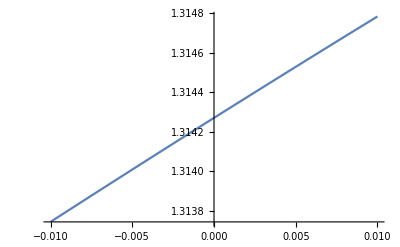

```mathematica
Plot[4*pudfinal[k,4], {k,-0.01,0.01}]
```

### Running the Algorithm for m1Um1Dm2U DIAG

```mathematica
poly1 = int1poly[mode1,mode2,mode1,mode1, mode2, mode1, Stotal]
```

(3 √π (1-(((b^2 x1p)/(a-b)+2 b x2+3+1+1/(a-b))^2)/(-2 a+b+b^2/(2 (a-b)))+(((b^2 x1p)/(a-b)+2 b x2+4+(b^2 x3p)/(a-b))^4)/(12 (-2 a+b+b^2/(2 1))^2)) (-(8 2^(1/4) a^(17/4) (a-3 b)^(3/2) b^2 (x1p-x2p) (-2 a^(5/4) (2/π)^(3/4) x1p+2 a^(5/4) (2/π)^(3/4) x2p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))+(8 2^(1/4) a^(17/4) (a-3 b)^(3/2) b^2 (x1p-x3p) (2 a^(5/4) (2/π)^(3/4) x1p-2 a^(5/4) (2/π)^(3/4) x3p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))-(8 2^(1/4) a^(17/4) (a-3 b)^(3/2) b^2 (x2p-x3p) (-2 a^(5/4) (2/π)^(3/4) x2p+2 a^(5/4) (2/π)^(3/4) x3p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))))/(4 (2 a-b-b^2/(2 (a-b)))^(5/2))-(3 √π ((b^2 x1p)/(a-b)+2 b x2+(b^2 x2)/(a-b)+(b^2 x2p)/(a-b)+2 b x3+(b^2 x3)/(a-b)+(b^2 x3p)/(a-b)) (1-(((b^2 x1p)/(a-b)+5+1/(a-b))^2)/(6 (-2 a+b+b^2/(2 (a-b))))) (1))/(4 (2 a-b-b^2/(2 (a-b)))^(3/2) (-2 a+b+b^2/(2 (a-b))))+(√π (1-1) (-(8 4 (1))/(9 2 π^1)+151))/(2 (2 a-b-b^2/1)^(3/2))-(√π ((b^2 x1p)/(a-b)+2 b x2+(b^2 x2)/(a-b)+(b^2 x2p)/(a-b)+2 b x3+(b^2 x3)/(a-b)+(b^2 x3p)/(a-b)) (174+1/(9 2 π^1)))/(2 √(2 a-b-b^2/(2 (a-b))) (-2 a+b+b^2/(2 (a-b))))+(√π (-(4 2^(1/4) a^(21/4) (a-3 b)^(3/2) x2^2 (x1p-x2p) (-2 a^(5/4) (2/π)^(3/4) x1p+2 a^(5/4) (2/π)^(3/4) x2p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))+247+1/1-(8 2^(1/4) a^(17/4) (a-1)^(3/2) b^2 x1p x2^2 (x2p-x3p) (2 x2+2 x2p+5 x3+2 x3p) (-2 a^(5/4) (2/π)^(3/4) x2p+2 a^(5/4) (2/π)^(3/4) x3p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))))/(√(2 a-b-b^2/(2 (a-b))))
 |  |  |  |

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

-(2 a (4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)-4 a b (2 x1p^2+2 x2^2+2 x2p^2+x2 x3+2 x3^2+x2p x3p+2 x3p^2+x1p (x2p+x3p))+b^2 (3 x1p^2+2 x2^2+3 x2p^2-2 x2p x3+2 x3^2-2 x1p (x2-2 x2p+x3-2 x3p)+4 x2p x3p-2 x3 x3p+3 x3p^2-2 x2 (x2p-x3+x3p))))/(4 a^2-6 a b+b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

-1/(9 (2 a^2-4 a b+b^2)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^2)√2 a^(7/2) √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (128 a^9 √(a-3 b) x3 (4 b x2p^3 x3 x3p-3 x3 x3p^2+4 b x1p^3 x3 (x2p+x3p)+x2p^2 x3 (-5+8 b x3p^2)+2 x2p x3p (x3-x3p+2 b x3 x3p^2)+2 x1p^2 (3 b x2p^2 x3-x2p (1+6 b x3 x3p)+3 x3 (-1+b x3p^2))+2 x1p (b x2p^3 x3+4 x2p x3p-x3p^2-x2p^2 (1+7 b x3 x3p)+x2p x3 (4-7 b x3p^2)+x3 x3p (2+b x3p^2)))+b^7 ((x2p-x3p)^2-b (2 x2p^4+10 x2p^3 x3-2 x2p x3p (27 √(a-3 b)+5 x3 x3p)+x2p^2 (57 √(a-3 b)-10 x3 x3p-4 x3p^2)+4 x1p^2 (15 √(a-3 b)+x2p^2-2 x2p x3p+x3p^2)+x3p^2 (57 √(a-3 b)+10 x3 x3p+2 x3p^2)+x1p (6 x2p^3+x2p^2 (20 x3-6 x3p)-60 √(a-3 b) x3p+20 x3 x3p^2+6 x3p^3-2 x2p (30 √(a-3 b)+20 x3 x3p+3 x3p^2)))+6 √(a-3 b) b^2 (20 x1p^4+19 x2p^4+x3p^3 (31 x3+19 x3p)+x2p^3 (39 x3+22 x3p)+x2p x3p^2 (23 x3+30 x3p)+2 x1p^2 (9 x2p^2+5 x2p x3+4 x3^2-44 x2p x3p+9 x3 x3p+5 x3p^2)+x2p^2 (8 x3^2+23 x3 x3p+14 x3p^2)+x1p^3 (30 x2p+22 (2 x3+x3p))+x1p (27 x2p^3-89 x2p^2 x3p+x3p^2 (8 x3+27 x3p)-x2p (16 x3^2+196 x3 x3p+81 x3p^2))))-32 a^8 (16 √(a-3 b) b^2 x1p^4 x3^2+12 √(a-3 b) b^2 x2p^4 x3^2+4 √(a-3 b) b x2p^3 (-3 x3+3 b x3^3-x3p+50 b x3^2 x3p)+4 √(a-3 b) b x1p^3 (-3 x3+4 b x3^3+x2p (-2+50 b x3^2)-x3p+50 b x3^2 x3p)+x3p^2 (7 √(a-3 b)-8 √(a-3 b) b x3 x3p+12 √(a-3 b) b^2 x3^3 x3p+2 x3^2 (2-73 √(a-3 b) b+6 √(a-3 b) b^2 x3p^2))+2 x2p x3p (-46 √(a-3 b) b x3 x3p-2 √(a-3 b) b^2 x3^3 x3p-√(a-3 b) (3+4 b x3p^2)+2 x3^2 (-2+25 √(a-3 b) b+50 √(a-3 b) b^2 x3p^2))+x2p^2 (-4 √(a-3 b) b x3 x3p-4 √(a-3 b) b^2 x3^3 x3p+√(a-3 b) (7-12 b x3p^2)+x3^2 (4-238 √(a-3 b) b+376 √(a-3 b) b^2 x3p^2))+2 x1p^2 (4 √(a-3 b)-4 √(a-3 b) b^2 x3^2 (-34 x2p^2+(x3-34 x3p) x3p+x2p (x3+74 x3p))-b (x2p^2 (7 √(a-3 b)+4 x3^2)+2 √(a-3 b) x3 x3p+5 √(a-3 b) x3p^2+4 x2p (11 √(a-3 b) x3-3 √(a-3 b) x3p-2 x3^2 x3p)+2 x3^2 (71 √(a-3 b)+2 x3p^2)))+2 x1p (b x2p^3 (-3 √(a-3 b)+(-4+50 √(a-3 b) b) x3^2)+b x2p^2 (-44 √(a-3 b) x3-4 √(a-3 b) b x3^3+13 √(a-3 b) x3p+(4-342 √(a-3 b) b) x3^2 x3p)+x3p (-4 √(a-3 b)+2 √(a-3 b) b^2 x3^2 x3p (-2 x3+25 x3p)+b (-46 √(a-3 b) x3 x3p-3 √(a-3 b) x3p^2+x3^2 (96 √(a-3 b)-4 x3p^2)))+x2p (-4 √(a-3 b)-342 √(a-3 b) b^2 x3^2 x3p^2+b (200 √(a-3 b) x3 x3p+11 √(a-3 b) x3p^2+4 x3^2 (47 √(a-3 b)+x3p^2)))))-32 a^7 ((x2p-x3p)^2-2 b (x2p^2 (35 √(a-3 b)+17 x3^2)-2 x2p (15 √(a-3 b)+17 x3^2) x3p+(35 √(a-3 b)+17 x3^2) x3p^2+x1p (x2p+x3p) (-40 √(a-3 b)+x2p^2-2 x2p x3p+x3p^2)+x1p^2 (40 √(a-3 b)+x2p^2-2 x2p x3p+x3p^2))+2 √(a-3 b) b^3 x3 (4 x1p^4 (x2p-21 x3+x3p)+x2p^4 (-63 x3+4 x3p)+3 x3 x3p^2 (x3^2-18 x3 x3p-21 x3p^2)-2 x2p^3 (27 x3^2+259 x3 x3p-6 x3p^2)+2 x1p^3 (5 x2p^2-259 x2p x3-36 x3^2-2 x2p x3p-259 x3 x3p+5 x3p^2)-2 x2p x3p (x3^3-11 x3^2 x3p+259 x3 x3p^2-2 x3p^3)+x2p^2 (3 x3^3+22 x3^2 x3p-910 x3 x3p^2+12 x3p^3)+2 x1p^2 (4 x2p^3+2 x3^3+20 x3^2 x3p-315 x3 x3p^2+4 x3p^3-5 x2p^2 (63 x3+2 x3p)+2 x2p (10 x3^2+378 x3 x3p-5 x3p^2))+x1p (2 x2p^4-x2p^3 (259 x3+8 x3p)+x2p^2 (38 x3^2+1729 x3 x3p-20 x3p^2)+x3p (-4 x3^3+38 x3^2 x3p-259 x3 x3p^2+2 x3p^3)-x2p (4 x3^3+20 x3^2 x3p-1729 x3 x3p^2+8 x3p^3)))+b^2 (8 √(a-3 b) x1p^4+x2p^4 (7 √(a-3 b)+4 x3^2)+4 √(a-3 b) x1p^3 (22 x2p+29 x3+12 x3p)+x2p^3 (119 √(a-3 b) x3+4 x3^3+48 √(a-3 b) x3p)+x2p x3p (-510 √(a-3 b) x3^2+435 √(a-3 b) x3 x3p-4 x3^3 x3p+88 √(a-3 b) x3p^2)+x2p^2 (39 √(a-3 b) x3 x3p-4 x3^3 x3p+122 √(a-3 b) x3p^2+x3^2 (1163 √(a-3 b)-8 x3p^2))+x3p^2 (79 √(a-3 b) x3 x3p+4 x3^3 x3p+7 √(a-3 b) x3p^2+x3^2 (727 √(a-3 b)+4 x3p^2))+x1p^2 (x2p^2 (139 √(a-3 b)+72 x3^2)+42 √(a-3 b) x3 x3p+99 √(a-3 b) x3p^2+2 x2p (199 √(a-3 b) x3-131 √(a-3 b) x3p-72 x3^2 x3p)+12 x3^2 (115 √(a-3 b)+6 x3p^2))+2 x1p (x2p^3 (33 √(a-3 b)+38 x3^2)+x2p^2 (200 √(a-3 b) x3-141 √(a-3 b) x3p-38 x3^2 x3p)+x3p (220 √(a-3 b) x3 x3p+33 √(a-3 b) x3p^2+x3^2 (-472 √(a-3 b)+38 x3p^2))-x2p (1034 √(a-3 b) x3 x3p+121 √(a-3 b) x3p^2+x3^2 (908 √(a-3 b)+38 x3p^2)))))+4 a^3 b^4 (-154 (x2p-x3p)^2+b (146 x2p^4-280 x2p^3 x3+2 x2p x3p (-1641 √(a-3 b)-754 x3^2+140 x3 x3p)+x2p^2 (3795 √(a-3 b)+754 x3^2+280 x3 x3p-292 x3p^2)+x3p^2 (3795 √(a-3 b)+754 x3^2-280 x3 x3p+146 x3p^2)+x1p^2 (4308 √(a-3 b)+454 x2p^2-908 x2p x3p+454 x3p^2)-12 x1p (-50 x2p^3+x2p^2 (7 x3+50 x3p)+x3p (359 √(a-3 b)+7 x3 x3p-50 x3p^2)+x2p (359 √(a-3 b)-14 x3 x3p+50 x3p^2)))+√(a-3 b) b^3 (44 x1p^6+33 x2p^6-6 x2p^5 (245 x3-37 x3p)+4 x1p^5 (61 x2p-490 x3+61 x3p)+x1p^4 (513 x2p^2-6556 x2p x3+8680 x3^2+266 x2p x3p-6556 x3 x3p+513 x3p^2)+x2p^4 (6510 x3^2-6066 x3 x3p+591 x3p^2)+2 x2p^3 (99 x3^3+9004 x3^2 x3p-5424 x3 x3p^2+402 x3p^3)+3 x3p^2 (-189 x3^4+66 x3^3 x3p+2170 x3^2 x3p^2-490 x3 x3p^3+11 x3p^4)+2 x2p x3p (189 x3^4-1209 x3^3 x3p+9004 x3^2 x3p^2-3033 x3 x3p^3+111 x3p^4)+x2p^2 (-567 x3^4-2418 x3^3 x3p+22996 x3^2 x3p^2-10848 x3 x3p^3+591 x3p^4)+4 x1p^3 (137 x2p^3+66 x3^3+4502 x3^2 x3p-2015 x3 x3p^2+137 x3p^3-x2p^2 (2015 x3+153 x3p)+x2p (4502 x3^2+904 x3 x3p-153 x3p^2))+2 x1p^2 (173 x2p^4-378 x3^4-1242 x3^3 x3p+5911 x3^2 x3p^2-2881 x3 x3p^3+173 x3p^4-x2p^3 (2881 x3+412 x3p)+x2p^2 (5911 x3^2+11735 x3 x3p-1170 x3p^2)-x2p (1242 x3^3+24842 x3^2 x3p-11735 x3 x3p^2+412 x3p^3))+4 x1p (36 x2p^5+x2p^4 (-942 x3+8 x3p)+x2p^3 (2251 x3^2+1808 x3 x3p-156 x3p^2)-x2p^2 (327 x3^3+13587 x3^2 x3p-5500 x3 x3p^2+156 x3p^3)+x2p (189 x3^4+2940 x3^3 x3p-13587 x3^2 x3p^2+1808 x3 x3p^3+8 x3p^4)+x3p (189 x3^4-327 x3^3 x3p+2251 x3^2 x3p^2-942 x3 x3p^3+36 x3p^4)))-2 b^2 (x2p^6+x2p^5 (-67 x3+2 x3p)+x2p^4 (1702 √(a-3 b)+323 x3^2-67 x3 x3p-x3p^2)+4 x1p^4 (491 √(a-3 b)+2 x2p^2-4 x2p x3p+2 x3p^2)+x2p^3 (2742 √(a-3 b) x3+17 x3^3+2990 √(a-3 b) x3p+134 x3 x3p^2-4 x3p^3)+x2p x3p (-3250 √(a-3 b) x3^2+60 x3^4+2902 √(a-3 b) x3 x3p-17 x3^3 x3p+4118 √(a-3 b) x3p^2-67 x3 x3p^3+2 x3p^4)+x1p^3 (25 x2p^3+2280 √(a-3 b) x3+2990 √(a-3 b) x3p-262 x3 x3p^2+25 x3p^3-x2p^2 (262 x3+25 x3p)+x2p (4118 √(a-3 b)+524 x3 x3p-25 x3p^2))+x1p^2 (27 x2p^4-591 x2p^3 x3+8372 √(a-3 b) x3^2+1824 √(a-3 b) x3 x3p+2405 √(a-3 b) x3p^2+1042 x3^2 x3p^2-591 x3 x3p^3+27 x3p^4+x2p^2 (3533 √(a-3 b)+1042 x3^2+591 x3 x3p-54 x3p^2)+x2p (2236 √(a-3 b) x3-11830 √(a-3 b) x3p-2084 x3^2 x3p+591 x3 x3p^2))+x3p^2 (-30 x3^4+17 x3^3 x3p+1702 √(a-3 b) x3p^2+x3p^4+x3^2 (4477 √(a-3 b)+323 x3p^2)+x3 (1614 √(a-3 b) x3p-67 x3p^3))+x2p^2 (-30 x3^4-17 x3^3 x3p+3704 √(a-3 b) x3p^2-x3p^4+x3^2 (7145 √(a-3 b)-646 x3p^2)+2 x3 (681 √(a-3 b) x3p+67 x3p^3))+x1p (11 x2p^5+11 x2p^4 (-36 x3+x3p)+x2p^3 (3081 √(a-3 b)+1365 x3^2-22 x3p^2)+x2p^2 (2350 √(a-3 b) x3-174 x3^3-12343 √(a-3 b) x3p-1365 x3^2 x3p+792 x3 x3p^2-22 x3p^3)-x2p (20788 √(a-3 b) x3 x3p-348 x3^3 x3p+11215 √(a-3 b) x3p^2-11 x3p^4+15 x3^2 (736 √(a-3 b)+91 x3p^2))+x3p (-174 x3^3 x3p+3081 √(a-3 b) x3p^2+11 x3p^4+x3^2 (-5704 √(a-3 b)+1365 x3p^2)+x3 (3478 √(a-3 b) x3p-396 x3p^3)))))-4 a^4 b^3 (-217 (x2p-x3p)^2+b (118 x2p^4-318 x2p^3 x3+2 x2p x3p (-2457 √(a-3 b)-1484 x3^2+159 x3 x3p)+x2p^2 (5719 √(a-3 b)+1484 x3^2+318 x3 x3p-236 x3p^2)+x3p^2 (5719 √(a-3 b)+1484 x3^2-318 x3 x3p+118 x3p^2)+4 x1p^2 (1631 √(a-3 b)+138 x2p^2-276 x2p x3p+138 x3p^2)-2 x1p (-335 x2p^3+x2p^2 (78 x3+335 x3p)+x3p (3262 √(a-3 b)+78 x3 x3p-335 x3p^2)+x2p (3262 √(a-3 b)-156 x3 x3p+335 x3p^2)))+2 √(a-3 b) b^3 (4 x1p^6+3 x2p^6+x2p^5 (-561 x3+36 x3p)+x1p^5 (38 x2p-748 x3+38 x3p)+2 x1p^4 (51 x2p^2-1567 x2p x3+3418 x3^2+20 x2p x3p-1567 x3 x3p+51 x3p^2)+x2p^4 (5127 x3^2-2947 x3 x3p+117 x3p^2)+3 x2p^3 (461 x3^3+5682 x3^2 x3p-2012 x3 x3p^2+56 x3p^3)+3 x3p^2 (-216 x3^4+461 x3^3 x3p+1709 x3^2 x3p^2-187 x3 x3p^3+x3p^4)+x2p x3p (432 x3^4-2009 x3^3 x3p+17046 x3^2 x3p^2-2947 x3 x3p^3+36 x3p^4)+x2p^2 (-648 x3^4-2009 x3^3 x3p+23838 x3^2 x3p^2-6036 x3 x3p^3+117 x3p^4)+x1p^3 (121 x2p^3+1844 x3^3+17046 x3^2 x3p-4656 x3 x3p^2+121 x3p^3-3 x2p^2 (1552 x3+37 x3p)+x2p (17046 x3^2+2012 x3 x3p-111 x3p^2))+x1p^2 (71 x2p^4-864 x3^4-2470 x3^3 x3p+13606 x3^2 x3p^2-3463 x3 x3p^3+71 x3p^4-x2p^3 (3463 x3+154 x3p)+x2p^2 (13606 x3^2+12117 x3 x3p-450 x3p^2)-x2p (2470 x3^3+47720 x3^2 x3p-12117 x3 x3p^2+154 x3p^3))+x1p (21 x2p^5-x2p^4 (1754 x3+5 x3p)+x2p^3 (8523 x3^2+4024 x3 x3p-120 x3p^2)-x2p^2 (1696 x3^3+52825 x3^2 x3p-11556 x3 x3p^2+120 x3p^3)+x2p (864 x3^4+7740 x3^3 x3p-52825 x3^2 x3p^2+4024 x3 x3p^3-5 x3p^4)+x3p (864 x3^4-1696 x3^3 x3p+8523 x3^2 x3p^2-1754 x3 x3p^3+21 x3p^4)))-2 b^2 (-40 x2p^5 x3+2 x2p^4 (839 √(a-3 b)+231 x3^2-20 x3 x3p)+2 x1p^4 (964 √(a-3 b)+x2p^2-2 x2p x3p+x3p^2)+x2p^3 (4193 √(a-3 b) x3+148 x3^3+3538 √(a-3 b) x3p+80 x3 x3p^2)+x2p x3p (-7038 √(a-3 b) x3^2+124 x3^4+5533 √(a-3 b) x3 x3p-148 x3^3 x3p+5190 √(a-3 b) x3p^2-40 x3 x3p^3)+x1p^3 (6 x2p^3+3538 √(a-3 b) x3p+6 x3p^3-2 x2p^2 (124 x3+3 x3p)+8 x3 (447 √(a-3 b)-31 x3p^2)+x2p (5190 √(a-3 b)+496 x3 x3p-6 x3p^2))+x1p^2 (6 x2p^4-536 x2p^3 x3+3817 √(a-3 b) x3p^2+6 x3p^4+x2p^2 (5469 √(a-3 b)+1924 x3^2+536 x3 x3p-12 x3p^2)+4 x3^2 (4428 √(a-3 b)+481 x3p^2)+2 x2p (2249 √(a-3 b) x3-7535 √(a-3 b) x3p-1924 x3^2 x3p+268 x3 x3p^2)+x3 (2334 √(a-3 b) x3p-536 x3p^3))+x3p^2 (-62 x3^4+148 x3^3 x3p+1678 √(a-3 b) x3p^2+x3^2 (9641 √(a-3 b)+462 x3p^2)+x3 (2541 √(a-3 b) x3p-40 x3p^3))+x2p^2 (-62 x3^4-148 x3^3 x3p+5372 √(a-3 b) x3p^2+x3^2 (15109 √(a-3 b)-924 x3p^2)+x3 (1717 √(a-3 b) x3p+80 x3p^3))+x1p (2 x2p^5+x2p^4 (-328 x3+2 x3p)+x2p^3 (3885 √(a-3 b)+2386 x3^2-4 x3p^2)+x2p^2 (4774 √(a-3 b) x3-200 x3^3-15875 √(a-3 b) x3p-2386 x3^2 x3p+656 x3 x3p^2-4 x3p^3)-x2p (35592 √(a-3 b) x3 x3p-400 x3^3 x3p+14223 √(a-3 b) x3p^2-2 x3p^4+x3^2 (23180 √(a-3 b)+2386 x3p^2))+x3p (-200 x3^3 x3p+3885 √(a-3 b) x3p^2+2 x3p^4+x3^2 (-12244 √(a-3 b)+2386 x3p^2)+x3 (6426 √(a-3 b) x3p-328 x3p^3)))))-4 a^2 b^5 (-51 (x2p-x3p)^2+2 b (43 x2p^4-42 x2p^3 x3+6 x2p x3p (-97 √(a-3 b)-32 x3^2+7 x3 x3p)+x2p^2 (662 √(a-3 b)+96 x3^2+42 x3 x3p-86 x3p^2)+x3p^2 (662 √(a-3 b)+96 x3^2-42 x3 x3p+43 x3p^2)+2 x1p^2 (371 √(a-3 b)+47 x2p^2-94 x2p x3p+47 x3p^2)+x1p (137 x2p^3+x2p^2 (12 x3-137 x3p)+x3p (-742 √(a-3 b)+12 x3 x3p+137 x3p^2)-x2p (742 √(a-3 b)+24 x3 x3p+137 x3p^2)))+√(a-3 b) b^3 (72 x1p^6+2 x1p^5 (153 x2p-566 x3+153 x3p)+x1p^4 (513 x2p^2-3190 x2p x3+2916 x3^2+342 x2p x3p-3190 x3 x3p+513 x3p^2)+x1p^3 (477 x2p^3-468 x3^3+5082 x3^2 x3p-3164 x3 x3p^2+477 x3p^3-x2p^2 (3164 x3+675 x3p)+x2p (5082 x3^2+1492 x3 x3p-675 x3p^2))+x1p^2 (333 x2p^4-108 x3^4-594 x3^3 x3p+2520 x3^2 x3p^2-2135 x3 x3p^3+333 x3p^4-7 x2p^3 (305 x3+126 x3p)+x2p^2 (2520 x3^2+10573 x3 x3p-2430 x3p^2)-x2p (594 x3^3+13788 x3^2 x3p-10573 x3 x3p^2+882 x3p^3))+x1p (189 x2p^5+x2p^4 (-1878 x3+99 x3p)+x2p^3 (2541 x3^2+2984 x3 x3p-648 x3p^2)-x2p^2 (180 x3^3+14871 x3^2 x3p-9724 x3 x3p^2+648 x3p^3)+3 x3p (36 x3^4-60 x3^3 x3p+847 x3^2 x3p^2-626 x3 x3p^3+63 x3p^4)+x2p (108 x3^4+4140 x3^3 x3p-14871 x3^2 x3p^2+2984 x3 x3p^3+99 x3p^4))+3 (18 x2p^6+x2p^5 (-283 x3+90 x3p)+3 x2p^4 (243 x3^2-323 x3 x3p+66 x3p^2)+x2p^3 (-117 x3^3+1694 x3^2 x3p-1492 x3 x3p^2+252 x3p^3)+x3p^2 (-27 x3^4-117 x3^3 x3p+729 x3^2 x3p^2-283 x3 x3p^3+18 x3p^4)+x2p x3p (18 x3^4-237 x3^3 x3p+1694 x3^2 x3p^2-969 x3 x3p^3+90 x3p^4)+x2p^2 (-27 x3^4-237 x3^3 x3p+1930 x3^2 x3p^2-1492 x3 x3p^3+198 x3p^4)))-b^2 (5 x2p^6+x2p^5 (-88 x3+10 x3p)+x2p^4 (1793 √(a-3 b)+232 x3^2-88 x3 x3p-5 x3p^2)+x1p^4 (2068 √(a-3 b)+19 x2p^2-38 x2p x3p+19 x3p^2)+x2p^3 (2227 √(a-3 b) x3-36 x3^3+2708 √(a-3 b) x3p+176 x3 x3p^2-20 x3p^3)+x2p^2 (3565 √(a-3 b) x3^2-9 x3^4+1295 √(a-3 b) x3 x3p+36 x3^3 x3p+2674 √(a-3 b) x3p^2-464 x3^2 x3p^2+176 x3 x3p^3-5 x3p^4)+x3p^2 (2105 √(a-3 b) x3^2-9 x3^4+1383 √(a-3 b) x3 x3p-36 x3^3 x3p+1793 √(a-3 b) x3p^2+232 x3^2 x3p^2-88 x3 x3p^3+5 x3p^4)+x2p x3p (-1510 √(a-3 b) x3^2+18 x3^4+1911 √(a-3 b) x3 x3p+36 x3^3 x3p+3552 √(a-3 b) x3p^2-88 x3 x3p^3+10 x3p^4)+2 x1p^3 (31 x2p^3+988 √(a-3 b) x3+1354 √(a-3 b) x3p-118 x3 x3p^2+31 x3p^3-x2p^2 (118 x3+31 x3p)+x2p (1776 √(a-3 b)+236 x3 x3p-31 x3p^2))+x1p^2 (72 x2p^4-560 x2p^3 x3+4160 √(a-3 b) x3^2+1546 √(a-3 b) x3 x3p+1529 √(a-3 b) x3p^2+582 x3^2 x3p^2-560 x3 x3p^3+72 x3p^4+x2p^2 (2373 √(a-3 b)+582 x3^2+560 x3 x3p-144 x3p^2)+2 x2p (659 √(a-3 b) x3-5053 √(a-3 b) x3p-582 x3^2 x3p+280 x3 x3p^2))+2 x1p (17 x2p^5+x2p^4 (-206 x3+17 x3p)+x2p^3 (1341 √(a-3 b)+407 x3^2-34 x3p^2)+x2p^2 (609 √(a-3 b) x3-66 x3^3-5213 √(a-3 b) x3p-407 x3^2 x3p+412 x3 x3p^2-34 x3p^3)-x2p (7468 √(a-3 b) x3 x3p-132 x3^3 x3p+4791 √(a-3 b) x3p^2-17 x3p^4+x3^2 (2810 √(a-3 b)+407 x3p^2))+x3p (-66 x3^3 x3p+1341 √(a-3 b) x3p^2+17 x3p^4+x3^2 (-1350 √(a-3 b)+407 x3p^2)+x3 (1031 √(a-3 b) x3p-206 x3p^3)))))+a b^6 (-28 (x2p-x3p)^2+12 √(a-3 b) b^3 (x1p+x2p-3 x3+x3p)^2 (3 x1p+3 x2p-x3+3 x3p) (4 x1p^3-20 x1p x2p x3p+2 x1p^2 (x2p+x3p)+3 (x2p^3+x2p^2 x3p+x2p x3p^2+x3p^3))+b (68 x2p^4+4 x2p^3 x3-2 x2p x3p (405 √(a-3 b)+76 x3^2+2 x3 x3p)+x2p^2 (895 √(a-3 b)+76 x3^2-4 x3 x3p-136 x3p^2)+4 x1p^2 (245 √(a-3 b)+31 x2p^2-62 x2p x3p+31 x3p^2)+x3p^2 (895 √(a-3 b)+76 x3^2+4 x3 x3p+68 x3p^2)-4 x1p (-48 x2p^3+x2p^2 (-28 x3+48 x3p)+x3p (245 √(a-3 b)-28 x3 x3p-48 x3p^2)+x2p (245 √(a-3 b)+56 x3 x3p+48 x3p^2)))-2 b^2 (6 x2p^6+x2p^5 (-38 x3+12 x3p)+x2p^4 (805 √(a-3 b)+66 x3^2-38 x3 x3p-6 x3p^2)+4 x1p^4 (227 √(a-3 b)+3 x2p^2-6 x2p x3p+3 x3p^2)+x2p^3 (1089 √(a-3 b) x3-18 x3^3+1078 √(a-3 b) x3p+76 x3 x3p^2-24 x3p^3)+x2p^2 (806 √(a-3 b) x3^2+665 √(a-3 b) x3 x3p+18 x3^3 x3p+866 √(a-3 b) x3p^2-132 x3^2 x3p^2+76 x3 x3p^3-6 x3p^4)+x3p^2 (390 √(a-3 b) x3^2+769 √(a-3 b) x3 x3p-18 x3^3 x3p+805 √(a-3 b) x3p^2+66 x3^2 x3p^2-38 x3 x3p^3+6 x3p^4)+x2p x3p (-276 √(a-3 b) x3^2+761 √(a-3 b) x3 x3p+18 x3^3 x3p+1398 √(a-3 b) x3p^2-38 x3 x3p^3+12 x3p^4)+2 x1p^3 (21 x2p^3+550 √(a-3 b) x3+539 √(a-3 b) x3p-38 x3 x3p^2+21 x3p^3-x2p^2 (38 x3+21 x3p)+x2p (699 √(a-3 b)+76 x3 x3p-21 x3p^2))+2 x1p^2 (27 x2p^4-95 x2p^3 x3+460 √(a-3 b) x3^2+327 √(a-3 b) x3 x3p+236 √(a-3 b) x3p^2+66 x3^2 x3p^2-95 x3 x3p^3+27 x3p^4+x2p^2 (396 √(a-3 b)+66 x3^2+95 x3 x3p-54 x3p^2)+x2p (215 √(a-3 b) x3-1994 √(a-3 b) x3p-132 x3^2 x3p+95 x3 x3p^2))+x1p (30 x2p^5+x2p^4 (-152 x3+30 x3p)+3 x2p^3 (369 √(a-3 b)+66 x3^2-20 x3p^2)-x2p^2 (36 x3^3+4073 √(a-3 b) x3p+198 x3^2 x3p+60 x3p^3-4 x3 (63 √(a-3 b)+76 x3p^2))-x2p (6292 √(a-3 b) x3 x3p-72 x3^3 x3p+3753 √(a-3 b) x3p^2-30 x3p^4+2 x3^2 (668 √(a-3 b)+99 x3p^2))+x3p (-36 x3^3 x3p+1107 √(a-3 b) x3p^2+30 x3p^4+x3^2 (-504 √(a-3 b)+198 x3p^2)+4 x3 (143 √(a-3 b) x3p-38 x3p^3)))))+4 a^5 b^2 (-156 (x2p-x3p)^2+b (48 x2p^4-148 x2p^3 x3+2 x2p x3p (-2061 √(a-3 b)-1584 x3^2+74 x3 x3p)+x2p^2 (4807 √(a-3 b)+1584 x3^2+148 x3 x3p-96 x3p^2)+x3p^2 (4807 √(a-3 b)+1584 x3^2-148 x3 x3p+48 x3p^2)+4 x1p^2 (1373 √(a-3 b)+90 x2p^2-180 x2p x3p+90 x3p^2)-4 x1p (-102 x2p^3+2 x2p^2 (11 x3+51 x3p)+x3p (1373 √(a-3 b)+22 x3 x3p-102 x3p^2)+x2p (1373 √(a-3 b)-44 x3 x3p+102 x3p^2)))+4 √(a-3 b) b^3 (2 x1p^5 (x2p-64 x3+x3p)+x2p^5 (-96 x3+2 x3p)+x1p^4 (7 x2p^2-752 x2p x3+2964 x3^2+2 x2p x3p-752 x3 x3p+7 x3p^2)+x2p^4 (2223 x3^2-720 x3 x3p+8 x3p^2)+3 x3 x3p^2 (-91 x3^3+368 x3^2 x3p+741 x3 x3p^2-32 x3p^3)+2 x2p^3 (552 x3^3+4583 x3^2 x3p-840 x3 x3p^2+6 x3p^3)+2 x2p x3p (91 x3^4-428 x3^3 x3p+4583 x3^2 x3p^2-360 x3 x3p^3+x3p^4)+x2p^2 (-273 x3^4-856 x3^3 x3p+13886 x3^2 x3p^2-1680 x3 x3p^3+8 x3p^4)+x1p^3 (9 x2p^3+1472 x3^3+9166 x3^2 x3p-1336 x3 x3p^2+9 x3p^3-x2p^2 (1336 x3+7 x3p)+x2p (9166 x3^2+560 x3 x3p-7 x3p^2))+x1p^2 (5 x2p^4-364 x3^4-1224 x3^3 x3p+8562 x3^2 x3p^2-1024 x3 x3p^3+5 x3p^4-2 x2p^3 (512 x3+5 x3p)+x2p^2 (8562 x3^2+3152 x3 x3p-30 x3p^2)-2 x2p (612 x3^3+13008 x3^2 x3p-1576 x3 x3p^2+5 x3p^3))+x1p (x2p^5-x2p^4 (408 x3+x3p)+x2p^3 (4583 x3^2+1120 x3 x3p-8 x3p^2)-x2p^2 (980 x3^3+29117 x3^2 x3p-3056 x3 x3p^2+8 x3p^3)+x2p (364 x3^4+2440 x3^3 x3p-29117 x3^2 x3p^2+1120 x3 x3p^3-x3p^4)+x3p (364 x3^4-980 x3^3 x3p+4583 x3^2 x3p^2-408 x3 x3p^3+x3p^4)))-2 b^2 (1036 √(a-3 b) x1p^4-8 x2p^5 x3+x2p^4 (905 √(a-3 b)+340 x3^2-8 x3 x3p)+2 x1p^3 (1891 √(a-3 b) x2p+1686 √(a-3 b) x3-52 x2p^2 x3+1203 √(a-3 b) x3p+104 x2p x3 x3p-52 x3 x3p^2)+x2p^3 (3753 √(a-3 b) x3+196 x3^3+2406 √(a-3 b) x3p+16 x3 x3p^2)+x2p x3p (-8252 √(a-3 b) x3^2+80 x3^4+6385 √(a-3 b) x3 x3p-196 x3^3 x3p+3782 √(a-3 b) x3p^2-8 x3 x3p^3)+x3p^2 (11370 √(a-3 b) x3^2-40 x3^4+2377 √(a-3 b) x3 x3p+196 x3^3 x3p+905 √(a-3 b) x3p^2+340 x3^2 x3p^2-8 x3 x3p^3)+x2p^2 (17794 √(a-3 b) x3^2-40 x3^4+1337 √(a-3 b) x3 x3p-196 x3^3 x3p+4378 √(a-3 b) x3p^2-680 x3^2 x3p^2+16 x3 x3p^3)+2 x1p^2 (-108 x2p^3 x3+10456 √(a-3 b) x3^2+859 √(a-3 b) x3 x3p+1650 √(a-3 b) x3p^2+960 x3^2 x3p^2-108 x3 x3p^3+2 x2p^2 (1169 √(a-3 b)+480 x3^2+54 x3 x3p)+x2p (2695 √(a-3 b) x3-5542 √(a-3 b) x3p-1920 x3^2 x3p+108 x3 x3p^2))+x1p (-120 x2p^4 x3+5 x2p^3 (567 √(a-3 b)+452 x3^2)+x2p^2 (-96 x3^3-11769 √(a-3 b) x3p-2260 x3^2 x3p+80 x3 (70 √(a-3 b)+3 x3p^2))-x2p (36908 √(a-3 b) x3 x3p-192 x3^3 x3p+10393 √(a-3 b) x3p^2+4 x3^2 (6834 √(a-3 b)+565 x3p^2))+x3p (-96 x3^3 x3p+2835 √(a-3 b) x3p^2-4 x3^2 (3622 √(a-3 b)-565 x3p^2)+8 x3 (872 √(a-3 b) x3p-15 x3p^3)))))+16 a^6 b (14 (x2p-x3p)^2-b (2 x2p^4-6 x2p^3 x3+2 x2p x3p (-243 √(a-3 b)-230 x3^2+3 x3 x3p)+x2p^2 (567 √(a-3 b)+230 x3^2+6 x3 x3p-4 x3p^2)+x3p^2 (567 √(a-3 b)+230 x3^2-6 x3 x3p+2 x3p^2)+6 x1p^2 (108 √(a-3 b)+5 x2p^2-10 x2p x3p+5 x3p^2)-4 x1p (-8 x2p^3+x2p^2 (x3+8 x3p)+x3p (162 √(a-3 b)+x3 x3p-8 x3p^2)+2 x2p (81 √(a-3 b)-x3 x3p+4 x3p^2)))+2 √(a-3 b) b^3 x3 (8 x1p^5+6 x2p^5+x2p^4 (-525 x3+86 x3p)+x1p^4 (88 x2p-700 x3+88 x3p)+2 x1p^3 (93 x2p^2-1435 x2p x3-242 x3^2-38 x2p x3p-1435 x3 x3p+93 x3p^2)+x2p^3 (-363 x3^2-2870 x3 x3p+228 x3p^2)+3 x3p^2 (16 x3^3-121 x3^2 x3p-175 x3 x3p^2+2 x3p^3)+x2p x3p (-32 x3^3+193 x3^2 x3p-2870 x3 x3p^2+86 x3p^3)+x2p^2 (48 x3^3+193 x3^2 x3p-4690 x3 x3p^2+228 x3p^3)+2 x1p^2 (73 x2p^3+32 x3^3+157 x3^2 x3p-1540 x3 x3p^2+73 x3p^3-x2p^2 (1540 x3+201 x3p)+x2p (157 x3^2+4130 x3 x3p-201 x3p^2))+x1p (46 x2p^4-x2p^3 (1435 x3+152 x3p)+x2p^2 (278 x3^2+9345 x3 x3p-396 x3p^2)+x3p (-64 x3^3+278 x3^2 x3p-1435 x3 x3p^2+46 x3p^3)-x2p (64 x3^3+360 x3^2 x3p-9345 x3 x3p^2+152 x3p^3)))+b^2 (144 √(a-3 b) x1p^4+6 x2p^4 (21 √(a-3 b)+10 x3^2)+x2p^3 (935 √(a-3 b) x3+48 x3^3+468 √(a-3 b) x3p)+x2p x3p (-2732 √(a-3 b) x3^2+8 x3^4+2191 √(a-3 b) x3 x3p-48 x3^3 x3p+792 √(a-3 b) x3p^2)+4 x1p^3 (198 √(a-3 b) x2p+220 √(a-3 b) x3-2 x2p^2 x3+117 √(a-3 b) x3p+4 x2p x3 x3p-2 x3 x3p^2)+x2p^2 (-4 x3^4+311 √(a-3 b) x3 x3p-48 x3^3 x3p+1008 √(a-3 b) x3p^2+2 x3^2 (3011 √(a-3 b)-60 x3p^2))+x3p^2 (-4 x3^4+611 √(a-3 b) x3 x3p+48 x3^3 x3p+126 √(a-3 b) x3p^2+x3^2 (3818 √(a-3 b)+60 x3p^2))+2 x1p^2 (-8 x2p^3 x3+3554 √(a-3 b) x3^2+183 √(a-3 b) x3 x3p+396 √(a-3 b) x3p^2+260 x3^2 x3p^2-8 x3 x3p^3+x2p^2 (558 √(a-3 b)+260 x3^2+8 x3 x3p)+x2p (961 √(a-3 b) x3-1170 √(a-3 b) x3p-520 x3^2 x3p+8 x3 x3p^2))+2 x1p (-4 x2p^4 x3+x2p^3 (297 √(a-3 b)+290 x3^2)+x2p^2 (978 √(a-3 b) x3-4 x3^3-1251 √(a-3 b) x3p-290 x3^2 x3p+8 x3 x3p^2)-x2p (5726 √(a-3 b) x3 x3p-8 x3^3 x3p+1089 √(a-3 b) x3p^2+x3^2 (4656 √(a-3 b)+290 x3p^2))+x3p (-4 x3^3 x3p+297 √(a-3 b) x3p^2+x3^2 (-2452 √(a-3 b)+290 x3p^2)+4 x3 (285 √(a-3 b) x3p-x3p^3))))))

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

(a (-4 a^2 (x1p^2+x2p^2+x3^2+x3p^2)-b^2 (5 x1p^2+5 x2p^2-2 x2p x3+3 x3^2+6 x2p x3p-2 x3 x3p+5 x3p^2+x1p (6 x2p-2 x3+6 x3p))+2 a b (5 x1p^2+5 x2p^2+2 x2p x3p+2 x1p (x2p+x3p)+5 (x3^2+x3p^2))))/(2 a^2-4 a b+b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

-1/(9 (4 a^2-10 a b+5 b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))4 √2 √a √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (22500 √(a-3 b) b^13+125 a b^12 ((-35+54 √(a-3 b) b) x2p^2+70 x2p x3p-6 √(a-3 b) b x2p (181 x3+437 x3p)-5 (432 √(a-3 b)+7 x3p^2)+6 √(a-3 b) b (241 x3^2-171 x3 x3p+29 x3p^2))+8192 a^15 √(a-3 b) x3 (4 b x2p^3 x3 x3p-3 x3 x3p^2+x2p^2 x3 (-5+8 b x3p^2)+2 x2p x3p (x3-x3p+2 b x3 x3p^2))-2048 a^14 (8 √(a-3 b) b^2 x2p^4 x3^2+7 √(a-3 b) x3p^2-4 √(a-3 b) b x3 x3p^3+12 √(a-3 b) b^2 x3^3 x3p^3+4 √(a-3 b) b x2p^3 (-2 x3+3 b x3^3-x3p+84 b x3^2 x3p)+x3^2 (6 √(a-3 b)+(4-244 √(a-3 b) b) x3p^2+8 √(a-3 b) b^2 x3p^4)-2 x2p (2 √(a-3 b) b^2 x3^3 x3p^2+√(a-3 b) x3p (3+4 b x3p^2)+√(a-3 b) x3 (-1+80 b x3p^2)-4 x3^2 x3p (-1+18 √(a-3 b) b+42 √(a-3 b) b^2 x3p^2))+x2p^2 (-16 √(a-3 b) b x3 x3p-4 √(a-3 b) b^2 x3^3 x3p+√(a-3 b) (7-12 b x3p^2)+x3^2 (4-400 √(a-3 b) b+656 √(a-3 b) b^2 x3p^2)))+25 a^2 b^11 (59510 √(a-3 b)+2 b (-55+3657 √(a-3 b) b) x2p^4+2325 x3p^2+2 b x2p^3 ((845+11589 √(a-3 b) b) x3+16338 √(a-3 b) b x3p)-5 b (16730 √(a-3 b) x3^2-8874 √(a-3 b) x3 x3p+4867 √(a-3 b) x3p^2+688 x3^2 x3p^2-338 x3 x3p^3+22 x3p^4)+6 √(a-3 b) b^2 (244 x3^4-1198 x3^3 x3p+1946 x3^2 x3p^2+2343 x3 x3p^3+1039 x3p^4)+x2p^2 (2325-5 b (3867 √(a-3 b)+688 x3^2+338 x3 x3p-44 x3p^2)+6 √(a-3 b) b^2 (4706 x3^2+19719 x3 x3p+8774 x3p^2))-2 x2p (2325 x3p-5 b (4567 √(a-3 b) x3+13778 √(a-3 b) x3p+688 x3^2 x3p-169 x3 x3p^2)+3 √(a-3 b) b^2 (1738 x3^3+15648 x3^2 x3p-19699 x3 x3p^2-5586 x3p^3)))-128 a^10 b^3 (8 √(a-3 b) b^3 x2p^6-4 b^2 x2p^5 ((4+1515 √(a-3 b) b) x3-64 √(a-3 b) b x3p)-2 (8677 √(a-3 b)+2947 x3p^2)+4 √(a-3 b) b^3 x3p (106 x3^5-10728 x3^4 x3p+65057 x3^3 x3p^2+63017 x3^2 x3p^3-1515 x3 x3p^4+2 x3p^5)+4 b x2p^4 (-19+b (-7987 √(a-3 b)+626 x3^2-4 x3 x3p)+√(a-3 b) b^2 (63017 x3^2-22621 x3 x3p+238 x3p^2))+4 b x2p^3 (b (-4470+65057 √(a-3 b) b) x3^3+696926 √(a-3 b) b^2 x3^2 x3p+2 √(a-3 b) b x3p (-32937+176 b x3p^2)-x3 (939+54804 √(a-3 b) b-8 b x3p^2+60288 √(a-3 b) b^2 x3p^2))+b (248839 √(a-3 b) x3p^2-76 x3p^4+x3^2 (232514 √(a-3 b)+89980 x3p^2)-2 x3 (671 √(a-3 b) x3p+1878 x3p^3))+x2p^2 (-5894+b (254783 √(a-3 b)+89980 x3^2+3756 x3 x3p+152 x3p^2)-8 b^2 (345381 √(a-3 b) x3^2-249 x3^4+82154 √(a-3 b) x3 x3p-2235 x3^3 x3p+69915 √(a-3 b) x3p^2+626 x3^2 x3p^2-4 x3 x3p^3)-4 √(a-3 b) b^3 (10728 x3^4+63903 x3^3 x3p-1267818 x3^2 x3p^2+60288 x3 x3p^3-238 x3p^4))+4 b^2 (-7618 √(a-3 b) x3p^4+x3^4 (489 √(a-3 b)+498 x3p^2)+3 x3^3 (5129 √(a-3 b) x3p-1490 x3p^3)+x3^2 (-442190 √(a-3 b) x3p^2+626 x3p^4)-x3 (19443 √(a-3 b) x3p^3+4 x3p^5))+2 x2p (5894 x3p+b (26388 √(a-3 b) x3-85597 √(a-3 b) x3p-89980 x3^2 x3p+1878 x3 x3p^2)+2 b^2 (22792 √(a-3 b) x3^3+186307 √(a-3 b) x3^2 x3p-996 x3^4 x3p-317222 √(a-3 b) x3 x3p^2+4470 x3^3 x3p^2-89561 √(a-3 b) x3p^3-4 x3 x3p^4)+2 √(a-3 b) b^3 (106 x3^5+3556 x3^4 x3p-63903 x3^3 x3p^2+696926 x3^2 x3p^3-22621 x3 x3p^4+64 x3p^5)))-32 a^8 b^5 (4 b^2 (2+463 √(a-3 b) b) x2p^6-10 (42505 √(a-3 b)+10849 x3p^2)-4 √(a-3 b) b^3 (76 x3^6-7054 x3^5 x3p+179624 x3^4 x3p^2-563497 x3^3 x3p^3-770138 x3^2 x3p^4+51496 x3 x3p^5-463 x3p^6)-8 b^2 x2p^5 ((315+25748 √(a-3 b) b) x3-2 (x3p+1610 √(a-3 b) b x3p))+2 b x2p^4 (-1248-b (350531 √(a-3 b)-33324 x3^2+1260 x3 x3p+4 x3p^2)+2 √(a-3 b) b^2 (770138 x3^2-548416 x3 x3p+21593 x3p^2))+4 b x2p^3 (b (-60392+563497 √(a-3 b) b) x3^3-1168729 √(a-3 b) b x3p+6984120 √(a-3 b) b^2 x3^2 x3p+8 b (-1+3904 √(a-3 b) b) x3p^3-x3 (27959+651029 √(a-3 b) b-1260 b x3p^2+1387768 √(a-3 b) b^2 x3p^2))+b (3523101 √(a-3 b) x3p^2-2496 x3p^4+4 x3^2 (882391 √(a-3 b)+255279 x3p^2)-4 x3 (49406 √(a-3 b) x3p+27959 x3p^3))+x2p^2 (-108490+b (3610361 √(a-3 b)+1021116 x3^2+111836 x3 x3p+4992 x3p^2)-4 √(a-3 b) b^3 (179624 x3^4+1138083 x3^3 x3p-12427964 x3^2 x3p^2+1387768 x3 x3p^3-21593 x3p^4)-4 b^2 (6445173 √(a-3 b) x3^2-10744 x3^4+2519945 √(a-3 b) x3 x3p-60392 x3^3 x3p+2250274 √(a-3 b) x3p^2+33324 x3^2 x3p^2-1260 x3 x3p^3+2 x3p^4))+2 b^2 (-324975 √(a-3 b) x3p^4+4 x3p^6+2 x3^4 (6155 √(a-3 b)+10744 x3p^2)+16 x3^3 (42999 √(a-3 b) x3p-7549 x3p^3)+x3^2 (-8347654 √(a-3 b) x3p^2+33324 x3p^4)-4 x3 (81761 √(a-3 b) x3p^3+315 x3p^5))+2 x2p (108490 x3p+b (211388 √(a-3 b) x3-1306229 √(a-3 b) x3p-1021116 x3^2 x3p+55918 x3 x3p^2)+2 b^2 (484011 √(a-3 b) x3^3+2035210 √(a-3 b) x3^2 x3p-21488 x3^4 x3p-3573938 √(a-3 b) x3 x3p^2+60392 x3^3 x3p^2-1419298 √(a-3 b) x3p^3-630 x3 x3p^4+4 x3p^5)+2 √(a-3 b) b^3 (7054 x3^5+39024 x3^4 x3p-1138083 x3^3 x3p^2+6984120 x3^2 x3p^3-548416 x3 x3p^4+6440 x3p^5)))+4 a^5 b^8 (20 b^2 (62+2937 √(a-3 b) b) x2p^6-4 b^2 x2p^5 ((9880+392511 √(a-3 b) b) x3-10 (62+13791 √(a-3 b) b) x3p)-50 (94341 √(a-3 b)+13049 x3p^2)-4 √(a-3 b) b^3 (3748 x3^6-65950 x3^5 x3p+482195 x3^4 x3p^2-429335 x3^3 x3p^3-2200560 x3^2 x3p^4+392511 x3 x3p^5-14685 x3p^6)+20 b x2p^4 (280-2 b (118419 √(a-3 b)-7899 x3^2+988 x3 x3p+31 x3p^2)+√(a-3 b) b^2 (440112 x3^2-642221 x3 x3p+83895 x3p^2))+10 b x2p^3 (2 b (-30964+85867 √(a-3 b) b) x3^3+6553736 √(a-3 b) b^2 x3^2 x3p-x3 (88200+1029101 √(a-3 b) b-7904 b x3p^2+3068304 √(a-3 b) b^2 x3p^2)+8 b x3p (-316943 √(a-3 b)+(-62+29625 √(a-3 b) b) x3p^2))+5 b (2995911 √(a-3 b) x3p^2+1120 x3p^4+8 x3^2 (493898 √(a-3 b)+81015 x3p^2)-16 x3 (51244 √(a-3 b) x3p+11025 x3p^3))-5 x2p^2 (130490-b (2990481 √(a-3 b)+648120 x3^2+176400 x3 x3p-2240 x3p^2)+4 √(a-3 b) b^3 (96439 x3^4+985229 x3^3 x3p-5673512 x3^2 x3p^2+1534152 x3 x3p^3-83895 x3p^4)+2 b^2 (5936545 √(a-3 b) x3^2-15104 x3^4+5464263 √(a-3 b) x3 x3p-61928 x3^3 x3p+4401136 √(a-3 b) x3p^2+63192 x3^2 x3p^2-7904 x3 x3p^3+124 x3p^4))-10 b^2 (424826 √(a-3 b) x3p^4-124 x3p^6+2 x3^4 (18067 √(a-3 b)-7552 x3p^2)-8 x3^3 (95508 √(a-3 b) x3p-7741 x3p^3)+x3^2 (3764565 √(a-3 b) x3p^2-31596 x3p^4)+13 x3 (19917 √(a-3 b) x3p^3+304 x3p^5))+10 x2p (130490 x3p-2 b (126161 √(a-3 b) x3+1018302 √(a-3 b) x3p+324060 x3^2 x3p-44100 x3 x3p^2)+b^2 (1033194 √(a-3 b) x3^3+4167880 √(a-3 b) x3^2 x3p-30208 x3^4 x3p-5977833 √(a-3 b) x3 x3p^2+61928 x3^3 x3p^2-2764094 √(a-3 b) x3p^3-3952 x3 x3p^4+248 x3p^5)+2 √(a-3 b) b^3 (13190 x3^5+42922 x3^4 x3p-985229 x3^3 x3p^2+3276868 x3^2 x3p^3-642221 x3 x3p^4+27582 x3p^5)))+a^3 b^10 (24 b^2 (25+1071 √(a-3 b) b) x2p^6-8 b^2 x2p^5 ((1225+45621 √(a-3 b) b) x3-6 (25+4338 √(a-3 b) b) x3p)-250 (20011 √(a-3 b)+1361 x3p^2)-24 √(a-3 b) b^3 (-7 x3+x3p)^2 (4 x3^4-38 x3^3 x3p+126 x3^2 x3p^2+213 x3 x3p^3-1071 x3p^4)+10 b x2p^4 (1650-5 b (36973 √(a-3 b)-988 x3^2+196 x3 x3p+12 x3p^2)+36 √(a-3 b) b^2 (3689 x3^2-7319 x3 x3p+1671 x3p^2))+25 b (208157 √(a-3 b) x3p^2+660 x3p^4+8 x3^2 (55846 √(a-3 b)+4615 x3p^2)-16 x3 (10968 √(a-3 b) x3p+955 x3p^3))-5 x2p^2 (68050-5 b (191437 √(a-3 b)+36920 x3^2+15280 x3 x3p-1320 x3p^2)+24 √(a-3 b) b^3 (1342 x3^4+28631 x3^3 x3p-123302 x3^2 x3p^2+50664 x3 x3p^3-5013 x3p^4)+10 b^2 (225578 √(a-3 b) x3^2-392 x3^4+490755 √(a-3 b) x3 x3p-1484 x3^3 x3p+289058 √(a-3 b) x3p^2+1976 x3^2 x3p^2-392 x3 x3p^3+12 x3p^4))-50 b^2 (32293 √(a-3 b) x3p^4-12 x3p^6+4 x3^4 (1459 √(a-3 b)-98 x3p^2)+x3^3 (-45298 √(a-3 b) x3p+1484 x3p^3)+2 x3^2 (62779 √(a-3 b) x3p^2-494 x3p^4)+x3 (43455 √(a-3 b) x3p^3+196 x3p^5))+2 x2p (340250 x3p-25 b (84524 √(a-3 b) x3+319853 √(a-3 b) x3p+36920 x3^2 x3p-7640 x3 x3p^2)+25 b^2 (62398 √(a-3 b) x3^3+387444 √(a-3 b) x3^2 x3p-784 x3^4 x3p-498475 √(a-3 b) x3 x3p^2+1484 x3^3 x3p^2-182982 √(a-3 b) x3p^3-196 x3 x3p^4+24 x3p^5)+12 √(a-3 b) b^3 (1918 x3^5+11080 x3^4 x3p-143155 x3^3 x3p^2+363590 x3^2 x3p^3-109785 x3 x3p^4+8676 x3p^5))-10 b x2p^3 (4 b (1855+5181 √(a-3 b) b) x3^3+876710 √(a-3 b) b x3p-872616 √(a-3 b) b^2 x3^2 x3p-48 b (-5+1746 √(a-3 b) b) x3p^3+x3 (38200+607968 √(a-3 b) b^2 x3p^2+5 b (91235 √(a-3 b)-392 x3p^2))))-2 a^4 b^9 (20 b^2 (70+2997 √(a-3 b) b) x2p^6-4 b^2 x2p^5 (3 (2550+95147 √(a-3 b) b) x3-20 (35+6498 √(a-3 b) b) x3p)-450 (12738 √(a-3 b)+1295 x3p^2)-4 √(a-3 b) b^3 (3388 x3^6-43450 x3^5 x3p+224720 x3^4 x3p^2-17135 x3^3 x3p^3-1265835 x3^2 x3p^4+285441 x3 x3p^5-14985 x3p^6)+10 b x2p^4 (1780-b (392819 √(a-3 b)-19000 x3^2+3060 x3 x3p+140 x3p^2)+6 √(a-3 b) b^2 (84389 x3^2-145857 x3 x3p+25665 x3p^2))+25 b (452667 √(a-3 b) x3p^2+712 x3p^4+12 x3^2 (60343 √(a-3 b)+7459 x3p^2)-2 x3 (104291 √(a-3 b) x3p+15234 x3p^3))-5 x2p^2 (116550-5 b (439887 √(a-3 b)+89508 x3^2+30468 x3 x3p-1424 x3p^2)+4 √(a-3 b) b^3 (44944 x3^4+617189 x3^3 x3p-3037982 x3^2 x3p^2+1027272 x3 x3p^3-76995 x3p^4)+4 b^2 (1737053 √(a-3 b) x3^2-4130 x3^4+2343602 √(a-3 b) x3 x3p-16130 x3^3 x3p+1669297 √(a-3 b) x3p^2+19000 x3^2 x3p^2-3060 x3 x3p^3+70 x3p^4))-10 b^2 (348329 √(a-3 b) x3p^4-140 x3p^6+28 x3^4 (1648 √(a-3 b)-295 x3p^2)+x3^3 (-561918 √(a-3 b) x3p+32260 x3p^3)+8 x3^2 (265072 √(a-3 b) x3p^2-2375 x3p^4)+6 x3 (49663 √(a-3 b) x3p^3+510 x3p^5))+10 x2p (116550 x3p-5 b (87401 √(a-3 b) x3+440383 √(a-3 b) x3p+89508 x3^2 x3p-15234 x3 x3p^2)+2 b^2 (380469 √(a-3 b) x3^3+1823059 √(a-3 b) x3^2 x3p-8260 x3^4 x3p-2450597 √(a-3 b) x3 x3p^2+16130 x3^3 x3p^2-1051753 √(a-3 b) x3p^3-1530 x3 x3p^4+140 x3p^5)+2 √(a-3 b) b^3 (8690 x3^5+35972 x3^4 x3p-617189 x3^3 x3p^2+1772158 x3^2 x3p^3-437571 x3 x3p^4+25992 x3p^5))+20 b x2p^3 (b (-16130+3427 √(a-3 b) b) x3^3-988118 √(a-3 b) b x3p+1772158 √(a-3 b) b^2 x3^2 x3p+40 b (-7+2700 √(a-3 b) b) x3p^3-3 x3 (12695+342424 √(a-3 b) b^2 x3p^2+4 b (35687 √(a-3 b)-255 x3p^2))))+1024 a^13 (4 √(a-3 b) b^2 x2p^4 (-2+b x3 (71 x3-4 x3p))-4 √(a-3 b) b^3 x3^2 x3p^2 (3 x3^2-99 x3 x3p-71 x3p^2)-2 (2 √(a-3 b)+x3p^2)-2 b^2 x3p (2233 √(a-3 b) x3^2 x3p+65 √(a-3 b) x3 x3p^2+4 √(a-3 b) x3p^3+x3^3 (-6 √(a-3 b)+4 x3p^2))+b (2 √(a-3 b) x3 x3p+251 √(a-3 b) x3p^2+4 x3^2 (55 √(a-3 b)+32 x3p^2))+2 b^2 x2p^3 (2 (-2+99 √(a-3 b) b) x3^3-86 √(a-3 b) x3p+3180 √(a-3 b) b x3^2 x3p-√(a-3 b) x3 (137+24 b x3p^2))-x2p^2 (2-b (253 √(a-3 b)+128 x3^2)+b^2 (7214 √(a-3 b) x3^2+598 √(a-3 b) x3 x3p-8 x3^3 x3p+460 √(a-3 b) x3p^2)+4 √(a-3 b) b^3 x3 (3 x3^3+41 x3^2 x3p-3038 x3 x3p^2+12 x3p^3))+2 x2p (2 x3p+b (35 √(a-3 b) x3-100 √(a-3 b) x3p-128 x3^2 x3p)+2 √(a-3 b) b^3 x3 x3p (2 x3^3-41 x3^2 x3p+1590 x3 x3p^2-4 x3p^3)+b^2 (1170 √(a-3 b) x3^2 x3p-1461 √(a-3 b) x3 x3p^2-152 √(a-3 b) x3p^3+2 x3^3 (5 √(a-3 b)+2 x3p^2))))+512 a^12 b (132 √(a-3 b)+16 √(a-3 b) b^3 x2p^5 x3+58 x3p^2+2 b^2 x2p^4 (129 √(a-3 b)-2 (2+1121 √(a-3 b) b) x3^2+296 √(a-3 b) b x3 x3p)+4 √(a-3 b) b^3 x3 x3p^2 (96 x3^3-1438 x3^2 x3p-1121 x3 x3p^2+4 x3p^3)+4 b x2p^3 (2 b (27-719 √(a-3 b) b) x3^3+816 √(a-3 b) b x3p-17918 √(a-3 b) b^2 x3^2 x3p+x3 (3+1043 √(a-3 b) b+424 √(a-3 b) b^2 x3p^2))-b (4055 √(a-3 b) x3p^2+4 x3^2 (907 √(a-3 b)+461 x3p^2)+6 x3 (7 √(a-3 b) x3p-2 x3p^3))+b^2 (1844 √(a-3 b) x3 x3p^3+254 √(a-3 b) x3p^4-8 x3^4 (√(a-3 b)+x3p^2)-216 x3^3 (2 √(a-3 b) x3p-x3p^3)+x3^2 (48636 √(a-3 b) x3p^2-8 x3p^4))+x2p^2 (58-b (4115 √(a-3 b)+1844 x3^2+12 x3 x3p)+8 √(a-3 b) b^3 x3 (48 x3^3+385 x3^2 x3p-16797 x3 x3p^2+212 x3p^3)+4 b^2 (-2 x3^4+2506 √(a-3 b) x3 x3p-54 x3^3 x3p+1989 √(a-3 b) x3p^2+x3^2 (19387 √(a-3 b)+4 x3p^2)))-2 x2p (58 x3p+b (537 √(a-3 b) x3-1511 √(a-3 b) x3p-1844 x3^2 x3p+6 x3 x3p^2)+4 √(a-3 b) b^3 x3 x3p (26 x3^3-385 x3^2 x3p+8959 x3 x3p^2-74 x3p^3)+2 b^2 (5728 √(a-3 b) x3^2 x3p-4 x3^4 x3p-8060 √(a-3 b) x3 x3p^2-1301 √(a-3 b) x3p^3+2 x3^3 (86 √(a-3 b)+27 x3p^2))))-256 a^11 b^2 (1960 √(a-3 b)+8 √(a-3 b) b^3 x2p^5 (59 x3-x3p)+758 x3p^2-4 √(a-3 b) b^3 x3 x3p (4 x3^4-1341 x3^3 x3p+12091 x3^2 x3p^2+10397 x3 x3p^3-118 x3p^4)+2 b x2p^4 (2+b (1865 √(a-3 b)-108 x3^2)-2 √(a-3 b) b^2 (10397 x3^2-2406 x3 x3p+8 x3p^2))+2 b x2p^3 (2 b (644-12091 √(a-3 b) b) x3^3-267568 √(a-3 b) b^2 x3^2 x3p+8 √(a-3 b) b x3p (2267-3 b x3p^2)+x3 (160+18673 √(a-3 b) b+13256 √(a-3 b) b^2 x3p^2))-b (39015 √(a-3 b) x3p^2-4 x3p^4+12 x3^2 (2969 √(a-3 b)+1318 x3p^2)+x3 (242 √(a-3 b) x3p-320 x3p^3))-2 b^2 (-7507 √(a-3 b) x3 x3p^3-1807 √(a-3 b) x3p^4+x3^4 (98 √(a-3 b)+96 x3p^2)+2 x3^3 (1699 √(a-3 b) x3p-644 x3p^3)+x3^2 (-175489 √(a-3 b) x3p^2+108 x3p^4))+x2p^2 (758-b (39803 √(a-3 b)+15816 x3^2+320 x3 x3p+8 x3p^2)+4 √(a-3 b) b^3 (1341 x3^4+8649 x3^3 x3p-246774 x3^2 x3p^2+6628 x3 x3p^3-8 x3p^4)+2 b^2 (-96 x3^4+49867 √(a-3 b) x3 x3p-1288 x3^3 x3p+40984 √(a-3 b) x3p^2+x3^2 (276695 √(a-3 b)+216 x3p^2)))-2 x2p (758 x3p+b (4737 √(a-3 b) x3-13793 √(a-3 b) x3p-15816 x3^2 x3p+160 x3 x3p^2)+2 √(a-3 b) b^3 (4 x3^5+574 x3^4 x3p-8649 x3^3 x3p^2+133784 x3^2 x3p^3-2406 x3 x3p^4+2 x3p^5)+b^2 (76390 √(a-3 b) x3^2 x3p-192 x3^4 x3p-119851 √(a-3 b) x3 x3p^2-26520 √(a-3 b) x3p^3+4 x3^3 (1301 √(a-3 b)+322 x3p^2))))-8 a^6 b^7 (4 b^2 (130+7863 √(a-3 b) b) x2p^6-8 b^2 x2p^5 ((3415+155499 √(a-3 b) b) x3-2 (65+20312 √(a-3 b) b) x3p)-10 (285649 √(a-3 b)+50425 x3p^2)-4 √(a-3 b) b^3 (2024 x3^6-53134 x3^5 x3p+556980 x3^4 x3p^2-873670 x3^3 x3p^3-2297595 x3^2 x3p^4+310998 x3 x3p^5-7863 x3p^6)+20 b x2p^4 (-237-2 b (91380 √(a-3 b)-7446 x3^2+683 x3 x3p+13 x3p^2)+√(a-3 b) b^2 (459519 x3^2-547310 x3 x3p+50845 x3p^2))+20 b x2p^3 (2 b (-17289+87367 √(a-3 b) b) x3^3+3637742 √(a-3 b) b^2 x3^2 x3p-x3 (32837+440241 √(a-3 b) b-2732 b x3p^2+1330932 √(a-3 b) b^2 x3p^2)+8 b x3p (-130707 √(a-3 b)+(-13+9042 √(a-3 b) b) x3p^2))+5 b (2634159 √(a-3 b) x3p^2-948 x3p^4+x3^2 (3053210 √(a-3 b)+624348 x3p^2)-2 x3 (220659 √(a-3 b) x3p+65674 x3p^3))-20 b^2 (165611 √(a-3 b) x3p^4-26 x3p^6+x3^4 (6383 √(a-3 b)-7850 x3p^2)+x3^3 (-323522 √(a-3 b) x3p+34578 x3p^3)+x3^2 (2088995 √(a-3 b) x3p^2-14892 x3p^4)+x3 (91375 √(a-3 b) x3p^3+1366 x3p^5))+2 x2p (504250 x3p-5 b (48454 √(a-3 b) x3+1357401 √(a-3 b) x3p+624348 x3^2 x3p-65674 x3 x3p^2)+10 b^2 (440769 √(a-3 b) x3^3+1628942 √(a-3 b) x3^2 x3p-15700 x3^4 x3p-2524831 √(a-3 b) x3 x3p^2+34578 x3^3 x3p^2-1173733 √(a-3 b) x3p^3-1366 x3 x3p^4+52 x3p^5)+4 √(a-3 b) b^3 (26567 x3^5+78630 x3^4 x3p-2297665 x3^3 x3p^2+9094355 x3^2 x3p^3-1368275 x3 x3p^4+40624 x3p^5))-5 x2p^2 (100850-b (2667919 √(a-3 b)+624348 x3^2+131348 x3 x3p+1896 x3p^2)+4 √(a-3 b) b^3 (111396 x3^4+919066 x3^3 x3p-6356446 x3^2 x3p^2+1330932 x3 x3p^3-50845 x3p^4)+8 b^2 (-3925 x3^4-17289 x3^3 x3p+935509 √(a-3 b) x3p^2+13 x3p^4+2 x3^2 (810307 √(a-3 b)+7446 x3p^2)+2 x3 (541018 √(a-3 b) x3p-683 x3p^3))))+64 a^9 b^4 (188 √(a-3 b) b^3 x2p^6-12 b^2 x2p^5 ((26+3707 √(a-3 b) b) x3-288 √(a-3 b) b x3p)-2 (51166 √(a-3 b)+15159 x3p^2)-4 √(a-3 b) b^3 (4 x3^6-1174 x3^5 x3p+54188 x3^4 x3p^2-233468 x3^3 x3p^3-262619 x3^2 x3p^4+11121 x3 x3p^5-47 x3p^6)+4 b x2p^4 (-150+b (-45034 √(a-3 b)+4094 x3^2-78 x3 x3p)+√(a-3 b) b^2 (262619 x3^2-136175 x3 x3p+3033 x3p^2))+2 b x2p^3 (4 b (-10005+116734 √(a-3 b) b) x3^3+5195036 √(a-3 b) b^2 x3^2 x3p+2 √(a-3 b) b x3p (-329965+4432 b x3p^2)-x3 (12784+446207 √(a-3 b) b-312 b x3p^2+705840 √(a-3 b) b^2 x3p^2))+b (1107461 √(a-3 b) x3p^2-600 x3p^4+4 x3^2 (266361 √(a-3 b)+89474 x3p^2)-2 x3 (14139 √(a-3 b) x3p+12784 x3p^3))+x2p^2 (-30318+b (1135755 √(a-3 b)+357896 x3^2+25568 x3 x3p+1200 x3p^2)-2 b^2 (4954669 √(a-3 b) x3^2-5856 x3^4+1515763 √(a-3 b) x3 x3p-40020 x3^3 x3p+1329046 √(a-3 b) x3p^2+16376 x3^2 x3p^2-312 x3 x3p^3)-4 √(a-3 b) b^3 (54188 x3^4+323448 x3^3 x3p-4669798 x3^2 x3p^2+352920 x3 x3p^3-3033 x3p^4))+2 b^2 (-84640 √(a-3 b) x3p^4+16 x3^4 (311 √(a-3 b)+366 x3p^2)+4 x3^3 (44479 √(a-3 b) x3p-10005 x3p^3)+x3^2 (-3194401 √(a-3 b) x3p^2+8188 x3p^4)-13 x3 (10381 √(a-3 b) x3p^3+12 x3p^5))+2 x2p (30318 x3p+b (95087 √(a-3 b) x3-385232 √(a-3 b) x3p-357896 x3^2 x3p+12784 x3 x3p^2)+2 √(a-3 b) b^3 (1174 x3^5+14008 x3^4 x3p-323448 x3^3 x3p^2+2597518 x3^2 x3p^3-136175 x3 x3p^4+864 x3p^5)+b^2 (1391496 √(a-3 b) x3^2 x3p-11712 x3^4 x3p-843824 √(a-3 b) x3p^3+4 x3^3 (64058 √(a-3 b)+10005 x3p^2)-3 x3 (821753 √(a-3 b) x3p^2+52 x3p^4))))+16 a^7 b^6 (4 b^2 (26+2485 √(a-3 b) b) x2p^6-4 b^2 x2p^5 ((2728+156217 √(a-3 b) b) x3-4 (13+7260 √(a-3 b) b) x3p)-10 (128255 √(a-3 b)+27641 x3p^2)-4 √(a-3 b) b^3 (560 x3^6-24988 x3^5 x3p+393261 x3^4 x3p^2-895067 x3^3 x3p^3-1595306 x3^2 x3p^4+156217 x3 x3p^5-2485 x3p^6)+2 b x2p^4 (-2770-b (957777 √(a-3 b)-87608 x3^2+5456 x3 x3p+52 x3p^2)+2 √(a-3 b) b^2 (1595306 x3^2-1496895 x3 x3p+93795 x3p^2))+2 b x2p^3 (2 b (-124462+895067 √(a-3 b) b) x3^3-5891538 √(a-3 b) b x3p+26928828 √(a-3 b) b^2 x3^2 x3p+16 b (-13+16810 √(a-3 b) b) x3p^3-x3 (164280+2781569 √(a-3 b) b-10912 b x3p^2+7419200 √(a-3 b) b^2 x3p^2))+5 b (1612787 √(a-3 b) x3p^2-1108 x3p^4+8 x3^2 (214211 √(a-3 b)+52672 x3p^2)-48 x3 (3387 √(a-3 b) x3p+1369 x3p^3))+x2p^2 (-276410+5 b (1646503 √(a-3 b)+421376 x3^2+65712 x3 x3p+2216 x3p^2)-4 √(a-3 b) b^3 (393261 x3^4+2775549 x3^3 x3p-23738216 x3^2 x3p^2+3709600 x3 x3p^3-93795 x3p^4)-2 b^2 (24247693 √(a-3 b) x3^2-51032 x3^4+12235227 √(a-3 b) x3 x3p-248924 x3^3 x3p+10909562 √(a-3 b) x3p^2+175216 x3^2 x3p^2-10912 x3 x3p^3+52 x3p^4))+2 b^2 (-877317 √(a-3 b) x3p^4+52 x3p^6+8 x3^4 (436 √(a-3 b)+6379 x3p^2)+4 x3^3 (452806 √(a-3 b) x3p-62231 x3p^3)+x3^2 (-15712593 √(a-3 b) x3p^2+87608 x3p^4)-x3 (593399 √(a-3 b) x3p^3+5456 x3p^5))+2 x2p (276410 x3p+5 b (42916 √(a-3 b) x3-679905 √(a-3 b) x3p-421376 x3^2 x3p+32856 x3 x3p^2)+2 √(a-3 b) b^3 (24988 x3^5+86118 x3^4 x3p-2775549 x3^3 x3p^2+13464414 x3^2 x3p^3-1496895 x3 x3p^4+29040 x3p^5)+b^2 (9315604 √(a-3 b) x3^2 x3p-102064 x3^4 x3p-6853118 √(a-3 b) x3p^3+104 x3p^5+4 x3^3 (625371 √(a-3 b)+62231 x3p^2)-11 x3 (1413937 √(a-3 b) x3p^2+496 x3p^4)))))

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(2 a (4 a^2 (x2p^2+x3^2+x3p^2)+b^2 (8 x2p^2-2 x2p x3+7 x3^2+6 x2p x3p-2 x3 x3p+8 x3p^2)-4 a b (3 x2p^2+x2p x3p+3 (x3^2+x3p^2))))/(4 a^2-10 a b+5 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

1/(2304 √a (a^2-3 a b+2 b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)√(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (8 b^12 (223-10071 √(a-3 b) b)+3072 a^15 √(a-3 b) x3^2 x3p^2-4 a b^11 (4231-3 b (67923 √(a-3 b)+1379 x3^2+2038 x3 x3p+1379 x3p^2)+3 √(a-3 b) b^2 (68475 x3^2+23974 x3 x3p+43899 x3p^2))+256 a^14 (7 √(a-3 b) x3p^2+12 √(a-3 b) b^2 x3^3 x3p^3+x3^2 (11 √(a-3 b)+(4-292 √(a-3 b) b) x3p^2))+64 a^13 (15 √(a-3 b)+(4-610 √(a-3 b) b) x3p^2+24 √(a-3 b) b^3 x3^4 x3p^2-4 √(a-3 b) b x3 x3p (4+9 b x3p^2)-4 b^2 x3^3 x3p (9 √(a-3 b)+4 (-1+60 √(a-3 b) b) x3p^2)+2 x3^2 (2-481 √(a-3 b) b-160 b x3p^2+6474 √(a-3 b) b^2 x3p^2+12 √(a-3 b) b^3 x3p^4))+2 a^2 b^10 (37199-b (1878513 √(a-3 b)+83154 x3^2+74276 x3 x3p+83154 x3p^2)+3 √(a-3 b) b^3 (955 x3^4+188172 x3^3 x3p-770654 x3^2 x3p^2+188172 x3 x3p^3+955 x3p^4)+b^2 (1943 x3^4-50948 x3^3 x3p+2445144 √(a-3 b) x3p^2+1943 x3p^4+2 x3^2 (1898412 √(a-3 b)+88805 x3p^2)+4 x3 (252452 √(a-3 b) x3p-12737 x3p^3)))-64 a^12 (-1+36 √(a-3 b) b^4 x3^2 x3p^2 (13 x3^2-240 x3 x3p+13 x3p^2)+b (300 √(a-3 b)+74 x3^2+74 x3p^2)+b^2 (12 x3^3 x3p-6061 √(a-3 b) x3p^2-x3^2 (9581 √(a-3 b)+2908 x3p^2)+x3 (-299 √(a-3 b) x3p+12 x3p^3))-2 b^3 (373 √(a-3 b) x3 x3p^3+7 √(a-3 b) x3p^4+x3^4 (7 √(a-3 b)+4 x3p^2)+x3^3 (373 √(a-3 b) x3p-136 x3p^3)+x3^2 (-43302 √(a-3 b) x3p^2+4 x3p^4)))-32 a^11 b (34-2 b (2730 √(a-3 b)+621 x3^2+x3 x3p+621 x3p^2)+24 √(a-3 b) b^4 x3 x3p (x3^4-337 x3^3 x3p+3852 x3^2 x3p^2-337 x3 x3p^3+x3p^4)+b^2 (-4 x3^4-404 x3^3 x3p+72731 √(a-3 b) x3p^2-4 x3p^4+x3^2 (115099 √(a-3 b)+31776 x3p^2)+x3 (5078 √(a-3 b) x3p-404 x3p^3))+2 b^3 (6912 √(a-3 b) x3 x3p^3+229 √(a-3 b) x3p^4+x3^4 (229 √(a-3 b)+132 x3p^2)+48 x3^3 (144 √(a-3 b) x3p-43 x3p^3)+x3^2 (-390091 √(a-3 b) x3p^2+132 x3p^4)))+a^4 b^8 (352471-2 b (9719505 √(a-3 b)+894742 x3^2+316252 x3 x3p+894742 x3p^2)-3 √(a-3 b) b^4 (3861 x3^6-130690 x3^5 x3p+1251131 x3^4 x3p^2-3200604 x3^3 x3p^3+1251131 x3^2 x3p^4-130690 x3 x3p^5+3861 x3p^6)+b^2 (16067 x3^4-1781860 x3^3 x3p+51203171 √(a-3 b) x3p^2+16067 x3p^4+x3^2 (79621219 √(a-3 b)+8779698 x3p^2)+2 x3 (6524291 √(a-3 b) x3p-890930 x3p^3))+2 b^3 (583 x3^6-20238 x3^5 x3p+357095 √(a-3 b) x3p^4+583 x3p^6+5 x3^4 (71419 √(a-3 b)+39285 x3p^2)+4 x3^3 (2785129 √(a-3 b) x3p-126385 x3p^3)+x3^2 (-63542534 √(a-3 b) x3p^2+196425 x3p^4)+2 x3 (5570258 √(a-3 b) x3p^3-10119 x3p^5)))+a^7 b^5 (-255488+b (17563197 √(a-3 b)+2699480 x3^2+207588 x3 x3p+2699480 x3p^2)+24 √(a-3 b) b^4 (215 x3^6-26642 x3^5 x3p+590287 x3^4 x3p^2-2322224 x3^3 x3p^3+590287 x3^2 x3p^4-26642 x3 x3p^5+215 x3p^6)+2 b^2 (20448 x3^4+1190464 x3^3 x3p+71 x3p^2 (-623807 √(a-3 b)+288 x3p^2)-x3^2 (69613817 √(a-3 b)+12513992 x3p^2)-8 x3 (811751 √(a-3 b) x3p-148808 x3p^3))-4 b^3 (68 x3^6-11420 x3^5 x3p+492841 √(a-3 b) x3p^4+68 x3p^6+x3^4 (492841 √(a-3 b)+285392 x3p^2)+2 x3^3 (4702661 √(a-3 b) x3p-588848 x3p^3)+x3^2 (-106067370 √(a-3 b) x3p^2+285392 x3p^4)+2 x3 (4702661 √(a-3 b) x3p^3-5710 x3p^5)))+a^6 b^6 (394431-2 b (12357390 √(a-3 b)+1660559 x3^2+221970 x3 x3p+1660559 x3p^2)-12 √(a-3 b) b^4 (1045 x3^6-75809 x3^5 x3p+1207871 x3^4 x3p^2-4022294 x3^3 x3p^3+1207871 x3^2 x3p^4-75809 x3 x3p^5+1045 x3p^6)+b^2 (-36044 x3^4-3209016 x3^3 x3p+102071885 √(a-3 b) x3p^2-36044 x3p^4+x3^2 (159842893 √(a-3 b)+25183880 x3p^2)+2 x3 (8832743 √(a-3 b) x3p-1604508 x3p^3))+4 b^3 (226 x3^6-19024 x3^5 x3p+563897 √(a-3 b) x3p^4+226 x3p^6+x3^4 (563897 √(a-3 b)+324398 x3p^2)+20 x3^3 (579499 √(a-3 b) x3p-55568 x3p^3)+x3^2 (-100991538 √(a-3 b) x3p^2+324398 x3p^4)+4 x3 (2897495 √(a-3 b) x3p^3-4756 x3p^5)))-4 a^8 b^4 (-29690+2 b (1151949 √(a-3 b)+198480 x3^2+8092 x3 x3p+198480 x3p^2)+12 √(a-3 b) b^4 (23 x3^6-5891 x3^5 x3p+195416 x3^4 x3p^2-935452 x3^3 x3p^3+195416 x3^2 x3p^4-5891 x3 x3p^5+23 x3p^6)+b^2 (6132 x3^4+305156 x3^3 x3p-14220386 √(a-3 b) x3p^2+6132 x3p^4-2 x3^2 (11210801 √(a-3 b)+2267718 x3p^2)+x3 (-1780835 √(a-3 b) x3p+305156 x3p^3))-4 b^3 (2 x3^6-1012 x3^5 x3p+71197 √(a-3 b) x3p^4+2 x3p^6+49 x3^4 (1453 √(a-3 b)+844 x3p^2)+x3^3 (1346353 √(a-3 b) x3p-213676 x3p^3)+x3^2 (-20467694 √(a-3 b) x3p^2+41356 x3p^4)+x3 (1346353 √(a-3 b) x3p^3-1012 x3p^5)))+a^5 b^7 (-440119+b (25672308 √(a-3 b)+2924949 x3^2+645422 x3 x3p+2924949 x3p^2)+6 √(a-3 b) b^4 (2785 x3^6-132660 x3^5 x3p+1604487 x3^4 x3p^2-4634824 x3^3 x3p^3+1604487 x3^2 x3p^4-132660 x3 x3p^5+2785 x3p^6)+b^2 (7144 x3^4+2955304 x3^3 x3p-85875137 √(a-3 b) x3p^2+7144 x3p^4-x3^2 (133972417 √(a-3 b)+18061824 x3p^2)+x3 (-17838278 √(a-3 b) x3p+2955304 x3p^3))-b^3 (1468 x3^6-74948 x3^5 x3p+1653471 √(a-3 b) x3p^4+1468 x3p^6+x3^4 (1653471 √(a-3 b)+938708 x3p^2)+4 x3^3 (9888421 √(a-3 b) x3p-688214 x3p^3)+x3^2 (-275122454 √(a-3 b) x3p^2+938708 x3p^4)+164 x3 (241181 √(a-3 b) x3p^3-457 x3p^5)))+a^3 b^9 (-198001+9 √(a-3 b) b^4 (3 x3^2-10 x3 x3p+3 x3p^2) (11 x3^2-122 x3 x3p+11 x3p^2)^2+b (10430163 √(a-3 b)+716317 x3^2+400858 x3 x3p+716317 x3p^2)-b^2 (14429 x3^4-635628 x3^3 x3p+20450033 √(a-3 b) x3p^2+14429 x3p^4+17 x3^2 (1866977 √(a-3 b)+152974 x3p^2)+14 x3 (467959 √(a-3 b) x3p-45402 x3p^3))-b^3 (363 x3^6-9262 x3^5 x3p+146993 √(a-3 b) x3p^4+363 x3p^6+x3^4 (146993 √(a-3 b)+72581 x3p^2)+12 x3^3 (622259 √(a-3 b) x3p-13947 x3p^3)+x3^2 (-35732122 √(a-3 b) x3p^2+72581 x3p^4)+22 x3 (339414 √(a-3 b) x3p^3-421 x3p^5)))+8 a^9 b^3 (-4834+b (440937 √(a-3 b)+84028 x3^2+1594 x3 x3p+84028 x3p^2)+12 √(a-3 b) b^4 (x3^6-800 x3^5 x3p+44330 x3^4 x3p^2-267944 x3^3 x3p^3+44330 x3^2 x3p^4-800 x3 x3p^5+x3p^6)+2 b^2 (530 x3^4+26642 x3^3 x3p-1690294 √(a-3 b) x3p^2+530 x3p^4-2 x3^2 (1335643 √(a-3 b)+301370 x3p^2)+x3 (-179983 √(a-3 b) x3p+26642 x3p^3))-2 b^3 (-196 x3^5 x3p+27137 √(a-3 b) x3p^4+x3^4 (27137 √(a-3 b)+15768 x3p^2)+11 x3^3 (49391 √(a-3 b) x3p-9764 x3p^3)+x3^2 (-11741837 √(a-3 b) x3p^2+15768 x3p^4)+x3 (543301 √(a-3 b) x3p^3-196 x3p^5)))+16 a^10 b^2 (524-b (59859 √(a-3 b)+12502 x3^2+88 x3 x3p+12502 x3p^2)+12 √(a-3 b) b^4 x3 x3p (61 x3^4-6798 x3^3 x3p+54499 x3^2 x3p^2-6798 x3 x3p^3+61 x3p^4)+b^2 (-100 x3^4-6056 x3^3 x3p+587944 √(a-3 b) x3p^2-100 x3p^4+4 x3^2 (232586 √(a-3 b)+58185 x3p^2)+x3 (52031 √(a-3 b) x3p-6056 x3p^3))+2 b^3 (-8 x3^5 x3p+3285 √(a-3 b) x3p^4+x3^4 (3285 √(a-3 b)+1904 x3p^2)+x3^3 (75631 √(a-3 b) x3p-18432 x3p^3)+x3^2 (-2500480 √(a-3 b) x3p^2+1904 x3p^4)+x3 (75631 √(a-3 b) x3p^3-8 x3p^5))))

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]] //Simplify
```

(a (b^2 (-11 x3^2+2 x3 x3p-11 x3p^2)-4 a^2 (x3^2+x3p^2)+14 a b (x3^2+x3p^2)))/(2 (a^2-3 a b+2 b^2))

```mathematica
poly5 = intgenpoly[poly4, exppoly4, x3] // Simplify
```

1/(9 a^(3/2) (4 a^2-14 a b+11 b^2)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))√(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √(2/π) (242 b^8 (19-846 √(a-3 b) b)+2560 a^10 √(a-3 b) x3p^2-11 a b^7 (2373-107073 √(a-3 b) b-5824 b x3p^2+104256 √(a-3 b) b^2 x3p^2)-128 a^9 (-13 √(a-3 b)+4 (-1+92 √(a-3 b) b) x3p^2)+64 a^8 (2-431 √(a-3 b) b-120 b x3p^2+5960 √(a-3 b) b^2 x3p^2+20 √(a-3 b) b^3 x3p^4)+8 a^4 b^4 (8196+48810 √(a-3 b) b^3 x3p^4-4 b (116541 √(a-3 b)+19066 x3p^2)+b^2 (1699679 √(a-3 b) x3p^2-2464 x3p^4))-2 a^3 b^5 (40960+160200 √(a-3 b) b^3 x3p^4-b (2086661 √(a-3 b)+275908 x3p^2)+20 b^2 (281867 √(a-3 b) x3p^2-474 x3p^4))-16 a^5 b^3 (2050+15640 √(a-3 b) b^3 x3p^4-b (136009 √(a-3 b)+26240 x3p^2)+8 b^2 (81695 √(a-3 b) x3p^2-79 x3p^4))+32 a^6 b^2 (314+2780 √(a-3 b) b^3 x3p^4-b (25943 √(a-3 b)+5744 x3p^2)+2 b^2 (83043 √(a-3 b) x3p^2-40 x3p^4))+a^2 b^6 (62206+108000 √(a-3 b) b^3 x3p^4-b (2936971 √(a-3 b)+284464 x3p^2)+240 b^2 (22553 √(a-3 b) x3p^2-30 x3p^4))-64 a^7 b (27+260 √(a-3 b) b^3 x3p^4-3 b (1041 √(a-3 b)+260 x3p^2)+4 b^2 (6970 √(a-3 b) x3p^2-x3p^4)))

```mathematica
exppoly5 = efuncoef[exppoly4, x3, 0] + intexppoly[efuncoef[exppoly4, x3, 2], efuncoef[exppoly4, x3, 1]] // Simplify
```

-(2 a (4 a^2-16 a b+15 b^2) x3p^2)/(4 a^2-14 a b+11 b^2)

```mathematica
poly6 = intgenpoly[poly5, exppoly5, x3p] // Simplify
```

(2 √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)) (18 a^3 √(a-3 b)+b^2 (8-207 √(a-3 b) b)+a^2 (2-125 √(a-3 b) b)+2 a b (-4+141 √(a-3 b) b)))/(9 a^(5/2) (4 a^2-16 a b+15 b^2)^2 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly6= efuncoef[exppoly5, x3p, 0] + intexppoly[efuncoef[exppoly5, x3p, 2], efuncoef[exppoly5, x3p, 1]] // Simplify
```

0

```mathematica
int1313 = poly6*Exp[exppoly6] // Simplify
```

(2 √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)) (18 a^3 √(a-3 b)+b^2 (8-207 √(a-3 b) b)+a^2 (2-125 √(a-3 b) b)+2 a b (-4+141 √(a-3 b) b)))/(9 a^(5/2) (4 a^2-16 a b+15 b^2)^2 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

-Graphics-

### Running the Algorithm for m1Um1Dm2U OFFDIAG

```mathematica
poly1 = int1poly[mode1,mode2,mode1,mode1, mode2, mode2, Stotal]
```

(3 √π (1-(((b^2 x1p)/(a-b)+2 b x2+3+1+1/(a-b))^2)/(-2 a+b+b^2/(2 (a-b)))+(((b^2 x1p)/(a-b)+2 b x2+4+(b^2 x3p)/(a-b))^4)/(12 (-2 a+b+b^2/(2 1))^2)) (-(8 2^(1/4) a^(17/4) (a-3 b)^(3/2) b^2 (x1p-x2p) (-2 a^(5/4) (2/π)^(3/4) x1p+2 a^(5/4) (2/π)^(3/4) x2p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))+(8 2^(1/4) a^(17/4) (a-3 b)^(3/2) b^2 (x1p-x3p) (2 a^(5/4) (2/π)^(3/4) x1p-2 a^(5/4) (2/π)^(3/4) x3p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))-(8 2^(1/4) a^(17/4) (a-3 b)^(3/2) b^2 (x2p-x3p) (-2 a^(5/4) (2/π)^(3/4) x2p+2 a^(5/4) (2/π)^(3/4) x3p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))))/(4 (2 a-b-b^2/(2 (a-b)))^(5/2))-(3 √π ((b^2 x1p)/(a-b)+2 b x2+(b^2 x2)/(a-b)+(b^2 x2p)/(a-b)+2 b x3+(b^2 x3)/(a-b)+(b^2 x3p)/(a-b)) (1-(((b^2 x1p)/(a-b)+5+1/(a-b))^2)/(6 (-2 a+b+b^2/(2 (a-b))))) (1))/(4 (2 a-b-b^2/(2 (a-b)))^(3/2) (-2 a+b+b^2/(2 (a-b))))+(√π (1-1) (-(8 4 (1))/(9 2 π^1)+151))/(2 (2 a-b-b^2/1)^(3/2))-(√π ((b^2 x1p)/(a-b)+2 b x2+(b^2 x2)/(a-b)+(b^2 x2p)/(a-b)+2 b x3+(b^2 x3)/(a-b)+(b^2 x3p)/(a-b)) (174+1/(9 2 π^1)))/(2 √(2 a-b-b^2/(2 (a-b))) (-2 a+b+b^2/(2 (a-b))))+(√π (-(4 2^(1/4) a^(21/4) (a-3 b)^(3/2) x2^2 (x1p-x2p) (-2 a^(5/4) (2/π)^(3/4) x1p+2 a^(5/4) (2/π)^(3/4) x2p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))+247+1/1-(8 2^(1/4) a^(17/4) (a-1)^(3/2) b^2 x1p x2^2 (x2p-x3p) (2 x2+2 x2p+5 x3+2 x3p) (-2 a^(5/4) (2/π)^(3/4) x2p+2 a^(5/4) (2/π)^(3/4) x3p))/(9 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(9/4))))/(√(2 a-b-b^2/(2 (a-b))))
 |  |  |  |

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

-(2 a (4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)-4 a b (2 x1p^2+2 x2^2+2 x2p^2+x2 x3+2 x3^2+x2p x3p+2 x3p^2+x1p (x2p+x3p))+b^2 (3 x1p^2+2 x2^2+3 x2p^2-2 x2p x3+2 x3^2-2 x1p (x2-2 x2p+x3-2 x3p)+4 x2p x3p-2 x3 x3p+3 x3p^2-2 x2 (x2p-x3+x3p))))/(4 a^2-6 a b+b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

-1/(9 (2 a^2-4 a b+b^2)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^2)√2 a^(7/2) √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (128 a^9 √(a-3 b) x3 (4 b x2p^3 x3 x3p-3 x3 x3p^2+4 b x1p^3 x3 (x2p+x3p)+x2p^2 x3 (-5+8 b x3p^2)+2 x2p x3p (x3-x3p+2 b x3 x3p^2)+2 x1p^2 (3 b x2p^2 x3-x2p (1+6 b x3 x3p)+3 x3 (-1+b x3p^2))+2 x1p (b x2p^3 x3+4 x2p x3p-x3p^2-x2p^2 (1+7 b x3 x3p)+x2p x3 (4-7 b x3p^2)+x3 x3p (2+b x3p^2)))+b^7 ((x2p-x3p)^2-b (2 x2p^4+10 x2p^3 x3-2 x2p x3p (27 √(a-3 b)+5 x3 x3p)+x2p^2 (57 √(a-3 b)-10 x3 x3p-4 x3p^2)+4 x1p^2 (15 √(a-3 b)+x2p^2-2 x2p x3p+x3p^2)+x3p^2 (57 √(a-3 b)+10 x3 x3p+2 x3p^2)+x1p (6 x2p^3+x2p^2 (20 x3-6 x3p)-60 √(a-3 b) x3p+20 x3 x3p^2+6 x3p^3-2 x2p (30 √(a-3 b)+20 x3 x3p+3 x3p^2)))+6 √(a-3 b) b^2 (20 x1p^4+19 x2p^4+x3p^3 (31 x3+19 x3p)+x2p^3 (39 x3+22 x3p)+x2p x3p^2 (23 x3+30 x3p)+2 x1p^2 (9 x2p^2+5 x2p x3+4 x3^2-44 x2p x3p+9 x3 x3p+5 x3p^2)+x2p^2 (8 x3^2+23 x3 x3p+14 x3p^2)+x1p^3 (30 x2p+22 (2 x3+x3p))+x1p (27 x2p^3-89 x2p^2 x3p+x3p^2 (8 x3+27 x3p)-x2p (16 x3^2+196 x3 x3p+81 x3p^2))))-32 a^8 (16 √(a-3 b) b^2 x1p^4 x3^2+12 √(a-3 b) b^2 x2p^4 x3^2+4 √(a-3 b) b x2p^3 (-3 x3+3 b x3^3-x3p+50 b x3^2 x3p)+4 √(a-3 b) b x1p^3 (-3 x3+4 b x3^3+x2p (-2+50 b x3^2)-x3p+50 b x3^2 x3p)+x3p^2 (7 √(a-3 b)-8 √(a-3 b) b x3 x3p+12 √(a-3 b) b^2 x3^3 x3p+2 x3^2 (2-73 √(a-3 b) b+6 √(a-3 b) b^2 x3p^2))+2 x2p x3p (-46 √(a-3 b) b x3 x3p-2 √(a-3 b) b^2 x3^3 x3p-√(a-3 b) (3+4 b x3p^2)+2 x3^2 (-2+25 √(a-3 b) b+50 √(a-3 b) b^2 x3p^2))+x2p^2 (-4 √(a-3 b) b x3 x3p-4 √(a-3 b) b^2 x3^3 x3p+√(a-3 b) (7-12 b x3p^2)+x3^2 (4-238 √(a-3 b) b+376 √(a-3 b) b^2 x3p^2))+2 x1p^2 (4 √(a-3 b)-4 √(a-3 b) b^2 x3^2 (-34 x2p^2+(x3-34 x3p) x3p+x2p (x3+74 x3p))-b (x2p^2 (7 √(a-3 b)+4 x3^2)+2 √(a-3 b) x3 x3p+5 √(a-3 b) x3p^2+4 x2p (11 √(a-3 b) x3-3 √(a-3 b) x3p-2 x3^2 x3p)+2 x3^2 (71 √(a-3 b)+2 x3p^2)))+2 x1p (b x2p^3 (-3 √(a-3 b)+(-4+50 √(a-3 b) b) x3^2)+b x2p^2 (-44 √(a-3 b) x3-4 √(a-3 b) b x3^3+13 √(a-3 b) x3p+(4-342 √(a-3 b) b) x3^2 x3p)+x3p (-4 √(a-3 b)+2 √(a-3 b) b^2 x3^2 x3p (-2 x3+25 x3p)+b (-46 √(a-3 b) x3 x3p-3 √(a-3 b) x3p^2+x3^2 (96 √(a-3 b)-4 x3p^2)))+x2p (-4 √(a-3 b)-342 √(a-3 b) b^2 x3^2 x3p^2+b (200 √(a-3 b) x3 x3p+11 √(a-3 b) x3p^2+4 x3^2 (47 √(a-3 b)+x3p^2)))))-32 a^7 ((x2p-x3p)^2-2 b (x2p^2 (35 √(a-3 b)+17 x3^2)-2 x2p (15 √(a-3 b)+17 x3^2) x3p+(35 √(a-3 b)+17 x3^2) x3p^2+x1p (x2p+x3p) (-40 √(a-3 b)+x2p^2-2 x2p x3p+x3p^2)+x1p^2 (40 √(a-3 b)+x2p^2-2 x2p x3p+x3p^2))+2 √(a-3 b) b^3 x3 (4 x1p^4 (x2p-21 x3+x3p)+x2p^4 (-63 x3+4 x3p)+3 x3 x3p^2 (x3^2-18 x3 x3p-21 x3p^2)-2 x2p^3 (27 x3^2+259 x3 x3p-6 x3p^2)+2 x1p^3 (5 x2p^2-259 x2p x3-36 x3^2-2 x2p x3p-259 x3 x3p+5 x3p^2)-2 x2p x3p (x3^3-11 x3^2 x3p+259 x3 x3p^2-2 x3p^3)+x2p^2 (3 x3^3+22 x3^2 x3p-910 x3 x3p^2+12 x3p^3)+2 x1p^2 (4 x2p^3+2 x3^3+20 x3^2 x3p-315 x3 x3p^2+4 x3p^3-5 x2p^2 (63 x3+2 x3p)+2 x2p (10 x3^2+378 x3 x3p-5 x3p^2))+x1p (2 x2p^4-x2p^3 (259 x3+8 x3p)+x2p^2 (38 x3^2+1729 x3 x3p-20 x3p^2)+x3p (-4 x3^3+38 x3^2 x3p-259 x3 x3p^2+2 x3p^3)-x2p (4 x3^3+20 x3^2 x3p-1729 x3 x3p^2+8 x3p^3)))+b^2 (8 √(a-3 b) x1p^4+x2p^4 (7 √(a-3 b)+4 x3^2)+4 √(a-3 b) x1p^3 (22 x2p+29 x3+12 x3p)+x2p^3 (119 √(a-3 b) x3+4 x3^3+48 √(a-3 b) x3p)+x2p x3p (-510 √(a-3 b) x3^2+435 √(a-3 b) x3 x3p-4 x3^3 x3p+88 √(a-3 b) x3p^2)+x2p^2 (39 √(a-3 b) x3 x3p-4 x3^3 x3p+122 √(a-3 b) x3p^2+x3^2 (1163 √(a-3 b)-8 x3p^2))+x3p^2 (79 √(a-3 b) x3 x3p+4 x3^3 x3p+7 √(a-3 b) x3p^2+x3^2 (727 √(a-3 b)+4 x3p^2))+x1p^2 (x2p^2 (139 √(a-3 b)+72 x3^2)+42 √(a-3 b) x3 x3p+99 √(a-3 b) x3p^2+2 x2p (199 √(a-3 b) x3-131 √(a-3 b) x3p-72 x3^2 x3p)+12 x3^2 (115 √(a-3 b)+6 x3p^2))+2 x1p (x2p^3 (33 √(a-3 b)+38 x3^2)+x2p^2 (200 √(a-3 b) x3-141 √(a-3 b) x3p-38 x3^2 x3p)+x3p (220 √(a-3 b) x3 x3p+33 √(a-3 b) x3p^2+x3^2 (-472 √(a-3 b)+38 x3p^2))-x2p (1034 √(a-3 b) x3 x3p+121 √(a-3 b) x3p^2+x3^2 (908 √(a-3 b)+38 x3p^2)))))+4 a^3 b^4 (-154 (x2p-x3p)^2+b (146 x2p^4-280 x2p^3 x3+2 x2p x3p (-1641 √(a-3 b)-754 x3^2+140 x3 x3p)+x2p^2 (3795 √(a-3 b)+754 x3^2+280 x3 x3p-292 x3p^2)+x3p^2 (3795 √(a-3 b)+754 x3^2-280 x3 x3p+146 x3p^2)+x1p^2 (4308 √(a-3 b)+454 x2p^2-908 x2p x3p+454 x3p^2)-12 x1p (-50 x2p^3+x2p^2 (7 x3+50 x3p)+x3p (359 √(a-3 b)+7 x3 x3p-50 x3p^2)+x2p (359 √(a-3 b)-14 x3 x3p+50 x3p^2)))+√(a-3 b) b^3 (44 x1p^6+33 x2p^6-6 x2p^5 (245 x3-37 x3p)+4 x1p^5 (61 x2p-490 x3+61 x3p)+x1p^4 (513 x2p^2-6556 x2p x3+8680 x3^2+266 x2p x3p-6556 x3 x3p+513 x3p^2)+x2p^4 (6510 x3^2-6066 x3 x3p+591 x3p^2)+2 x2p^3 (99 x3^3+9004 x3^2 x3p-5424 x3 x3p^2+402 x3p^3)+3 x3p^2 (-189 x3^4+66 x3^3 x3p+2170 x3^2 x3p^2-490 x3 x3p^3+11 x3p^4)+2 x2p x3p (189 x3^4-1209 x3^3 x3p+9004 x3^2 x3p^2-3033 x3 x3p^3+111 x3p^4)+x2p^2 (-567 x3^4-2418 x3^3 x3p+22996 x3^2 x3p^2-10848 x3 x3p^3+591 x3p^4)+4 x1p^3 (137 x2p^3+66 x3^3+4502 x3^2 x3p-2015 x3 x3p^2+137 x3p^3-x2p^2 (2015 x3+153 x3p)+x2p (4502 x3^2+904 x3 x3p-153 x3p^2))+2 x1p^2 (173 x2p^4-378 x3^4-1242 x3^3 x3p+5911 x3^2 x3p^2-2881 x3 x3p^3+173 x3p^4-x2p^3 (2881 x3+412 x3p)+x2p^2 (5911 x3^2+11735 x3 x3p-1170 x3p^2)-x2p (1242 x3^3+24842 x3^2 x3p-11735 x3 x3p^2+412 x3p^3))+4 x1p (36 x2p^5+x2p^4 (-942 x3+8 x3p)+x2p^3 (2251 x3^2+1808 x3 x3p-156 x3p^2)-x2p^2 (327 x3^3+13587 x3^2 x3p-5500 x3 x3p^2+156 x3p^3)+x2p (189 x3^4+2940 x3^3 x3p-13587 x3^2 x3p^2+1808 x3 x3p^3+8 x3p^4)+x3p (189 x3^4-327 x3^3 x3p+2251 x3^2 x3p^2-942 x3 x3p^3+36 x3p^4)))-2 b^2 (x2p^6+x2p^5 (-67 x3+2 x3p)+x2p^4 (1702 √(a-3 b)+323 x3^2-67 x3 x3p-x3p^2)+4 x1p^4 (491 √(a-3 b)+2 x2p^2-4 x2p x3p+2 x3p^2)+x2p^3 (2742 √(a-3 b) x3+17 x3^3+2990 √(a-3 b) x3p+134 x3 x3p^2-4 x3p^3)+x2p x3p (-3250 √(a-3 b) x3^2+60 x3^4+2902 √(a-3 b) x3 x3p-17 x3^3 x3p+4118 √(a-3 b) x3p^2-67 x3 x3p^3+2 x3p^4)+x1p^3 (25 x2p^3+2280 √(a-3 b) x3+2990 √(a-3 b) x3p-262 x3 x3p^2+25 x3p^3-x2p^2 (262 x3+25 x3p)+x2p (4118 √(a-3 b)+524 x3 x3p-25 x3p^2))+x1p^2 (27 x2p^4-591 x2p^3 x3+8372 √(a-3 b) x3^2+1824 √(a-3 b) x3 x3p+2405 √(a-3 b) x3p^2+1042 x3^2 x3p^2-591 x3 x3p^3+27 x3p^4+x2p^2 (3533 √(a-3 b)+1042 x3^2+591 x3 x3p-54 x3p^2)+x2p (2236 √(a-3 b) x3-11830 √(a-3 b) x3p-2084 x3^2 x3p+591 x3 x3p^2))+x3p^2 (-30 x3^4+17 x3^3 x3p+1702 √(a-3 b) x3p^2+x3p^4+x3^2 (4477 √(a-3 b)+323 x3p^2)+x3 (1614 √(a-3 b) x3p-67 x3p^3))+x2p^2 (-30 x3^4-17 x3^3 x3p+3704 √(a-3 b) x3p^2-x3p^4+x3^2 (7145 √(a-3 b)-646 x3p^2)+2 x3 (681 √(a-3 b) x3p+67 x3p^3))+x1p (11 x2p^5+11 x2p^4 (-36 x3+x3p)+x2p^3 (3081 √(a-3 b)+1365 x3^2-22 x3p^2)+x2p^2 (2350 √(a-3 b) x3-174 x3^3-12343 √(a-3 b) x3p-1365 x3^2 x3p+792 x3 x3p^2-22 x3p^3)-x2p (20788 √(a-3 b) x3 x3p-348 x3^3 x3p+11215 √(a-3 b) x3p^2-11 x3p^4+15 x3^2 (736 √(a-3 b)+91 x3p^2))+x3p (-174 x3^3 x3p+3081 √(a-3 b) x3p^2+11 x3p^4+x3^2 (-5704 √(a-3 b)+1365 x3p^2)+x3 (3478 √(a-3 b) x3p-396 x3p^3)))))-4 a^4 b^3 (-217 (x2p-x3p)^2+b (118 x2p^4-318 x2p^3 x3+2 x2p x3p (-2457 √(a-3 b)-1484 x3^2+159 x3 x3p)+x2p^2 (5719 √(a-3 b)+1484 x3^2+318 x3 x3p-236 x3p^2)+x3p^2 (5719 √(a-3 b)+1484 x3^2-318 x3 x3p+118 x3p^2)+4 x1p^2 (1631 √(a-3 b)+138 x2p^2-276 x2p x3p+138 x3p^2)-2 x1p (-335 x2p^3+x2p^2 (78 x3+335 x3p)+x3p (3262 √(a-3 b)+78 x3 x3p-335 x3p^2)+x2p (3262 √(a-3 b)-156 x3 x3p+335 x3p^2)))+2 √(a-3 b) b^3 (4 x1p^6+3 x2p^6+x2p^5 (-561 x3+36 x3p)+x1p^5 (38 x2p-748 x3+38 x3p)+2 x1p^4 (51 x2p^2-1567 x2p x3+3418 x3^2+20 x2p x3p-1567 x3 x3p+51 x3p^2)+x2p^4 (5127 x3^2-2947 x3 x3p+117 x3p^2)+3 x2p^3 (461 x3^3+5682 x3^2 x3p-2012 x3 x3p^2+56 x3p^3)+3 x3p^2 (-216 x3^4+461 x3^3 x3p+1709 x3^2 x3p^2-187 x3 x3p^3+x3p^4)+x2p x3p (432 x3^4-2009 x3^3 x3p+17046 x3^2 x3p^2-2947 x3 x3p^3+36 x3p^4)+x2p^2 (-648 x3^4-2009 x3^3 x3p+23838 x3^2 x3p^2-6036 x3 x3p^3+117 x3p^4)+x1p^3 (121 x2p^3+1844 x3^3+17046 x3^2 x3p-4656 x3 x3p^2+121 x3p^3-3 x2p^2 (1552 x3+37 x3p)+x2p (17046 x3^2+2012 x3 x3p-111 x3p^2))+x1p^2 (71 x2p^4-864 x3^4-2470 x3^3 x3p+13606 x3^2 x3p^2-3463 x3 x3p^3+71 x3p^4-x2p^3 (3463 x3+154 x3p)+x2p^2 (13606 x3^2+12117 x3 x3p-450 x3p^2)-x2p (2470 x3^3+47720 x3^2 x3p-12117 x3 x3p^2+154 x3p^3))+x1p (21 x2p^5-x2p^4 (1754 x3+5 x3p)+x2p^3 (8523 x3^2+4024 x3 x3p-120 x3p^2)-x2p^2 (1696 x3^3+52825 x3^2 x3p-11556 x3 x3p^2+120 x3p^3)+x2p (864 x3^4+7740 x3^3 x3p-52825 x3^2 x3p^2+4024 x3 x3p^3-5 x3p^4)+x3p (864 x3^4-1696 x3^3 x3p+8523 x3^2 x3p^2-1754 x3 x3p^3+21 x3p^4)))-2 b^2 (-40 x2p^5 x3+2 x2p^4 (839 √(a-3 b)+231 x3^2-20 x3 x3p)+2 x1p^4 (964 √(a-3 b)+x2p^2-2 x2p x3p+x3p^2)+x2p^3 (4193 √(a-3 b) x3+148 x3^3+3538 √(a-3 b) x3p+80 x3 x3p^2)+x2p x3p (-7038 √(a-3 b) x3^2+124 x3^4+5533 √(a-3 b) x3 x3p-148 x3^3 x3p+5190 √(a-3 b) x3p^2-40 x3 x3p^3)+x1p^3 (6 x2p^3+3538 √(a-3 b) x3p+6 x3p^3-2 x2p^2 (124 x3+3 x3p)+8 x3 (447 √(a-3 b)-31 x3p^2)+x2p (5190 √(a-3 b)+496 x3 x3p-6 x3p^2))+x1p^2 (6 x2p^4-536 x2p^3 x3+3817 √(a-3 b) x3p^2+6 x3p^4+x2p^2 (5469 √(a-3 b)+1924 x3^2+536 x3 x3p-12 x3p^2)+4 x3^2 (4428 √(a-3 b)+481 x3p^2)+2 x2p (2249 √(a-3 b) x3-7535 √(a-3 b) x3p-1924 x3^2 x3p+268 x3 x3p^2)+x3 (2334 √(a-3 b) x3p-536 x3p^3))+x3p^2 (-62 x3^4+148 x3^3 x3p+1678 √(a-3 b) x3p^2+x3^2 (9641 √(a-3 b)+462 x3p^2)+x3 (2541 √(a-3 b) x3p-40 x3p^3))+x2p^2 (-62 x3^4-148 x3^3 x3p+5372 √(a-3 b) x3p^2+x3^2 (15109 √(a-3 b)-924 x3p^2)+x3 (1717 √(a-3 b) x3p+80 x3p^3))+x1p (2 x2p^5+x2p^4 (-328 x3+2 x3p)+x2p^3 (3885 √(a-3 b)+2386 x3^2-4 x3p^2)+x2p^2 (4774 √(a-3 b) x3-200 x3^3-15875 √(a-3 b) x3p-2386 x3^2 x3p+656 x3 x3p^2-4 x3p^3)-x2p (35592 √(a-3 b) x3 x3p-400 x3^3 x3p+14223 √(a-3 b) x3p^2-2 x3p^4+x3^2 (23180 √(a-3 b)+2386 x3p^2))+x3p (-200 x3^3 x3p+3885 √(a-3 b) x3p^2+2 x3p^4+x3^2 (-12244 √(a-3 b)+2386 x3p^2)+x3 (6426 √(a-3 b) x3p-328 x3p^3)))))-4 a^2 b^5 (-51 (x2p-x3p)^2+2 b (43 x2p^4-42 x2p^3 x3+6 x2p x3p (-97 √(a-3 b)-32 x3^2+7 x3 x3p)+x2p^2 (662 √(a-3 b)+96 x3^2+42 x3 x3p-86 x3p^2)+x3p^2 (662 √(a-3 b)+96 x3^2-42 x3 x3p+43 x3p^2)+2 x1p^2 (371 √(a-3 b)+47 x2p^2-94 x2p x3p+47 x3p^2)+x1p (137 x2p^3+x2p^2 (12 x3-137 x3p)+x3p (-742 √(a-3 b)+12 x3 x3p+137 x3p^2)-x2p (742 √(a-3 b)+24 x3 x3p+137 x3p^2)))+√(a-3 b) b^3 (72 x1p^6+2 x1p^5 (153 x2p-566 x3+153 x3p)+x1p^4 (513 x2p^2-3190 x2p x3+2916 x3^2+342 x2p x3p-3190 x3 x3p+513 x3p^2)+x1p^3 (477 x2p^3-468 x3^3+5082 x3^2 x3p-3164 x3 x3p^2+477 x3p^3-x2p^2 (3164 x3+675 x3p)+x2p (5082 x3^2+1492 x3 x3p-675 x3p^2))+x1p^2 (333 x2p^4-108 x3^4-594 x3^3 x3p+2520 x3^2 x3p^2-2135 x3 x3p^3+333 x3p^4-7 x2p^3 (305 x3+126 x3p)+x2p^2 (2520 x3^2+10573 x3 x3p-2430 x3p^2)-x2p (594 x3^3+13788 x3^2 x3p-10573 x3 x3p^2+882 x3p^3))+x1p (189 x2p^5+x2p^4 (-1878 x3+99 x3p)+x2p^3 (2541 x3^2+2984 x3 x3p-648 x3p^2)-x2p^2 (180 x3^3+14871 x3^2 x3p-9724 x3 x3p^2+648 x3p^3)+3 x3p (36 x3^4-60 x3^3 x3p+847 x3^2 x3p^2-626 x3 x3p^3+63 x3p^4)+x2p (108 x3^4+4140 x3^3 x3p-14871 x3^2 x3p^2+2984 x3 x3p^3+99 x3p^4))+3 (18 x2p^6+x2p^5 (-283 x3+90 x3p)+3 x2p^4 (243 x3^2-323 x3 x3p+66 x3p^2)+x2p^3 (-117 x3^3+1694 x3^2 x3p-1492 x3 x3p^2+252 x3p^3)+x3p^2 (-27 x3^4-117 x3^3 x3p+729 x3^2 x3p^2-283 x3 x3p^3+18 x3p^4)+x2p x3p (18 x3^4-237 x3^3 x3p+1694 x3^2 x3p^2-969 x3 x3p^3+90 x3p^4)+x2p^2 (-27 x3^4-237 x3^3 x3p+1930 x3^2 x3p^2-1492 x3 x3p^3+198 x3p^4)))-b^2 (5 x2p^6+x2p^5 (-88 x3+10 x3p)+x2p^4 (1793 √(a-3 b)+232 x3^2-88 x3 x3p-5 x3p^2)+x1p^4 (2068 √(a-3 b)+19 x2p^2-38 x2p x3p+19 x3p^2)+x2p^3 (2227 √(a-3 b) x3-36 x3^3+2708 √(a-3 b) x3p+176 x3 x3p^2-20 x3p^3)+x2p^2 (3565 √(a-3 b) x3^2-9 x3^4+1295 √(a-3 b) x3 x3p+36 x3^3 x3p+2674 √(a-3 b) x3p^2-464 x3^2 x3p^2+176 x3 x3p^3-5 x3p^4)+x3p^2 (2105 √(a-3 b) x3^2-9 x3^4+1383 √(a-3 b) x3 x3p-36 x3^3 x3p+1793 √(a-3 b) x3p^2+232 x3^2 x3p^2-88 x3 x3p^3+5 x3p^4)+x2p x3p (-1510 √(a-3 b) x3^2+18 x3^4+1911 √(a-3 b) x3 x3p+36 x3^3 x3p+3552 √(a-3 b) x3p^2-88 x3 x3p^3+10 x3p^4)+2 x1p^3 (31 x2p^3+988 √(a-3 b) x3+1354 √(a-3 b) x3p-118 x3 x3p^2+31 x3p^3-x2p^2 (118 x3+31 x3p)+x2p (1776 √(a-3 b)+236 x3 x3p-31 x3p^2))+x1p^2 (72 x2p^4-560 x2p^3 x3+4160 √(a-3 b) x3^2+1546 √(a-3 b) x3 x3p+1529 √(a-3 b) x3p^2+582 x3^2 x3p^2-560 x3 x3p^3+72 x3p^4+x2p^2 (2373 √(a-3 b)+582 x3^2+560 x3 x3p-144 x3p^2)+2 x2p (659 √(a-3 b) x3-5053 √(a-3 b) x3p-582 x3^2 x3p+280 x3 x3p^2))+2 x1p (17 x2p^5+x2p^4 (-206 x3+17 x3p)+x2p^3 (1341 √(a-3 b)+407 x3^2-34 x3p^2)+x2p^2 (609 √(a-3 b) x3-66 x3^3-5213 √(a-3 b) x3p-407 x3^2 x3p+412 x3 x3p^2-34 x3p^3)-x2p (7468 √(a-3 b) x3 x3p-132 x3^3 x3p+4791 √(a-3 b) x3p^2-17 x3p^4+x3^2 (2810 √(a-3 b)+407 x3p^2))+x3p (-66 x3^3 x3p+1341 √(a-3 b) x3p^2+17 x3p^4+x3^2 (-1350 √(a-3 b)+407 x3p^2)+x3 (1031 √(a-3 b) x3p-206 x3p^3)))))+a b^6 (-28 (x2p-x3p)^2+12 √(a-3 b) b^3 (x1p+x2p-3 x3+x3p)^2 (3 x1p+3 x2p-x3+3 x3p) (4 x1p^3-20 x1p x2p x3p+2 x1p^2 (x2p+x3p)+3 (x2p^3+x2p^2 x3p+x2p x3p^2+x3p^3))+b (68 x2p^4+4 x2p^3 x3-2 x2p x3p (405 √(a-3 b)+76 x3^2+2 x3 x3p)+x2p^2 (895 √(a-3 b)+76 x3^2-4 x3 x3p-136 x3p^2)+4 x1p^2 (245 √(a-3 b)+31 x2p^2-62 x2p x3p+31 x3p^2)+x3p^2 (895 √(a-3 b)+76 x3^2+4 x3 x3p+68 x3p^2)-4 x1p (-48 x2p^3+x2p^2 (-28 x3+48 x3p)+x3p (245 √(a-3 b)-28 x3 x3p-48 x3p^2)+x2p (245 √(a-3 b)+56 x3 x3p+48 x3p^2)))-2 b^2 (6 x2p^6+x2p^5 (-38 x3+12 x3p)+x2p^4 (805 √(a-3 b)+66 x3^2-38 x3 x3p-6 x3p^2)+4 x1p^4 (227 √(a-3 b)+3 x2p^2-6 x2p x3p+3 x3p^2)+x2p^3 (1089 √(a-3 b) x3-18 x3^3+1078 √(a-3 b) x3p+76 x3 x3p^2-24 x3p^3)+x2p^2 (806 √(a-3 b) x3^2+665 √(a-3 b) x3 x3p+18 x3^3 x3p+866 √(a-3 b) x3p^2-132 x3^2 x3p^2+76 x3 x3p^3-6 x3p^4)+x3p^2 (390 √(a-3 b) x3^2+769 √(a-3 b) x3 x3p-18 x3^3 x3p+805 √(a-3 b) x3p^2+66 x3^2 x3p^2-38 x3 x3p^3+6 x3p^4)+x2p x3p (-276 √(a-3 b) x3^2+761 √(a-3 b) x3 x3p+18 x3^3 x3p+1398 √(a-3 b) x3p^2-38 x3 x3p^3+12 x3p^4)+2 x1p^3 (21 x2p^3+550 √(a-3 b) x3+539 √(a-3 b) x3p-38 x3 x3p^2+21 x3p^3-x2p^2 (38 x3+21 x3p)+x2p (699 √(a-3 b)+76 x3 x3p-21 x3p^2))+2 x1p^2 (27 x2p^4-95 x2p^3 x3+460 √(a-3 b) x3^2+327 √(a-3 b) x3 x3p+236 √(a-3 b) x3p^2+66 x3^2 x3p^2-95 x3 x3p^3+27 x3p^4+x2p^2 (396 √(a-3 b)+66 x3^2+95 x3 x3p-54 x3p^2)+x2p (215 √(a-3 b) x3-1994 √(a-3 b) x3p-132 x3^2 x3p+95 x3 x3p^2))+x1p (30 x2p^5+x2p^4 (-152 x3+30 x3p)+3 x2p^3 (369 √(a-3 b)+66 x3^2-20 x3p^2)-x2p^2 (36 x3^3+4073 √(a-3 b) x3p+198 x3^2 x3p+60 x3p^3-4 x3 (63 √(a-3 b)+76 x3p^2))-x2p (6292 √(a-3 b) x3 x3p-72 x3^3 x3p+3753 √(a-3 b) x3p^2-30 x3p^4+2 x3^2 (668 √(a-3 b)+99 x3p^2))+x3p (-36 x3^3 x3p+1107 √(a-3 b) x3p^2+30 x3p^4+x3^2 (-504 √(a-3 b)+198 x3p^2)+4 x3 (143 √(a-3 b) x3p-38 x3p^3)))))+4 a^5 b^2 (-156 (x2p-x3p)^2+b (48 x2p^4-148 x2p^3 x3+2 x2p x3p (-2061 √(a-3 b)-1584 x3^2+74 x3 x3p)+x2p^2 (4807 √(a-3 b)+1584 x3^2+148 x3 x3p-96 x3p^2)+x3p^2 (4807 √(a-3 b)+1584 x3^2-148 x3 x3p+48 x3p^2)+4 x1p^2 (1373 √(a-3 b)+90 x2p^2-180 x2p x3p+90 x3p^2)-4 x1p (-102 x2p^3+2 x2p^2 (11 x3+51 x3p)+x3p (1373 √(a-3 b)+22 x3 x3p-102 x3p^2)+x2p (1373 √(a-3 b)-44 x3 x3p+102 x3p^2)))+4 √(a-3 b) b^3 (2 x1p^5 (x2p-64 x3+x3p)+x2p^5 (-96 x3+2 x3p)+x1p^4 (7 x2p^2-752 x2p x3+2964 x3^2+2 x2p x3p-752 x3 x3p+7 x3p^2)+x2p^4 (2223 x3^2-720 x3 x3p+8 x3p^2)+3 x3 x3p^2 (-91 x3^3+368 x3^2 x3p+741 x3 x3p^2-32 x3p^3)+2 x2p^3 (552 x3^3+4583 x3^2 x3p-840 x3 x3p^2+6 x3p^3)+2 x2p x3p (91 x3^4-428 x3^3 x3p+4583 x3^2 x3p^2-360 x3 x3p^3+x3p^4)+x2p^2 (-273 x3^4-856 x3^3 x3p+13886 x3^2 x3p^2-1680 x3 x3p^3+8 x3p^4)+x1p^3 (9 x2p^3+1472 x3^3+9166 x3^2 x3p-1336 x3 x3p^2+9 x3p^3-x2p^2 (1336 x3+7 x3p)+x2p (9166 x3^2+560 x3 x3p-7 x3p^2))+x1p^2 (5 x2p^4-364 x3^4-1224 x3^3 x3p+8562 x3^2 x3p^2-1024 x3 x3p^3+5 x3p^4-2 x2p^3 (512 x3+5 x3p)+x2p^2 (8562 x3^2+3152 x3 x3p-30 x3p^2)-2 x2p (612 x3^3+13008 x3^2 x3p-1576 x3 x3p^2+5 x3p^3))+x1p (x2p^5-x2p^4 (408 x3+x3p)+x2p^3 (4583 x3^2+1120 x3 x3p-8 x3p^2)-x2p^2 (980 x3^3+29117 x3^2 x3p-3056 x3 x3p^2+8 x3p^3)+x2p (364 x3^4+2440 x3^3 x3p-29117 x3^2 x3p^2+1120 x3 x3p^3-x3p^4)+x3p (364 x3^4-980 x3^3 x3p+4583 x3^2 x3p^2-408 x3 x3p^3+x3p^4)))-2 b^2 (1036 √(a-3 b) x1p^4-8 x2p^5 x3+x2p^4 (905 √(a-3 b)+340 x3^2-8 x3 x3p)+2 x1p^3 (1891 √(a-3 b) x2p+1686 √(a-3 b) x3-52 x2p^2 x3+1203 √(a-3 b) x3p+104 x2p x3 x3p-52 x3 x3p^2)+x2p^3 (3753 √(a-3 b) x3+196 x3^3+2406 √(a-3 b) x3p+16 x3 x3p^2)+x2p x3p (-8252 √(a-3 b) x3^2+80 x3^4+6385 √(a-3 b) x3 x3p-196 x3^3 x3p+3782 √(a-3 b) x3p^2-8 x3 x3p^3)+x3p^2 (11370 √(a-3 b) x3^2-40 x3^4+2377 √(a-3 b) x3 x3p+196 x3^3 x3p+905 √(a-3 b) x3p^2+340 x3^2 x3p^2-8 x3 x3p^3)+x2p^2 (17794 √(a-3 b) x3^2-40 x3^4+1337 √(a-3 b) x3 x3p-196 x3^3 x3p+4378 √(a-3 b) x3p^2-680 x3^2 x3p^2+16 x3 x3p^3)+2 x1p^2 (-108 x2p^3 x3+10456 √(a-3 b) x3^2+859 √(a-3 b) x3 x3p+1650 √(a-3 b) x3p^2+960 x3^2 x3p^2-108 x3 x3p^3+2 x2p^2 (1169 √(a-3 b)+480 x3^2+54 x3 x3p)+x2p (2695 √(a-3 b) x3-5542 √(a-3 b) x3p-1920 x3^2 x3p+108 x3 x3p^2))+x1p (-120 x2p^4 x3+5 x2p^3 (567 √(a-3 b)+452 x3^2)+x2p^2 (-96 x3^3-11769 √(a-3 b) x3p-2260 x3^2 x3p+80 x3 (70 √(a-3 b)+3 x3p^2))-x2p (36908 √(a-3 b) x3 x3p-192 x3^3 x3p+10393 √(a-3 b) x3p^2+4 x3^2 (6834 √(a-3 b)+565 x3p^2))+x3p (-96 x3^3 x3p+2835 √(a-3 b) x3p^2-4 x3^2 (3622 √(a-3 b)-565 x3p^2)+8 x3 (872 √(a-3 b) x3p-15 x3p^3)))))+16 a^6 b (14 (x2p-x3p)^2-b (2 x2p^4-6 x2p^3 x3+2 x2p x3p (-243 √(a-3 b)-230 x3^2+3 x3 x3p)+x2p^2 (567 √(a-3 b)+230 x3^2+6 x3 x3p-4 x3p^2)+x3p^2 (567 √(a-3 b)+230 x3^2-6 x3 x3p+2 x3p^2)+6 x1p^2 (108 √(a-3 b)+5 x2p^2-10 x2p x3p+5 x3p^2)-4 x1p (-8 x2p^3+x2p^2 (x3+8 x3p)+x3p (162 √(a-3 b)+x3 x3p-8 x3p^2)+2 x2p (81 √(a-3 b)-x3 x3p+4 x3p^2)))+2 √(a-3 b) b^3 x3 (8 x1p^5+6 x2p^5+x2p^4 (-525 x3+86 x3p)+x1p^4 (88 x2p-700 x3+88 x3p)+2 x1p^3 (93 x2p^2-1435 x2p x3-242 x3^2-38 x2p x3p-1435 x3 x3p+93 x3p^2)+x2p^3 (-363 x3^2-2870 x3 x3p+228 x3p^2)+3 x3p^2 (16 x3^3-121 x3^2 x3p-175 x3 x3p^2+2 x3p^3)+x2p x3p (-32 x3^3+193 x3^2 x3p-2870 x3 x3p^2+86 x3p^3)+x2p^2 (48 x3^3+193 x3^2 x3p-4690 x3 x3p^2+228 x3p^3)+2 x1p^2 (73 x2p^3+32 x3^3+157 x3^2 x3p-1540 x3 x3p^2+73 x3p^3-x2p^2 (1540 x3+201 x3p)+x2p (157 x3^2+4130 x3 x3p-201 x3p^2))+x1p (46 x2p^4-x2p^3 (1435 x3+152 x3p)+x2p^2 (278 x3^2+9345 x3 x3p-396 x3p^2)+x3p (-64 x3^3+278 x3^2 x3p-1435 x3 x3p^2+46 x3p^3)-x2p (64 x3^3+360 x3^2 x3p-9345 x3 x3p^2+152 x3p^3)))+b^2 (144 √(a-3 b) x1p^4+6 x2p^4 (21 √(a-3 b)+10 x3^2)+x2p^3 (935 √(a-3 b) x3+48 x3^3+468 √(a-3 b) x3p)+x2p x3p (-2732 √(a-3 b) x3^2+8 x3^4+2191 √(a-3 b) x3 x3p-48 x3^3 x3p+792 √(a-3 b) x3p^2)+4 x1p^3 (198 √(a-3 b) x2p+220 √(a-3 b) x3-2 x2p^2 x3+117 √(a-3 b) x3p+4 x2p x3 x3p-2 x3 x3p^2)+x2p^2 (-4 x3^4+311 √(a-3 b) x3 x3p-48 x3^3 x3p+1008 √(a-3 b) x3p^2+2 x3^2 (3011 √(a-3 b)-60 x3p^2))+x3p^2 (-4 x3^4+611 √(a-3 b) x3 x3p+48 x3^3 x3p+126 √(a-3 b) x3p^2+x3^2 (3818 √(a-3 b)+60 x3p^2))+2 x1p^2 (-8 x2p^3 x3+3554 √(a-3 b) x3^2+183 √(a-3 b) x3 x3p+396 √(a-3 b) x3p^2+260 x3^2 x3p^2-8 x3 x3p^3+x2p^2 (558 √(a-3 b)+260 x3^2+8 x3 x3p)+x2p (961 √(a-3 b) x3-1170 √(a-3 b) x3p-520 x3^2 x3p+8 x3 x3p^2))+2 x1p (-4 x2p^4 x3+x2p^3 (297 √(a-3 b)+290 x3^2)+x2p^2 (978 √(a-3 b) x3-4 x3^3-1251 √(a-3 b) x3p-290 x3^2 x3p+8 x3 x3p^2)-x2p (5726 √(a-3 b) x3 x3p-8 x3^3 x3p+1089 √(a-3 b) x3p^2+x3^2 (4656 √(a-3 b)+290 x3p^2))+x3p (-4 x3^3 x3p+297 √(a-3 b) x3p^2+x3^2 (-2452 √(a-3 b)+290 x3p^2)+4 x3 (285 √(a-3 b) x3p-x3p^3))))))

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

(a (-4 a^2 (x1p^2+x2p^2+x3^2+x3p^2)-b^2 (5 x1p^2+5 x2p^2-2 x2p x3+3 x3^2+6 x2p x3p-2 x3 x3p+5 x3p^2+x1p (6 x2p-2 x3+6 x3p))+2 a b (5 x1p^2+5 x2p^2+2 x2p x3p+2 x1p (x2p+x3p)+5 (x3^2+x3p^2))))/(2 a^2-4 a b+b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

-1/(9 (4 a^2-10 a b+5 b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))4 √2 √a √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (22500 √(a-3 b) b^13+125 a b^12 ((-35+54 √(a-3 b) b) x2p^2+70 x2p x3p-6 √(a-3 b) b x2p (181 x3+437 x3p)-5 (432 √(a-3 b)+7 x3p^2)+6 √(a-3 b) b (241 x3^2-171 x3 x3p+29 x3p^2))+8192 a^15 √(a-3 b) x3 (4 b x2p^3 x3 x3p-3 x3 x3p^2+x2p^2 x3 (-5+8 b x3p^2)+2 x2p x3p (x3-x3p+2 b x3 x3p^2))-2048 a^14 (8 √(a-3 b) b^2 x2p^4 x3^2+7 √(a-3 b) x3p^2-4 √(a-3 b) b x3 x3p^3+12 √(a-3 b) b^2 x3^3 x3p^3+4 √(a-3 b) b x2p^3 (-2 x3+3 b x3^3-x3p+84 b x3^2 x3p)+x3^2 (6 √(a-3 b)+(4-244 √(a-3 b) b) x3p^2+8 √(a-3 b) b^2 x3p^4)-2 x2p (2 √(a-3 b) b^2 x3^3 x3p^2+√(a-3 b) x3p (3+4 b x3p^2)+√(a-3 b) x3 (-1+80 b x3p^2)-4 x3^2 x3p (-1+18 √(a-3 b) b+42 √(a-3 b) b^2 x3p^2))+x2p^2 (-16 √(a-3 b) b x3 x3p-4 √(a-3 b) b^2 x3^3 x3p+√(a-3 b) (7-12 b x3p^2)+x3^2 (4-400 √(a-3 b) b+656 √(a-3 b) b^2 x3p^2)))+25 a^2 b^11 (59510 √(a-3 b)+2 b (-55+3657 √(a-3 b) b) x2p^4+2325 x3p^2+2 b x2p^3 ((845+11589 √(a-3 b) b) x3+16338 √(a-3 b) b x3p)-5 b (16730 √(a-3 b) x3^2-8874 √(a-3 b) x3 x3p+4867 √(a-3 b) x3p^2+688 x3^2 x3p^2-338 x3 x3p^3+22 x3p^4)+6 √(a-3 b) b^2 (244 x3^4-1198 x3^3 x3p+1946 x3^2 x3p^2+2343 x3 x3p^3+1039 x3p^4)+x2p^2 (2325-5 b (3867 √(a-3 b)+688 x3^2+338 x3 x3p-44 x3p^2)+6 √(a-3 b) b^2 (4706 x3^2+19719 x3 x3p+8774 x3p^2))-2 x2p (2325 x3p-5 b (4567 √(a-3 b) x3+13778 √(a-3 b) x3p+688 x3^2 x3p-169 x3 x3p^2)+3 √(a-3 b) b^2 (1738 x3^3+15648 x3^2 x3p-19699 x3 x3p^2-5586 x3p^3)))-128 a^10 b^3 (8 √(a-3 b) b^3 x2p^6-4 b^2 x2p^5 ((4+1515 √(a-3 b) b) x3-64 √(a-3 b) b x3p)-2 (8677 √(a-3 b)+2947 x3p^2)+4 √(a-3 b) b^3 x3p (106 x3^5-10728 x3^4 x3p+65057 x3^3 x3p^2+63017 x3^2 x3p^3-1515 x3 x3p^4+2 x3p^5)+4 b x2p^4 (-19+b (-7987 √(a-3 b)+626 x3^2-4 x3 x3p)+√(a-3 b) b^2 (63017 x3^2-22621 x3 x3p+238 x3p^2))+4 b x2p^3 (b (-4470+65057 √(a-3 b) b) x3^3+696926 √(a-3 b) b^2 x3^2 x3p+2 √(a-3 b) b x3p (-32937+176 b x3p^2)-x3 (939+54804 √(a-3 b) b-8 b x3p^2+60288 √(a-3 b) b^2 x3p^2))+b (248839 √(a-3 b) x3p^2-76 x3p^4+x3^2 (232514 √(a-3 b)+89980 x3p^2)-2 x3 (671 √(a-3 b) x3p+1878 x3p^3))+x2p^2 (-5894+b (254783 √(a-3 b)+89980 x3^2+3756 x3 x3p+152 x3p^2)-8 b^2 (345381 √(a-3 b) x3^2-249 x3^4+82154 √(a-3 b) x3 x3p-2235 x3^3 x3p+69915 √(a-3 b) x3p^2+626 x3^2 x3p^2-4 x3 x3p^3)-4 √(a-3 b) b^3 (10728 x3^4+63903 x3^3 x3p-1267818 x3^2 x3p^2+60288 x3 x3p^3-238 x3p^4))+4 b^2 (-7618 √(a-3 b) x3p^4+x3^4 (489 √(a-3 b)+498 x3p^2)+3 x3^3 (5129 √(a-3 b) x3p-1490 x3p^3)+x3^2 (-442190 √(a-3 b) x3p^2+626 x3p^4)-x3 (19443 √(a-3 b) x3p^3+4 x3p^5))+2 x2p (5894 x3p+b (26388 √(a-3 b) x3-85597 √(a-3 b) x3p-89980 x3^2 x3p+1878 x3 x3p^2)+2 b^2 (22792 √(a-3 b) x3^3+186307 √(a-3 b) x3^2 x3p-996 x3^4 x3p-317222 √(a-3 b) x3 x3p^2+4470 x3^3 x3p^2-89561 √(a-3 b) x3p^3-4 x3 x3p^4)+2 √(a-3 b) b^3 (106 x3^5+3556 x3^4 x3p-63903 x3^3 x3p^2+696926 x3^2 x3p^3-22621 x3 x3p^4+64 x3p^5)))-32 a^8 b^5 (4 b^2 (2+463 √(a-3 b) b) x2p^6-10 (42505 √(a-3 b)+10849 x3p^2)-4 √(a-3 b) b^3 (76 x3^6-7054 x3^5 x3p+179624 x3^4 x3p^2-563497 x3^3 x3p^3-770138 x3^2 x3p^4+51496 x3 x3p^5-463 x3p^6)-8 b^2 x2p^5 ((315+25748 √(a-3 b) b) x3-2 (x3p+1610 √(a-3 b) b x3p))+2 b x2p^4 (-1248-b (350531 √(a-3 b)-33324 x3^2+1260 x3 x3p+4 x3p^2)+2 √(a-3 b) b^2 (770138 x3^2-548416 x3 x3p+21593 x3p^2))+4 b x2p^3 (b (-60392+563497 √(a-3 b) b) x3^3-1168729 √(a-3 b) b x3p+6984120 √(a-3 b) b^2 x3^2 x3p+8 b (-1+3904 √(a-3 b) b) x3p^3-x3 (27959+651029 √(a-3 b) b-1260 b x3p^2+1387768 √(a-3 b) b^2 x3p^2))+b (3523101 √(a-3 b) x3p^2-2496 x3p^4+4 x3^2 (882391 √(a-3 b)+255279 x3p^2)-4 x3 (49406 √(a-3 b) x3p+27959 x3p^3))+x2p^2 (-108490+b (3610361 √(a-3 b)+1021116 x3^2+111836 x3 x3p+4992 x3p^2)-4 √(a-3 b) b^3 (179624 x3^4+1138083 x3^3 x3p-12427964 x3^2 x3p^2+1387768 x3 x3p^3-21593 x3p^4)-4 b^2 (6445173 √(a-3 b) x3^2-10744 x3^4+2519945 √(a-3 b) x3 x3p-60392 x3^3 x3p+2250274 √(a-3 b) x3p^2+33324 x3^2 x3p^2-1260 x3 x3p^3+2 x3p^4))+2 b^2 (-324975 √(a-3 b) x3p^4+4 x3p^6+2 x3^4 (6155 √(a-3 b)+10744 x3p^2)+16 x3^3 (42999 √(a-3 b) x3p-7549 x3p^3)+x3^2 (-8347654 √(a-3 b) x3p^2+33324 x3p^4)-4 x3 (81761 √(a-3 b) x3p^3+315 x3p^5))+2 x2p (108490 x3p+b (211388 √(a-3 b) x3-1306229 √(a-3 b) x3p-1021116 x3^2 x3p+55918 x3 x3p^2)+2 b^2 (484011 √(a-3 b) x3^3+2035210 √(a-3 b) x3^2 x3p-21488 x3^4 x3p-3573938 √(a-3 b) x3 x3p^2+60392 x3^3 x3p^2-1419298 √(a-3 b) x3p^3-630 x3 x3p^4+4 x3p^5)+2 √(a-3 b) b^3 (7054 x3^5+39024 x3^4 x3p-1138083 x3^3 x3p^2+6984120 x3^2 x3p^3-548416 x3 x3p^4+6440 x3p^5)))+4 a^5 b^8 (20 b^2 (62+2937 √(a-3 b) b) x2p^6-4 b^2 x2p^5 ((9880+392511 √(a-3 b) b) x3-10 (62+13791 √(a-3 b) b) x3p)-50 (94341 √(a-3 b)+13049 x3p^2)-4 √(a-3 b) b^3 (3748 x3^6-65950 x3^5 x3p+482195 x3^4 x3p^2-429335 x3^3 x3p^3-2200560 x3^2 x3p^4+392511 x3 x3p^5-14685 x3p^6)+20 b x2p^4 (280-2 b (118419 √(a-3 b)-7899 x3^2+988 x3 x3p+31 x3p^2)+√(a-3 b) b^2 (440112 x3^2-642221 x3 x3p+83895 x3p^2))+10 b x2p^3 (2 b (-30964+85867 √(a-3 b) b) x3^3+6553736 √(a-3 b) b^2 x3^2 x3p-x3 (88200+1029101 √(a-3 b) b-7904 b x3p^2+3068304 √(a-3 b) b^2 x3p^2)+8 b x3p (-316943 √(a-3 b)+(-62+29625 √(a-3 b) b) x3p^2))+5 b (2995911 √(a-3 b) x3p^2+1120 x3p^4+8 x3^2 (493898 √(a-3 b)+81015 x3p^2)-16 x3 (51244 √(a-3 b) x3p+11025 x3p^3))-5 x2p^2 (130490-b (2990481 √(a-3 b)+648120 x3^2+176400 x3 x3p-2240 x3p^2)+4 √(a-3 b) b^3 (96439 x3^4+985229 x3^3 x3p-5673512 x3^2 x3p^2+1534152 x3 x3p^3-83895 x3p^4)+2 b^2 (5936545 √(a-3 b) x3^2-15104 x3^4+5464263 √(a-3 b) x3 x3p-61928 x3^3 x3p+4401136 √(a-3 b) x3p^2+63192 x3^2 x3p^2-7904 x3 x3p^3+124 x3p^4))-10 b^2 (424826 √(a-3 b) x3p^4-124 x3p^6+2 x3^4 (18067 √(a-3 b)-7552 x3p^2)-8 x3^3 (95508 √(a-3 b) x3p-7741 x3p^3)+x3^2 (3764565 √(a-3 b) x3p^2-31596 x3p^4)+13 x3 (19917 √(a-3 b) x3p^3+304 x3p^5))+10 x2p (130490 x3p-2 b (126161 √(a-3 b) x3+1018302 √(a-3 b) x3p+324060 x3^2 x3p-44100 x3 x3p^2)+b^2 (1033194 √(a-3 b) x3^3+4167880 √(a-3 b) x3^2 x3p-30208 x3^4 x3p-5977833 √(a-3 b) x3 x3p^2+61928 x3^3 x3p^2-2764094 √(a-3 b) x3p^3-3952 x3 x3p^4+248 x3p^5)+2 √(a-3 b) b^3 (13190 x3^5+42922 x3^4 x3p-985229 x3^3 x3p^2+3276868 x3^2 x3p^3-642221 x3 x3p^4+27582 x3p^5)))+a^3 b^10 (24 b^2 (25+1071 √(a-3 b) b) x2p^6-8 b^2 x2p^5 ((1225+45621 √(a-3 b) b) x3-6 (25+4338 √(a-3 b) b) x3p)-250 (20011 √(a-3 b)+1361 x3p^2)-24 √(a-3 b) b^3 (-7 x3+x3p)^2 (4 x3^4-38 x3^3 x3p+126 x3^2 x3p^2+213 x3 x3p^3-1071 x3p^4)+10 b x2p^4 (1650-5 b (36973 √(a-3 b)-988 x3^2+196 x3 x3p+12 x3p^2)+36 √(a-3 b) b^2 (3689 x3^2-7319 x3 x3p+1671 x3p^2))+25 b (208157 √(a-3 b) x3p^2+660 x3p^4+8 x3^2 (55846 √(a-3 b)+4615 x3p^2)-16 x3 (10968 √(a-3 b) x3p+955 x3p^3))-5 x2p^2 (68050-5 b (191437 √(a-3 b)+36920 x3^2+15280 x3 x3p-1320 x3p^2)+24 √(a-3 b) b^3 (1342 x3^4+28631 x3^3 x3p-123302 x3^2 x3p^2+50664 x3 x3p^3-5013 x3p^4)+10 b^2 (225578 √(a-3 b) x3^2-392 x3^4+490755 √(a-3 b) x3 x3p-1484 x3^3 x3p+289058 √(a-3 b) x3p^2+1976 x3^2 x3p^2-392 x3 x3p^3+12 x3p^4))-50 b^2 (32293 √(a-3 b) x3p^4-12 x3p^6+4 x3^4 (1459 √(a-3 b)-98 x3p^2)+x3^3 (-45298 √(a-3 b) x3p+1484 x3p^3)+2 x3^2 (62779 √(a-3 b) x3p^2-494 x3p^4)+x3 (43455 √(a-3 b) x3p^3+196 x3p^5))+2 x2p (340250 x3p-25 b (84524 √(a-3 b) x3+319853 √(a-3 b) x3p+36920 x3^2 x3p-7640 x3 x3p^2)+25 b^2 (62398 √(a-3 b) x3^3+387444 √(a-3 b) x3^2 x3p-784 x3^4 x3p-498475 √(a-3 b) x3 x3p^2+1484 x3^3 x3p^2-182982 √(a-3 b) x3p^3-196 x3 x3p^4+24 x3p^5)+12 √(a-3 b) b^3 (1918 x3^5+11080 x3^4 x3p-143155 x3^3 x3p^2+363590 x3^2 x3p^3-109785 x3 x3p^4+8676 x3p^5))-10 b x2p^3 (4 b (1855+5181 √(a-3 b) b) x3^3+876710 √(a-3 b) b x3p-872616 √(a-3 b) b^2 x3^2 x3p-48 b (-5+1746 √(a-3 b) b) x3p^3+x3 (38200+607968 √(a-3 b) b^2 x3p^2+5 b (91235 √(a-3 b)-392 x3p^2))))-2 a^4 b^9 (20 b^2 (70+2997 √(a-3 b) b) x2p^6-4 b^2 x2p^5 (3 (2550+95147 √(a-3 b) b) x3-20 (35+6498 √(a-3 b) b) x3p)-450 (12738 √(a-3 b)+1295 x3p^2)-4 √(a-3 b) b^3 (3388 x3^6-43450 x3^5 x3p+224720 x3^4 x3p^2-17135 x3^3 x3p^3-1265835 x3^2 x3p^4+285441 x3 x3p^5-14985 x3p^6)+10 b x2p^4 (1780-b (392819 √(a-3 b)-19000 x3^2+3060 x3 x3p+140 x3p^2)+6 √(a-3 b) b^2 (84389 x3^2-145857 x3 x3p+25665 x3p^2))+25 b (452667 √(a-3 b) x3p^2+712 x3p^4+12 x3^2 (60343 √(a-3 b)+7459 x3p^2)-2 x3 (104291 √(a-3 b) x3p+15234 x3p^3))-5 x2p^2 (116550-5 b (439887 √(a-3 b)+89508 x3^2+30468 x3 x3p-1424 x3p^2)+4 √(a-3 b) b^3 (44944 x3^4+617189 x3^3 x3p-3037982 x3^2 x3p^2+1027272 x3 x3p^3-76995 x3p^4)+4 b^2 (1737053 √(a-3 b) x3^2-4130 x3^4+2343602 √(a-3 b) x3 x3p-16130 x3^3 x3p+1669297 √(a-3 b) x3p^2+19000 x3^2 x3p^2-3060 x3 x3p^3+70 x3p^4))-10 b^2 (348329 √(a-3 b) x3p^4-140 x3p^6+28 x3^4 (1648 √(a-3 b)-295 x3p^2)+x3^3 (-561918 √(a-3 b) x3p+32260 x3p^3)+8 x3^2 (265072 √(a-3 b) x3p^2-2375 x3p^4)+6 x3 (49663 √(a-3 b) x3p^3+510 x3p^5))+10 x2p (116550 x3p-5 b (87401 √(a-3 b) x3+440383 √(a-3 b) x3p+89508 x3^2 x3p-15234 x3 x3p^2)+2 b^2 (380469 √(a-3 b) x3^3+1823059 √(a-3 b) x3^2 x3p-8260 x3^4 x3p-2450597 √(a-3 b) x3 x3p^2+16130 x3^3 x3p^2-1051753 √(a-3 b) x3p^3-1530 x3 x3p^4+140 x3p^5)+2 √(a-3 b) b^3 (8690 x3^5+35972 x3^4 x3p-617189 x3^3 x3p^2+1772158 x3^2 x3p^3-437571 x3 x3p^4+25992 x3p^5))+20 b x2p^3 (b (-16130+3427 √(a-3 b) b) x3^3-988118 √(a-3 b) b x3p+1772158 √(a-3 b) b^2 x3^2 x3p+40 b (-7+2700 √(a-3 b) b) x3p^3-3 x3 (12695+342424 √(a-3 b) b^2 x3p^2+4 b (35687 √(a-3 b)-255 x3p^2))))+1024 a^13 (4 √(a-3 b) b^2 x2p^4 (-2+b x3 (71 x3-4 x3p))-4 √(a-3 b) b^3 x3^2 x3p^2 (3 x3^2-99 x3 x3p-71 x3p^2)-2 (2 √(a-3 b)+x3p^2)-2 b^2 x3p (2233 √(a-3 b) x3^2 x3p+65 √(a-3 b) x3 x3p^2+4 √(a-3 b) x3p^3+x3^3 (-6 √(a-3 b)+4 x3p^2))+b (2 √(a-3 b) x3 x3p+251 √(a-3 b) x3p^2+4 x3^2 (55 √(a-3 b)+32 x3p^2))+2 b^2 x2p^3 (2 (-2+99 √(a-3 b) b) x3^3-86 √(a-3 b) x3p+3180 √(a-3 b) b x3^2 x3p-√(a-3 b) x3 (137+24 b x3p^2))-x2p^2 (2-b (253 √(a-3 b)+128 x3^2)+b^2 (7214 √(a-3 b) x3^2+598 √(a-3 b) x3 x3p-8 x3^3 x3p+460 √(a-3 b) x3p^2)+4 √(a-3 b) b^3 x3 (3 x3^3+41 x3^2 x3p-3038 x3 x3p^2+12 x3p^3))+2 x2p (2 x3p+b (35 √(a-3 b) x3-100 √(a-3 b) x3p-128 x3^2 x3p)+2 √(a-3 b) b^3 x3 x3p (2 x3^3-41 x3^2 x3p+1590 x3 x3p^2-4 x3p^3)+b^2 (1170 √(a-3 b) x3^2 x3p-1461 √(a-3 b) x3 x3p^2-152 √(a-3 b) x3p^3+2 x3^3 (5 √(a-3 b)+2 x3p^2))))+512 a^12 b (132 √(a-3 b)+16 √(a-3 b) b^3 x2p^5 x3+58 x3p^2+2 b^2 x2p^4 (129 √(a-3 b)-2 (2+1121 √(a-3 b) b) x3^2+296 √(a-3 b) b x3 x3p)+4 √(a-3 b) b^3 x3 x3p^2 (96 x3^3-1438 x3^2 x3p-1121 x3 x3p^2+4 x3p^3)+4 b x2p^3 (2 b (27-719 √(a-3 b) b) x3^3+816 √(a-3 b) b x3p-17918 √(a-3 b) b^2 x3^2 x3p+x3 (3+1043 √(a-3 b) b+424 √(a-3 b) b^2 x3p^2))-b (4055 √(a-3 b) x3p^2+4 x3^2 (907 √(a-3 b)+461 x3p^2)+6 x3 (7 √(a-3 b) x3p-2 x3p^3))+b^2 (1844 √(a-3 b) x3 x3p^3+254 √(a-3 b) x3p^4-8 x3^4 (√(a-3 b)+x3p^2)-216 x3^3 (2 √(a-3 b) x3p-x3p^3)+x3^2 (48636 √(a-3 b) x3p^2-8 x3p^4))+x2p^2 (58-b (4115 √(a-3 b)+1844 x3^2+12 x3 x3p)+8 √(a-3 b) b^3 x3 (48 x3^3+385 x3^2 x3p-16797 x3 x3p^2+212 x3p^3)+4 b^2 (-2 x3^4+2506 √(a-3 b) x3 x3p-54 x3^3 x3p+1989 √(a-3 b) x3p^2+x3^2 (19387 √(a-3 b)+4 x3p^2)))-2 x2p (58 x3p+b (537 √(a-3 b) x3-1511 √(a-3 b) x3p-1844 x3^2 x3p+6 x3 x3p^2)+4 √(a-3 b) b^3 x3 x3p (26 x3^3-385 x3^2 x3p+8959 x3 x3p^2-74 x3p^3)+2 b^2 (5728 √(a-3 b) x3^2 x3p-4 x3^4 x3p-8060 √(a-3 b) x3 x3p^2-1301 √(a-3 b) x3p^3+2 x3^3 (86 √(a-3 b)+27 x3p^2))))-256 a^11 b^2 (1960 √(a-3 b)+8 √(a-3 b) b^3 x2p^5 (59 x3-x3p)+758 x3p^2-4 √(a-3 b) b^3 x3 x3p (4 x3^4-1341 x3^3 x3p+12091 x3^2 x3p^2+10397 x3 x3p^3-118 x3p^4)+2 b x2p^4 (2+b (1865 √(a-3 b)-108 x3^2)-2 √(a-3 b) b^2 (10397 x3^2-2406 x3 x3p+8 x3p^2))+2 b x2p^3 (2 b (644-12091 √(a-3 b) b) x3^3-267568 √(a-3 b) b^2 x3^2 x3p+8 √(a-3 b) b x3p (2267-3 b x3p^2)+x3 (160+18673 √(a-3 b) b+13256 √(a-3 b) b^2 x3p^2))-b (39015 √(a-3 b) x3p^2-4 x3p^4+12 x3^2 (2969 √(a-3 b)+1318 x3p^2)+x3 (242 √(a-3 b) x3p-320 x3p^3))-2 b^2 (-7507 √(a-3 b) x3 x3p^3-1807 √(a-3 b) x3p^4+x3^4 (98 √(a-3 b)+96 x3p^2)+2 x3^3 (1699 √(a-3 b) x3p-644 x3p^3)+x3^2 (-175489 √(a-3 b) x3p^2+108 x3p^4))+x2p^2 (758-b (39803 √(a-3 b)+15816 x3^2+320 x3 x3p+8 x3p^2)+4 √(a-3 b) b^3 (1341 x3^4+8649 x3^3 x3p-246774 x3^2 x3p^2+6628 x3 x3p^3-8 x3p^4)+2 b^2 (-96 x3^4+49867 √(a-3 b) x3 x3p-1288 x3^3 x3p+40984 √(a-3 b) x3p^2+x3^2 (276695 √(a-3 b)+216 x3p^2)))-2 x2p (758 x3p+b (4737 √(a-3 b) x3-13793 √(a-3 b) x3p-15816 x3^2 x3p+160 x3 x3p^2)+2 √(a-3 b) b^3 (4 x3^5+574 x3^4 x3p-8649 x3^3 x3p^2+133784 x3^2 x3p^3-2406 x3 x3p^4+2 x3p^5)+b^2 (76390 √(a-3 b) x3^2 x3p-192 x3^4 x3p-119851 √(a-3 b) x3 x3p^2-26520 √(a-3 b) x3p^3+4 x3^3 (1301 √(a-3 b)+322 x3p^2))))-8 a^6 b^7 (4 b^2 (130+7863 √(a-3 b) b) x2p^6-8 b^2 x2p^5 ((3415+155499 √(a-3 b) b) x3-2 (65+20312 √(a-3 b) b) x3p)-10 (285649 √(a-3 b)+50425 x3p^2)-4 √(a-3 b) b^3 (2024 x3^6-53134 x3^5 x3p+556980 x3^4 x3p^2-873670 x3^3 x3p^3-2297595 x3^2 x3p^4+310998 x3 x3p^5-7863 x3p^6)+20 b x2p^4 (-237-2 b (91380 √(a-3 b)-7446 x3^2+683 x3 x3p+13 x3p^2)+√(a-3 b) b^2 (459519 x3^2-547310 x3 x3p+50845 x3p^2))+20 b x2p^3 (2 b (-17289+87367 √(a-3 b) b) x3^3+3637742 √(a-3 b) b^2 x3^2 x3p-x3 (32837+440241 √(a-3 b) b-2732 b x3p^2+1330932 √(a-3 b) b^2 x3p^2)+8 b x3p (-130707 √(a-3 b)+(-13+9042 √(a-3 b) b) x3p^2))+5 b (2634159 √(a-3 b) x3p^2-948 x3p^4+x3^2 (3053210 √(a-3 b)+624348 x3p^2)-2 x3 (220659 √(a-3 b) x3p+65674 x3p^3))-20 b^2 (165611 √(a-3 b) x3p^4-26 x3p^6+x3^4 (6383 √(a-3 b)-7850 x3p^2)+x3^3 (-323522 √(a-3 b) x3p+34578 x3p^3)+x3^2 (2088995 √(a-3 b) x3p^2-14892 x3p^4)+x3 (91375 √(a-3 b) x3p^3+1366 x3p^5))+2 x2p (504250 x3p-5 b (48454 √(a-3 b) x3+1357401 √(a-3 b) x3p+624348 x3^2 x3p-65674 x3 x3p^2)+10 b^2 (440769 √(a-3 b) x3^3+1628942 √(a-3 b) x3^2 x3p-15700 x3^4 x3p-2524831 √(a-3 b) x3 x3p^2+34578 x3^3 x3p^2-1173733 √(a-3 b) x3p^3-1366 x3 x3p^4+52 x3p^5)+4 √(a-3 b) b^3 (26567 x3^5+78630 x3^4 x3p-2297665 x3^3 x3p^2+9094355 x3^2 x3p^3-1368275 x3 x3p^4+40624 x3p^5))-5 x2p^2 (100850-b (2667919 √(a-3 b)+624348 x3^2+131348 x3 x3p+1896 x3p^2)+4 √(a-3 b) b^3 (111396 x3^4+919066 x3^3 x3p-6356446 x3^2 x3p^2+1330932 x3 x3p^3-50845 x3p^4)+8 b^2 (-3925 x3^4-17289 x3^3 x3p+935509 √(a-3 b) x3p^2+13 x3p^4+2 x3^2 (810307 √(a-3 b)+7446 x3p^2)+2 x3 (541018 √(a-3 b) x3p-683 x3p^3))))+64 a^9 b^4 (188 √(a-3 b) b^3 x2p^6-12 b^2 x2p^5 ((26+3707 √(a-3 b) b) x3-288 √(a-3 b) b x3p)-2 (51166 √(a-3 b)+15159 x3p^2)-4 √(a-3 b) b^3 (4 x3^6-1174 x3^5 x3p+54188 x3^4 x3p^2-233468 x3^3 x3p^3-262619 x3^2 x3p^4+11121 x3 x3p^5-47 x3p^6)+4 b x2p^4 (-150+b (-45034 √(a-3 b)+4094 x3^2-78 x3 x3p)+√(a-3 b) b^2 (262619 x3^2-136175 x3 x3p+3033 x3p^2))+2 b x2p^3 (4 b (-10005+116734 √(a-3 b) b) x3^3+5195036 √(a-3 b) b^2 x3^2 x3p+2 √(a-3 b) b x3p (-329965+4432 b x3p^2)-x3 (12784+446207 √(a-3 b) b-312 b x3p^2+705840 √(a-3 b) b^2 x3p^2))+b (1107461 √(a-3 b) x3p^2-600 x3p^4+4 x3^2 (266361 √(a-3 b)+89474 x3p^2)-2 x3 (14139 √(a-3 b) x3p+12784 x3p^3))+x2p^2 (-30318+b (1135755 √(a-3 b)+357896 x3^2+25568 x3 x3p+1200 x3p^2)-2 b^2 (4954669 √(a-3 b) x3^2-5856 x3^4+1515763 √(a-3 b) x3 x3p-40020 x3^3 x3p+1329046 √(a-3 b) x3p^2+16376 x3^2 x3p^2-312 x3 x3p^3)-4 √(a-3 b) b^3 (54188 x3^4+323448 x3^3 x3p-4669798 x3^2 x3p^2+352920 x3 x3p^3-3033 x3p^4))+2 b^2 (-84640 √(a-3 b) x3p^4+16 x3^4 (311 √(a-3 b)+366 x3p^2)+4 x3^3 (44479 √(a-3 b) x3p-10005 x3p^3)+x3^2 (-3194401 √(a-3 b) x3p^2+8188 x3p^4)-13 x3 (10381 √(a-3 b) x3p^3+12 x3p^5))+2 x2p (30318 x3p+b (95087 √(a-3 b) x3-385232 √(a-3 b) x3p-357896 x3^2 x3p+12784 x3 x3p^2)+2 √(a-3 b) b^3 (1174 x3^5+14008 x3^4 x3p-323448 x3^3 x3p^2+2597518 x3^2 x3p^3-136175 x3 x3p^4+864 x3p^5)+b^2 (1391496 √(a-3 b) x3^2 x3p-11712 x3^4 x3p-843824 √(a-3 b) x3p^3+4 x3^3 (64058 √(a-3 b)+10005 x3p^2)-3 x3 (821753 √(a-3 b) x3p^2+52 x3p^4))))+16 a^7 b^6 (4 b^2 (26+2485 √(a-3 b) b) x2p^6-4 b^2 x2p^5 ((2728+156217 √(a-3 b) b) x3-4 (13+7260 √(a-3 b) b) x3p)-10 (128255 √(a-3 b)+27641 x3p^2)-4 √(a-3 b) b^3 (560 x3^6-24988 x3^5 x3p+393261 x3^4 x3p^2-895067 x3^3 x3p^3-1595306 x3^2 x3p^4+156217 x3 x3p^5-2485 x3p^6)+2 b x2p^4 (-2770-b (957777 √(a-3 b)-87608 x3^2+5456 x3 x3p+52 x3p^2)+2 √(a-3 b) b^2 (1595306 x3^2-1496895 x3 x3p+93795 x3p^2))+2 b x2p^3 (2 b (-124462+895067 √(a-3 b) b) x3^3-5891538 √(a-3 b) b x3p+26928828 √(a-3 b) b^2 x3^2 x3p+16 b (-13+16810 √(a-3 b) b) x3p^3-x3 (164280+2781569 √(a-3 b) b-10912 b x3p^2+7419200 √(a-3 b) b^2 x3p^2))+5 b (1612787 √(a-3 b) x3p^2-1108 x3p^4+8 x3^2 (214211 √(a-3 b)+52672 x3p^2)-48 x3 (3387 √(a-3 b) x3p+1369 x3p^3))+x2p^2 (-276410+5 b (1646503 √(a-3 b)+421376 x3^2+65712 x3 x3p+2216 x3p^2)-4 √(a-3 b) b^3 (393261 x3^4+2775549 x3^3 x3p-23738216 x3^2 x3p^2+3709600 x3 x3p^3-93795 x3p^4)-2 b^2 (24247693 √(a-3 b) x3^2-51032 x3^4+12235227 √(a-3 b) x3 x3p-248924 x3^3 x3p+10909562 √(a-3 b) x3p^2+175216 x3^2 x3p^2-10912 x3 x3p^3+52 x3p^4))+2 b^2 (-877317 √(a-3 b) x3p^4+52 x3p^6+8 x3^4 (436 √(a-3 b)+6379 x3p^2)+4 x3^3 (452806 √(a-3 b) x3p-62231 x3p^3)+x3^2 (-15712593 √(a-3 b) x3p^2+87608 x3p^4)-x3 (593399 √(a-3 b) x3p^3+5456 x3p^5))+2 x2p (276410 x3p+5 b (42916 √(a-3 b) x3-679905 √(a-3 b) x3p-421376 x3^2 x3p+32856 x3 x3p^2)+2 √(a-3 b) b^3 (24988 x3^5+86118 x3^4 x3p-2775549 x3^3 x3p^2+13464414 x3^2 x3p^3-1496895 x3 x3p^4+29040 x3p^5)+b^2 (9315604 √(a-3 b) x3^2 x3p-102064 x3^4 x3p-6853118 √(a-3 b) x3p^3+104 x3p^5+4 x3^3 (625371 √(a-3 b)+62231 x3p^2)-11 x3 (1413937 √(a-3 b) x3p^2+496 x3p^4)))))

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(2 a (4 a^2 (x2p^2+x3^2+x3p^2)+b^2 (8 x2p^2-2 x2p x3+7 x3^2+6 x2p x3p-2 x3 x3p+8 x3p^2)-4 a b (3 x2p^2+x2p x3p+3 (x3^2+x3p^2))))/(4 a^2-10 a b+5 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

1/(2304 √a (a^2-3 a b+2 b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)√(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) (8 b^12 (223-10071 √(a-3 b) b)+3072 a^15 √(a-3 b) x3^2 x3p^2-4 a b^11 (4231-3 b (67923 √(a-3 b)+1379 x3^2+2038 x3 x3p+1379 x3p^2)+3 √(a-3 b) b^2 (68475 x3^2+23974 x3 x3p+43899 x3p^2))+256 a^14 (7 √(a-3 b) x3p^2+12 √(a-3 b) b^2 x3^3 x3p^3+x3^2 (11 √(a-3 b)+(4-292 √(a-3 b) b) x3p^2))+64 a^13 (15 √(a-3 b)+(4-610 √(a-3 b) b) x3p^2+24 √(a-3 b) b^3 x3^4 x3p^2-4 √(a-3 b) b x3 x3p (4+9 b x3p^2)-4 b^2 x3^3 x3p (9 √(a-3 b)+4 (-1+60 √(a-3 b) b) x3p^2)+2 x3^2 (2-481 √(a-3 b) b-160 b x3p^2+6474 √(a-3 b) b^2 x3p^2+12 √(a-3 b) b^3 x3p^4))+2 a^2 b^10 (37199-b (1878513 √(a-3 b)+83154 x3^2+74276 x3 x3p+83154 x3p^2)+3 √(a-3 b) b^3 (955 x3^4+188172 x3^3 x3p-770654 x3^2 x3p^2+188172 x3 x3p^3+955 x3p^4)+b^2 (1943 x3^4-50948 x3^3 x3p+2445144 √(a-3 b) x3p^2+1943 x3p^4+2 x3^2 (1898412 √(a-3 b)+88805 x3p^2)+4 x3 (252452 √(a-3 b) x3p-12737 x3p^3)))-64 a^12 (-1+36 √(a-3 b) b^4 x3^2 x3p^2 (13 x3^2-240 x3 x3p+13 x3p^2)+b (300 √(a-3 b)+74 x3^2+74 x3p^2)+b^2 (12 x3^3 x3p-6061 √(a-3 b) x3p^2-x3^2 (9581 √(a-3 b)+2908 x3p^2)+x3 (-299 √(a-3 b) x3p+12 x3p^3))-2 b^3 (373 √(a-3 b) x3 x3p^3+7 √(a-3 b) x3p^4+x3^4 (7 √(a-3 b)+4 x3p^2)+x3^3 (373 √(a-3 b) x3p-136 x3p^3)+x3^2 (-43302 √(a-3 b) x3p^2+4 x3p^4)))-32 a^11 b (34-2 b (2730 √(a-3 b)+621 x3^2+x3 x3p+621 x3p^2)+24 √(a-3 b) b^4 x3 x3p (x3^4-337 x3^3 x3p+3852 x3^2 x3p^2-337 x3 x3p^3+x3p^4)+b^2 (-4 x3^4-404 x3^3 x3p+72731 √(a-3 b) x3p^2-4 x3p^4+x3^2 (115099 √(a-3 b)+31776 x3p^2)+x3 (5078 √(a-3 b) x3p-404 x3p^3))+2 b^3 (6912 √(a-3 b) x3 x3p^3+229 √(a-3 b) x3p^4+x3^4 (229 √(a-3 b)+132 x3p^2)+48 x3^3 (144 √(a-3 b) x3p-43 x3p^3)+x3^2 (-390091 √(a-3 b) x3p^2+132 x3p^4)))+a^4 b^8 (352471-2 b (9719505 √(a-3 b)+894742 x3^2+316252 x3 x3p+894742 x3p^2)-3 √(a-3 b) b^4 (3861 x3^6-130690 x3^5 x3p+1251131 x3^4 x3p^2-3200604 x3^3 x3p^3+1251131 x3^2 x3p^4-130690 x3 x3p^5+3861 x3p^6)+b^2 (16067 x3^4-1781860 x3^3 x3p+51203171 √(a-3 b) x3p^2+16067 x3p^4+x3^2 (79621219 √(a-3 b)+8779698 x3p^2)+2 x3 (6524291 √(a-3 b) x3p-890930 x3p^3))+2 b^3 (583 x3^6-20238 x3^5 x3p+357095 √(a-3 b) x3p^4+583 x3p^6+5 x3^4 (71419 √(a-3 b)+39285 x3p^2)+4 x3^3 (2785129 √(a-3 b) x3p-126385 x3p^3)+x3^2 (-63542534 √(a-3 b) x3p^2+196425 x3p^4)+2 x3 (5570258 √(a-3 b) x3p^3-10119 x3p^5)))+a^7 b^5 (-255488+b (17563197 √(a-3 b)+2699480 x3^2+207588 x3 x3p+2699480 x3p^2)+24 √(a-3 b) b^4 (215 x3^6-26642 x3^5 x3p+590287 x3^4 x3p^2-2322224 x3^3 x3p^3+590287 x3^2 x3p^4-26642 x3 x3p^5+215 x3p^6)+2 b^2 (20448 x3^4+1190464 x3^3 x3p+71 x3p^2 (-623807 √(a-3 b)+288 x3p^2)-x3^2 (69613817 √(a-3 b)+12513992 x3p^2)-8 x3 (811751 √(a-3 b) x3p-148808 x3p^3))-4 b^3 (68 x3^6-11420 x3^5 x3p+492841 √(a-3 b) x3p^4+68 x3p^6+x3^4 (492841 √(a-3 b)+285392 x3p^2)+2 x3^3 (4702661 √(a-3 b) x3p-588848 x3p^3)+x3^2 (-106067370 √(a-3 b) x3p^2+285392 x3p^4)+2 x3 (4702661 √(a-3 b) x3p^3-5710 x3p^5)))+a^6 b^6 (394431-2 b (12357390 √(a-3 b)+1660559 x3^2+221970 x3 x3p+1660559 x3p^2)-12 √(a-3 b) b^4 (1045 x3^6-75809 x3^5 x3p+1207871 x3^4 x3p^2-4022294 x3^3 x3p^3+1207871 x3^2 x3p^4-75809 x3 x3p^5+1045 x3p^6)+b^2 (-36044 x3^4-3209016 x3^3 x3p+102071885 √(a-3 b) x3p^2-36044 x3p^4+x3^2 (159842893 √(a-3 b)+25183880 x3p^2)+2 x3 (8832743 √(a-3 b) x3p-1604508 x3p^3))+4 b^3 (226 x3^6-19024 x3^5 x3p+563897 √(a-3 b) x3p^4+226 x3p^6+x3^4 (563897 √(a-3 b)+324398 x3p^2)+20 x3^3 (579499 √(a-3 b) x3p-55568 x3p^3)+x3^2 (-100991538 √(a-3 b) x3p^2+324398 x3p^4)+4 x3 (2897495 √(a-3 b) x3p^3-4756 x3p^5)))-4 a^8 b^4 (-29690+2 b (1151949 √(a-3 b)+198480 x3^2+8092 x3 x3p+198480 x3p^2)+12 √(a-3 b) b^4 (23 x3^6-5891 x3^5 x3p+195416 x3^4 x3p^2-935452 x3^3 x3p^3+195416 x3^2 x3p^4-5891 x3 x3p^5+23 x3p^6)+b^2 (6132 x3^4+305156 x3^3 x3p-14220386 √(a-3 b) x3p^2+6132 x3p^4-2 x3^2 (11210801 √(a-3 b)+2267718 x3p^2)+x3 (-1780835 √(a-3 b) x3p+305156 x3p^3))-4 b^3 (2 x3^6-1012 x3^5 x3p+71197 √(a-3 b) x3p^4+2 x3p^6+49 x3^4 (1453 √(a-3 b)+844 x3p^2)+x3^3 (1346353 √(a-3 b) x3p-213676 x3p^3)+x3^2 (-20467694 √(a-3 b) x3p^2+41356 x3p^4)+x3 (1346353 √(a-3 b) x3p^3-1012 x3p^5)))+a^5 b^7 (-440119+b (25672308 √(a-3 b)+2924949 x3^2+645422 x3 x3p+2924949 x3p^2)+6 √(a-3 b) b^4 (2785 x3^6-132660 x3^5 x3p+1604487 x3^4 x3p^2-4634824 x3^3 x3p^3+1604487 x3^2 x3p^4-132660 x3 x3p^5+2785 x3p^6)+b^2 (7144 x3^4+2955304 x3^3 x3p-85875137 √(a-3 b) x3p^2+7144 x3p^4-x3^2 (133972417 √(a-3 b)+18061824 x3p^2)+x3 (-17838278 √(a-3 b) x3p+2955304 x3p^3))-b^3 (1468 x3^6-74948 x3^5 x3p+1653471 √(a-3 b) x3p^4+1468 x3p^6+x3^4 (1653471 √(a-3 b)+938708 x3p^2)+4 x3^3 (9888421 √(a-3 b) x3p-688214 x3p^3)+x3^2 (-275122454 √(a-3 b) x3p^2+938708 x3p^4)+164 x3 (241181 √(a-3 b) x3p^3-457 x3p^5)))+a^3 b^9 (-198001+9 √(a-3 b) b^4 (3 x3^2-10 x3 x3p+3 x3p^2) (11 x3^2-122 x3 x3p+11 x3p^2)^2+b (10430163 √(a-3 b)+716317 x3^2+400858 x3 x3p+716317 x3p^2)-b^2 (14429 x3^4-635628 x3^3 x3p+20450033 √(a-3 b) x3p^2+14429 x3p^4+17 x3^2 (1866977 √(a-3 b)+152974 x3p^2)+14 x3 (467959 √(a-3 b) x3p-45402 x3p^3))-b^3 (363 x3^6-9262 x3^5 x3p+146993 √(a-3 b) x3p^4+363 x3p^6+x3^4 (146993 √(a-3 b)+72581 x3p^2)+12 x3^3 (622259 √(a-3 b) x3p-13947 x3p^3)+x3^2 (-35732122 √(a-3 b) x3p^2+72581 x3p^4)+22 x3 (339414 √(a-3 b) x3p^3-421 x3p^5)))+8 a^9 b^3 (-4834+b (440937 √(a-3 b)+84028 x3^2+1594 x3 x3p+84028 x3p^2)+12 √(a-3 b) b^4 (x3^6-800 x3^5 x3p+44330 x3^4 x3p^2-267944 x3^3 x3p^3+44330 x3^2 x3p^4-800 x3 x3p^5+x3p^6)+2 b^2 (530 x3^4+26642 x3^3 x3p-1690294 √(a-3 b) x3p^2+530 x3p^4-2 x3^2 (1335643 √(a-3 b)+301370 x3p^2)+x3 (-179983 √(a-3 b) x3p+26642 x3p^3))-2 b^3 (-196 x3^5 x3p+27137 √(a-3 b) x3p^4+x3^4 (27137 √(a-3 b)+15768 x3p^2)+11 x3^3 (49391 √(a-3 b) x3p-9764 x3p^3)+x3^2 (-11741837 √(a-3 b) x3p^2+15768 x3p^4)+x3 (543301 √(a-3 b) x3p^3-196 x3p^5)))+16 a^10 b^2 (524-b (59859 √(a-3 b)+12502 x3^2+88 x3 x3p+12502 x3p^2)+12 √(a-3 b) b^4 x3 x3p (61 x3^4-6798 x3^3 x3p+54499 x3^2 x3p^2-6798 x3 x3p^3+61 x3p^4)+b^2 (-100 x3^4-6056 x3^3 x3p+587944 √(a-3 b) x3p^2-100 x3p^4+4 x3^2 (232586 √(a-3 b)+58185 x3p^2)+x3 (52031 √(a-3 b) x3p-6056 x3p^3))+2 b^3 (-8 x3^5 x3p+3285 √(a-3 b) x3p^4+x3^4 (3285 √(a-3 b)+1904 x3p^2)+x3^3 (75631 √(a-3 b) x3p-18432 x3p^3)+x3^2 (-2500480 √(a-3 b) x3p^2+1904 x3p^4)+x3 (75631 √(a-3 b) x3p^3-8 x3p^5))))

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]] //Simplify
```

(a (b^2 (-11 x3^2+2 x3 x3p-11 x3p^2)-4 a^2 (x3^2+x3p^2)+14 a b (x3^2+x3p^2)))/(2 (a^2-3 a b+2 b^2))

```mathematica
poly5 = intgenpoly[poly4, exppoly4, x3] // Simplify
```

1/(9 a^(3/2) (4 a^2-14 a b+11 b^2)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))√(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √(2/π) (242 b^8 (19-846 √(a-3 b) b)+2560 a^10 √(a-3 b) x3p^2-11 a b^7 (2373-107073 √(a-3 b) b-5824 b x3p^2+104256 √(a-3 b) b^2 x3p^2)-128 a^9 (-13 √(a-3 b)+4 (-1+92 √(a-3 b) b) x3p^2)+64 a^8 (2-431 √(a-3 b) b-120 b x3p^2+5960 √(a-3 b) b^2 x3p^2+20 √(a-3 b) b^3 x3p^4)+8 a^4 b^4 (8196+48810 √(a-3 b) b^3 x3p^4-4 b (116541 √(a-3 b)+19066 x3p^2)+b^2 (1699679 √(a-3 b) x3p^2-2464 x3p^4))-2 a^3 b^5 (40960+160200 √(a-3 b) b^3 x3p^4-b (2086661 √(a-3 b)+275908 x3p^2)+20 b^2 (281867 √(a-3 b) x3p^2-474 x3p^4))-16 a^5 b^3 (2050+15640 √(a-3 b) b^3 x3p^4-b (136009 √(a-3 b)+26240 x3p^2)+8 b^2 (81695 √(a-3 b) x3p^2-79 x3p^4))+32 a^6 b^2 (314+2780 √(a-3 b) b^3 x3p^4-b (25943 √(a-3 b)+5744 x3p^2)+2 b^2 (83043 √(a-3 b) x3p^2-40 x3p^4))+a^2 b^6 (62206+108000 √(a-3 b) b^3 x3p^4-b (2936971 √(a-3 b)+284464 x3p^2)+240 b^2 (22553 √(a-3 b) x3p^2-30 x3p^4))-64 a^7 b (27+260 √(a-3 b) b^3 x3p^4-3 b (1041 √(a-3 b)+260 x3p^2)+4 b^2 (6970 √(a-3 b) x3p^2-x3p^4)))

```mathematica
exppoly5 = efuncoef[exppoly4, x3, 0] + intexppoly[efuncoef[exppoly4, x3, 2], efuncoef[exppoly4, x3, 1]] // Simplify
```

-(2 a (4 a^2-16 a b+15 b^2) x3p^2)/(4 a^2-14 a b+11 b^2)

```mathematica
poly6 = intgenpoly[poly5, exppoly5, x3p] // Simplify
```

(2 √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)) (18 a^3 √(a-3 b)+b^2 (8-207 √(a-3 b) b)+a^2 (2-125 √(a-3 b) b)+2 a b (-4+141 √(a-3 b) b)))/(9 a^(5/2) (4 a^2-16 a b+15 b^2)^2 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly6= efuncoef[exppoly5, x3p, 0] + intexppoly[efuncoef[exppoly5, x3p, 2], efuncoef[exppoly5, x3p, 1]] // Simplify
```

0

```mathematica
int1213 = poly6*Exp[exppoly6] // Simplify
```

(2 √(a-b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)) (18 a^3 √(a-3 b)+b^2 (8-207 √(a-3 b) b)+a^2 (2-125 √(a-3 b) b)+2 a b (-4+141 √(a-3 b) b)))/(9 a^(5/2) (4 a^2-16 a b+15 b^2)^2 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

-Graphics-

### Results

```mathematica
(*for modes 01 *)
d1616m01=(6*(a-3 b)^(3/2))/(3 (a-2 b) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)));

intdiagU0U1D0 = (4*4 a^(3/2) (a-3 b)^(3/2) (a-2 b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))/(√(a-b) (a^2-3 a b+2 b^2) ((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2))^(3/2) ((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2))^(3/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)));
```

(16 a^(3/2) (a-3 b)^(3/2) (a-2 b) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))/(√(a-b) (a^2-3 a b+2 b^2) ((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2))^(3/2) ((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2))^(3/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
(* for modes 02 *)
```

```mathematica
d1616m02 = ((a-3 b)^(3/2) b^2)/(3 (a-2 b)^3 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
```